```mathematica
If[$MachineName=="Cirrus",
PacletDirectoryAdd["/Volumes/klaus/github/EcoEvo"],
PacletDirectoryAdd["~/github/EcoEvo"]
];
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

```mathematica
<<EcoEvo`
```

EcoEvo Package Version 1.7.0X (July 14, 2021)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

## Models

### jonas1 (two-patch two-resource competition)

```mathematica
jonas1={
Guild[v]->{Components->{va,vb},Traits->{ξ}},
Auxs->{R1a,R1b,R2a,R2b},
Transitions:>{
{{0 Subscript[va, i]⇒c1 Subscript[va, i],R1a->R1a-1},a1[Subscript[ξ[va], i]]R1a Subscript[va, i],NormalDistribution[0,Sqrt[M]]},
{{0 Subscript[va, i]⇒c2 Subscript[va, i],R2a->R2a-1},a2[Subscript[ξ[va], i]]R2a Subscript[va, i],NormalDistribution[0,Sqrt[M]]},
{{Subscript[va, i]⇒∅},μ Subscript[va, i]},
{{0 Subscript[vb, i]⇒c1 Subscript[vb, i],R1b->R1b-1},a1[Subscript[ξ[vb], i]]R1b Subscript[vb, i],NormalDistribution[0,Sqrt[M]]},
{{0 Subscript[vb, i]⇒c2 Subscript[vb, i],R2b->R2b-1},a2[Subscript[ξ[vb], i]]R2b Subscript[vb, i],NormalDistribution[0,Sqrt[M]]},
{{Subscript[vb, i]⇒∅},μ Subscript[vb, i]},
{{Subscript[va, i]⇒Subscript[vb, i]},d Subscript[va, i]},
{{Subscript[vb, i]⇒Subscript[va, i]},d Subscript[vb, i]},
{{R1a->R1a+1},r(K1a-R1a)},
{{R2a->R2a+1},r(K2a-R2a)},
{{R1b->R1b+1},r(K1b-R1b)},
{{R2b->R2b+1},r(K2b-R2b)}
},
Parameters:>{μ>0,r>0,K1a>0,K2b>0,K1b>0,K2a>0,c1>0,c2>0,α,d>0,M>0}
};
```

### ja (juvenile-adult)

```mathematica
ja={
Guild[n]->{Components->{j,a},Traits->{x}},
Transitions:>{
{{Subscript[j, i]⇒Subscript[a, i]},m[Subscript[x[j], i]] Subscript[j, i]},
{{0 Subscript[a, i]⇒Subscript[j, i]},b Subscript[a, i],NormalDistribution[0,σμ]},
{{Subscript[j, i]⇒∅},dj[Subscript[x[j], i]] Subscript[j, i]},
{{Subscript[a, i]⇒∅},da[Subscript[x[a], i]] Subscript[a, i]}
}
};
```

### tp (two-patch)

```mathematica
tp={
Guild[n]->{
Components->{n1,n2},
Traits->{x}
},
Transitions:>{
{{Subscript[n1, i]⇒∅},d1[Subscript[x[n1], i]] Subscript[n1, i]+d0 Sum[Subscript[n1, j],{j,Subscript[𝒩, n]}] Subscript[n1, i]},
{{Subscript[n2, i]⇒∅},d2[Subscript[x[n2], i]] Subscript[n2, i]+d0 Sum[Subscript[n2, j],{j,Subscript[𝒩, n]}] Subscript[n2, i]},
{{0 Subscript[n1, i]⇒Subscript[n1, i]},b Subscript[n1, i],NormalDistribution[0,σμ]},
{{0 Subscript[n2, i]⇒Subscript[n2, i]},b Subscript[n2, i],NormalDistribution[0,σμ]},
{{Subscript[n1, i]⇒Subscript[n2, i]},d12 Subscript[n1, i]},
{{Subscript[n2, i]⇒Subscript[n1, i]},d21 Subscript[n2, i]}
},
Parameters:>{b>=0,d0>=0,d12>=0,d21>=0,σμ>=0}
};
```

## SetModel (Private Parts)

### jonas1

```mathematica
Clear[a1,a2]
```

```mathematica
debug=True;SetModel[jonas1];debug=False;
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{0 va_i⇒c1 va_i,R1a→-1+R1a},R1a a1[ξ[va]_i] va_i,NormalDistribution[0,√M]}

{sourcec,source,destc,dest}={0,va,c1,va}

sourcetraits={UnderBar[ξ[va]]}

sourceG={{(Var[ξ][va])_i}}

fsource=0

dfsource={0}

d2fsource={{0}}

fsource′=0

dfsource′={0}

desttraits={UnderBar[ξ[va]]}

destG={{(Var[ξ][va])_i}}

fdest=c1 R1a a1[UnderBar[ξ[va]]]

fdest′=c1 R1a a1[UnderBar[ξ[va]]]+1/2 c1 R1a (Var[ξ][va])_i a1''[UnderBar[ξ[va]]]

dfdest′={c1 R1a a1'[UnderBar[ξ[va]]]+1/2 c1 R1a (Var[ξ][va])_i a1^(3)[UnderBar[ξ[va]]]}

{sourcec,source,destc,dest}={0,∅,-1,R1a}

** agents={va}

** f=-R1a a1[UnderBar[ξ[va]]] UnderBar[va]

** d2f={{-R1a UnderBar[va] a1''[UnderBar[ξ[va]]]}}

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i]

{{0 va_i⇒c2 va_i,R2a→-1+R2a},R2a a2[ξ[va]_i] va_i,NormalDistribution[0,√M]}

{sourcec,source,destc,dest}={0,va,c2,va}

sourcetraits={UnderBar[ξ[va]]}

sourceG={{(Var[ξ][va])_i}}

fsource=0

dfsource={0}

d2fsource={{0}}

fsource′=0

dfsource′={0}

desttraits={UnderBar[ξ[va]]}

destG={{(Var[ξ][va])_i}}

fdest=c2 R2a a2[UnderBar[ξ[va]]]

fdest′=c2 R2a a2[UnderBar[ξ[va]]]+1/2 c2 R2a (Var[ξ][va])_i a2''[UnderBar[ξ[va]]]

dfdest′={c2 R2a a2'[UnderBar[ξ[va]]]+1/2 c2 R2a (Var[ξ][va])_i a2^(3)[UnderBar[ξ[va]]]}

{sourcec,source,destc,dest}={0,∅,-1,R2a}

** agents={va}

** f=-R2a a2[UnderBar[ξ[va]]] UnderBar[va]

** d2f={{-R2a UnderBar[va] a2''[UnderBar[ξ[va]]]}}

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R2a a2[ξ[va]_i] va_i-1/2 R2a va_i (Var[ξ][va])_i a2''[ξ[va]_i]

{{va_i⇒∅},μ va_i}

{sourcec,source,destc,dest}={1,va,1,∅}

sourcetraits={UnderBar[ξ[va]]}

sourceG={{(Var[ξ][va])_i}}

fsource=-μ

dfsource={0}

d2fsource={{0}}

fsource′=-μ

dfsource′={0}

{{0 vb_i⇒c1 vb_i,R1b→-1+R1b},R1b a1[ξ[vb]_i] vb_i,NormalDistribution[0,√M]}

{sourcec,source,destc,dest}={0,vb,c1,vb}

sourcetraits={UnderBar[ξ[vb]]}

sourceG={{(Var[ξ][vb])_i}}

fsource=0

dfsource={0}

d2fsource={{0}}

fsource′=0

dfsource′={0}

desttraits={UnderBar[ξ[vb]]}

destG={{(Var[ξ][vb])_i}}

fdest=c1 R1b a1[UnderBar[ξ[vb]]]

fdest′=c1 R1b a1[UnderBar[ξ[vb]]]+1/2 c1 R1b (Var[ξ][vb])_i a1''[UnderBar[ξ[vb]]]

dfdest′={c1 R1b a1'[UnderBar[ξ[vb]]]+1/2 c1 R1b (Var[ξ][vb])_i a1^(3)[UnderBar[ξ[vb]]]}

{sourcec,source,destc,dest}={0,∅,-1,R1b}

** agents={vb}

** f=-R1b a1[UnderBar[ξ[vb]]] UnderBar[vb]

** d2f={{-R1b UnderBar[vb] a1''[UnderBar[ξ[vb]]]}}

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R1b a1[ξ[vb]_i] vb_i-1/2 R1b vb_i (Var[ξ][vb])_i a1''[ξ[vb]_i]

{{0 vb_i⇒c2 vb_i,R2b→-1+R2b},R2b a2[ξ[vb]_i] vb_i,NormalDistribution[0,√M]}

{sourcec,source,destc,dest}={0,vb,c2,vb}

sourcetraits={UnderBar[ξ[vb]]}

sourceG={{(Var[ξ][vb])_i}}

fsource=0

dfsource={0}

d2fsource={{0}}

fsource′=0

dfsource′={0}

desttraits={UnderBar[ξ[vb]]}

destG={{(Var[ξ][vb])_i}}

fdest=c2 R2b a2[UnderBar[ξ[vb]]]

fdest′=c2 R2b a2[UnderBar[ξ[vb]]]+1/2 c2 R2b (Var[ξ][vb])_i a2''[UnderBar[ξ[vb]]]

dfdest′={c2 R2b a2'[UnderBar[ξ[vb]]]+1/2 c2 R2b (Var[ξ][vb])_i a2^(3)[UnderBar[ξ[vb]]]}

{sourcec,source,destc,dest}={0,∅,-1,R2b}

** agents={vb}

** f=-R2b a2[UnderBar[ξ[vb]]] UnderBar[vb]

** d2f={{-R2b UnderBar[vb] a2''[UnderBar[ξ[vb]]]}}

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R2b a2[ξ[vb]_i] vb_i-1/2 R2b vb_i (Var[ξ][vb])_i a2''[ξ[vb]_i]

{{vb_i⇒∅},μ vb_i}

{sourcec,source,destc,dest}={1,vb,1,∅}

sourcetraits={UnderBar[ξ[vb]]}

sourceG={{(Var[ξ][vb])_i}}

fsource=-μ

dfsource={0}

d2fsource={{0}}

fsource′=-μ

dfsource′={0}

{{va_i⇒vb_i},d va_i}

{sourcec,source,destc,dest}={1,va,1,vb}

sourcetraits={UnderBar[ξ[va]]}

sourceG={{(Var[ξ][va])_i}}

fsource=-d

dfsource={0}

d2fsource={{0}}

fsource′=-d

dfsource′={0}

desttraits={UnderBar[ξ[vb]]}

destG={{(Var[ξ][vb])_i}}

fdest=d

fdest′=d

dfdest′={0}

{{vb_i⇒va_i},d vb_i}

{sourcec,source,destc,dest}={1,vb,1,va}

sourcetraits={UnderBar[ξ[vb]]}

sourceG={{(Var[ξ][vb])_i}}

fsource=-d

dfsource={0}

d2fsource={{0}}

fsource′=-d

dfsource′={0}

desttraits={UnderBar[ξ[va]]}

destG={{(Var[ξ][va])_i}}

fdest=d

fdest′=d

dfdest′={0}

{{R1a→1+R1a},r (K1a-R1a)}

{sourcec,source,destc,dest}={0,∅,1,R1a}

** agents={}

{{R2a→1+R2a},r (K2a-R2a)}

{sourcec,source,destc,dest}={0,∅,1,R2a}

** agents={}

{{R1b→1+R1b},r (K1b-R1b)}

{sourcec,source,destc,dest}={0,∅,1,R1b}

** agents={}

{{R2b→1+R2b},r (K2b-R2b)}

{sourcec,source,destc,dest}={0,∅,1,R2b}

** agents={}

constructing dndt[va]...

constructing dxdt[va]...

constructing dGdt[va]...

constructing dndt[vb]...

constructing dxdt[vb]...

constructing dGdt[vb]...

```mathematica
EcoEvo`Private`dndt[va]
```

-d va_i-μ va_i+d vb_i+va_i (c1 R1a a1[ξ[va]_i]+1/2 c1 R1a (Var[ξ][va])_i a1''[ξ[va]_i])+va_i (c2 R2a a2[ξ[va]_i]+1/2 c2 R2a (Var[ξ][va])_i a2''[ξ[va]_i])

```mathematica
EcoEvo`Private`dxdt[va]
```

{(d vb_i (-ξ[va]_i+ξ[vb]_i))/va_i+(Var[ξ][va])_i (c1 R1a a1'[ξ[va]_i]+1/2 c1 R1a (Var[ξ][va])_i a1^(3)[ξ[va]_i])+(Var[ξ][va])_i (c2 R2a a2'[ξ[va]_i]+1/2 c2 R2a (Var[ξ][va])_i a2^(3)[ξ[va]_i])}

```mathematica
EcoEvo`Private`dGdt[va]
```

{{(d vb_i ((-ξ[va]_i+ξ[vb]_i)^2-(Var[ξ][va])_i+(Var[ξ][vb])_i))/va_i+c1 R1a (Var[ξ][va])_i^2 a1''[ξ[va]_i]+M (c1 R1a a1[ξ[va]_i]+1/2 c1 R1a (Var[ξ][va])_i a1''[ξ[va]_i])+c2 R2a (Var[ξ][va])_i^2 a2''[ξ[va]_i]+M (c2 R2a a2[ξ[va]_i]+1/2 c2 R2a (Var[ξ][va])_i a2''[ξ[va]_i])}}

```mathematica
EcoEvo`Private`eqn[R1a]
```

r (K1a-R1a)+Sum[-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i],{i,𝒩[v]},Method→Procedural]

```mathematica
EcoEvo`Private`eqn[Subscript[va, 1]]
```

-d va_1-μ va_1+d vb_1+va_1 (c1 R1a a1[ξ[va]_1]+1/2 c1 R1a (Var[ξ][va])_1 a1''[ξ[va]_1])+va_1 (c2 R2a a2[ξ[va]_1]+1/2 c2 R2a (Var[ξ][va])_1 a2''[ξ[va]_1])

### tp

```mathematica
debug=True;
SetModel[tp];
debug=False;
```

{{n1_i⇒∅},d1[x[n1]_i] n1_i+d0 n1_i ∑_j^𝒩[n] n1_j}

{sourcec,source,destc,dest}={1,n1,1,∅}

sourcetraits={UnderBar[x[n1]]}

sourceG={{(Var[x][n1])_i}}

fsource=-(d1[UnderBar[x[n1]]] UnderBar[n1]+d0 Sum[n1_j,{j,𝒩[n]},Method→Procedural] UnderBar[n1])/UnderBar[n1]

dfsource={-d1'[UnderBar[x[n1]]]}

d2fsource={{-d1''[UnderBar[x[n1]]]}}

fsource′=-d1[UnderBar[x[n1]]]-d0 Sum[n1_j,{j,𝒩[n]},Method→Procedural]-1/2 (Var[x][n1])_i d1''[UnderBar[x[n1]]]

dfsource′={-d1'[UnderBar[x[n1]]]-1/2 (Var[x][n1])_i d1^(3)[UnderBar[x[n1]]]}

{{n2_i⇒∅},d2[x[n2]_i] n2_i+d0 n2_i ∑_j^𝒩[n] n2_j}

{sourcec,source,destc,dest}={1,n2,1,∅}

sourcetraits={UnderBar[x[n2]]}

sourceG={{(Var[x][n2])_i}}

fsource=-(d2[UnderBar[x[n2]]] UnderBar[n2]+d0 Sum[n2_j,{j,𝒩[n]},Method→Procedural] UnderBar[n2])/UnderBar[n2]

dfsource={-d2'[UnderBar[x[n2]]]}

d2fsource={{-d2''[UnderBar[x[n2]]]}}

fsource′=-d2[UnderBar[x[n2]]]-d0 Sum[n2_j,{j,𝒩[n]},Method→Procedural]-1/2 (Var[x][n2])_i d2''[UnderBar[x[n2]]]

dfsource′={-d2'[UnderBar[x[n2]]]-1/2 (Var[x][n2])_i d2^(3)[UnderBar[x[n2]]]}

{{0 n1_i⇒n1_i},b n1_i,NormalDistribution[0,σμ]}

{sourcec,source,destc,dest}={0,n1,1,n1}

sourcetraits={UnderBar[x[n1]]}

sourceG={{(Var[x][n1])_i}}

fsource=0

dfsource={0}

d2fsource={{0}}

fsource′=0

dfsource′={0}

desttraits={UnderBar[x[n1]]}

destG={{(Var[x][n1])_i}}

fdest=b

fdest′=b

dfdest′={0}

{{0 n2_i⇒n2_i},b n2_i,NormalDistribution[0,σμ]}

{sourcec,source,destc,dest}={0,n2,1,n2}

sourcetraits={UnderBar[x[n2]]}

sourceG={{(Var[x][n2])_i}}

fsource=0

dfsource={0}

d2fsource={{0}}

fsource′=0

dfsource′={0}

desttraits={UnderBar[x[n2]]}

destG={{(Var[x][n2])_i}}

fdest=b

fdest′=b

dfdest′={0}

{{n1_i⇒n2_i},d12 n1_i}

{sourcec,source,destc,dest}={1,n1,1,n2}

sourcetraits={UnderBar[x[n1]]}

sourceG={{(Var[x][n1])_i}}

fsource=-d12

dfsource={0}

d2fsource={{0}}

fsource′=-d12

dfsource′={0}

desttraits={UnderBar[x[n2]]}

destG={{(Var[x][n2])_i}}

fdest=d12

fdest′=d12

dfdest′={0}

{{n2_i⇒n1_i},d21 n2_i}

{sourcec,source,destc,dest}={1,n2,1,n1}

sourcetraits={UnderBar[x[n2]]}

sourceG={{(Var[x][n2])_i}}

fsource=-d21

dfsource={0}

d2fsource={{0}}

fsource′=-d21

dfsource′={0}

desttraits={UnderBar[x[n1]]}

destG={{(Var[x][n1])_i}}

fdest=d21

fdest′=d21

dfdest′={0}

constructing dndt[n1]...

constructing dxdt[n1]...

constructing dGdt[n1]...

constructing dndt[n2]...

constructing dxdt[n2]...

constructing dGdt[n2]...

```mathematica
EcoEvo`Private`dndt[n1]
EcoEvo`Private`dndt[n2]
EcoEvo`Private`dxdt[n1]
EcoEvo`Private`dxdt[n2]
EcoEvo`Private`dGdt[n1]
EcoEvo`Private`dGdt[n2]
```

b n1_i-d12 n1_i+d21 n2_i+n1_i (-d1[x[n1]_i]-d0 Sum[n1_j,{j,𝒩[n]},Method→Procedural]-1/2 (Var[x][n1])_i d1''[x[n1]_i])

d12 n1_i+b n2_i-d21 n2_i+n2_i (-d2[x[n2]_i]-d0 Sum[n2_j,{j,𝒩[n]},Method→Procedural]-1/2 (Var[x][n2])_i d2''[x[n2]_i])

{(d21 n2_i (-x[n1]_i+x[n2]_i))/n1_i+(Var[x][n1])_i (-d1'[x[n1]_i]-1/2 (Var[x][n1])_i d1^(3)[x[n1]_i])}

{(d12 n1_i (x[n1]_i-x[n2]_i))/n2_i+(Var[x][n2])_i (-d2'[x[n2]_i]-1/2 (Var[x][n2])_i d2^(3)[x[n2]_i])}

{{b σμ^2+(d21 n2_i ((-x[n1]_i+x[n2]_i)^2-(Var[x][n1])_i+(Var[x][n2])_i))/n1_i-(Var[x][n1])_i^2 d1''[x[n1]_i]}}

{{b σμ^2+(d12 n1_i ((x[n1]_i-x[n2]_i)^2+(Var[x][n1])_i-(Var[x][n2])_i))/n2_i-(Var[x][n2])_i^2 d2''[x[n2]_i]}}

### ja

```mathematica
SetModel[ja];
```

```mathematica
EcoEvo`Private`dndt[j]
EcoEvo`Private`dndt[a]
EcoEvo`Private`dxdt[j]
EcoEvo`Private`dxdt[a]
EcoEvo`Private`dGdt[j]
EcoEvo`Private`dGdt[a]
```

b a_i+j_i (-dj[x[j]_i]-1/2 (Var[x][j])_i dj''[x[j]_i])+j_i (-m[x[j]_i]-1/2 (Var[x][j])_i m''[x[j]_i])

m[x[j]_i] j_i+a_i (-da[x[a]_i]-1/2 (Var[x][a])_i da''[x[a]_i])

{(b a_i (x[a]_i-x[j]_i))/j_i+(Var[x][j])_i (-dj'[x[j]_i]-1/2 (Var[x][j])_i dj^(3)[x[j]_i])+(Var[x][j])_i (-m'[x[j]_i]-1/2 (Var[x][j])_i m^(3)[x[j]_i])}

{(Var[x][a])_i (-da'[x[a]_i]-1/2 (Var[x][a])_i da^(3)[x[a]_i])+1/a_i j_i ((-x[a]_i+x[j]_i) (m[x[j]_i]+1/2 (Var[x][j])_i m''[x[j]_i])+(Var[x][j])_i (m'[x[j]_i]+1/2 (Var[x][j])_i m^(3)[x[j]_i]))}

{{(b a_i (σμ^2+(x[a]_i-x[j]_i)^2+(Var[x][a])_i-(Var[x][j])_i))/j_i-(Var[x][j])_i^2 dj''[x[j]_i]-(Var[x][j])_i^2 m''[x[j]_i]}}

{{-(Var[x][a])_i^2 da''[x[a]_i]+1/a_i j_i ((Var[x][j])_i^2 m''[x[j]_i]+((-x[a]_i+x[j]_i)^2-(Var[x][a])_i+(Var[x][j])_i) (m[x[j]_i]+1/2 (Var[x][j])_i m''[x[j]_i])+2 (-x[a]_i+x[j]_i) (Var[x][j])_i (m'[x[j]_i]+1/2 (Var[x][j])_i m^(3)[x[j]_i]))}}

## DoubleDotProduct

```mathematica
DoubleDotProduct[{{a11,a12},{a21,a22}},{{b11,b12},{b21,b22}}]
```

a11 b11+a12 b12+a21 b21+a22 b22

## MakeGMatrix

```mathematica
?MakeGMatrix
```

```mathematica
SetModel[tp]
```

```mathematica
MakeGMatrix[n]
```

{{Var[x]}}

## AttributesAndGsQ / AttributesVariablesAndGsQ

### tp

```mathematica
SetModel[tp]
```

```mathematica
AttributesAndGsQ[Join[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},{Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0}]]
```

False

```mathematica
AttributesVariablesAndGsQ[Join[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},{Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0}]]
```

True

```mathematica
AttributesVariablesAndGsQ[Join[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1}]]
```

False

```mathematica
AttributesVariablesAndGsQ[Join[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0}]]
```

False

## ExtractVarCovs

### tp

```mathematica
SetModel[tp]
```

```mathematica
ExtractVarCovs[{
Subscript[Var[x][n1], 1]->1,
Var[x][n1]->1,
Subscript[Var[x], 1]->1,
Var[x]->1,
Cov[x,x]->10,
Subscript[x, 1]->10
}]
```

{(Var[x][n1])_1→1,Var[x][n1]→1,Var[x]_1→1,Var[x]→1,Cov[x,x]→10}

## EcoEqns / TraitEqns / VarEqns

### jonas1

```mathematica
Clear[a1,a2];
SetModel[jonas1]
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i]

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R2a a2[ξ[va]_i] va_i-1/2 R2a va_i (Var[ξ][va])_i a2''[ξ[va]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R1b a1[ξ[vb]_i] vb_i-1/2 R1b vb_i (Var[ξ][vb])_i a1''[ξ[vb]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R2b a2[ξ[vb]_i] vb_i-1/2 R2b vb_i (Var[ξ][vb])_i a2''[ξ[vb]_i]

```mathematica
EcoEvo`Private`dxdt[va]
```

{(d vb_i (-ξ[va]_i+ξ[vb]_i))/va_i+(Var[ξ][va])_i (c1 R1a a1'[ξ[va]_i]+1/2 c1 R1a (Var[ξ][va])_i a1^(3)[ξ[va]_i])+(Var[ξ][va])_i (c2 R2a a2'[ξ[va]_i]+1/2 c2 R2a (Var[ξ][va])_i a2^(3)[ξ[va]_i])}

```mathematica
EcoEvo`Private`dxdt[ξ[va]]
```

(d vb_i (-ξ[va]_i+ξ[vb]_i))/va_i+(Var[ξ][va])_i (c1 R1a a1'[ξ[va]_i]+1/2 c1 R1a (Var[ξ][va])_i a1^(3)[ξ[va]_i])+(Var[ξ][va])_i (c2 R2a a2'[ξ[va]_i]+1/2 c2 R2a (Var[ξ][va])_i a2^(3)[ξ[va]_i])

```mathematica
EcoEvo`Private`dxdt[ξ[vb]]
```

(d va_i (ξ[va]_i-ξ[vb]_i))/vb_i+(Var[ξ][vb])_i (c1 R1b a1'[ξ[vb]_i]+1/2 c1 R1b (Var[ξ][vb])_i a1^(3)[ξ[vb]_i])+(Var[ξ][vb])_i (c2 R2b a2'[ξ[vb]_i]+1/2 c2 R2b (Var[ξ][vb])_i a2^(3)[ξ[vb]_i])

```mathematica
EcoEqns[{𝒩[v]->1}]//TableForm
```

va_1'==-d va_1-μ va_1+d vb_1+va_1 (c1 R1a a1[ξ[va]_1]+1/2 c1 R1a (Var[ξ][va])_1 a1''[ξ[va]_1])+va_1 (c2 R2a a2[ξ[va]_1]+1/2 c2 R2a (Var[ξ][va])_1 a2''[ξ[va]_1])
vb_1'==d va_1-d vb_1-μ vb_1+vb_1 (c1 R1b a1[ξ[vb]_1]+1/2 c1 R1b (Var[ξ][vb])_1 a1''[ξ[vb]_1])+vb_1 (c2 R2b a2[ξ[vb]_1]+1/2 c2 R2b (Var[ξ][vb])_1 a2''[ξ[vb]_1])
R1a'==r (K1a-R1a)-R1a a1[ξ[va]_1] va_1-1/2 R1a va_1 (Var[ξ][va])_1 a1''[ξ[va]_1]
R1b'==r (K1b-R1b)-R1b a1[ξ[vb]_1] vb_1-1/2 R1b vb_1 (Var[ξ][vb])_1 a1''[ξ[vb]_1]
R2a'==r (K2a-R2a)-R2a a2[ξ[va]_1] va_1-1/2 R2a va_1 (Var[ξ][va])_1 a2''[ξ[va]_1]
R2b'==r (K2b-R2b)-R2b a2[ξ[vb]_1] vb_1-1/2 R2b vb_1 (Var[ξ][vb])_1 a2''[ξ[vb]_1]

```mathematica
EcoEqns[{𝒩[v]->2}]//TableForm
```

va_1'==-d va_1-μ va_1+d vb_1+va_1 (c1 R1a a1[ξ[va]_1]+1/2 c1 R1a (Var[ξ][va])_1 a1''[ξ[va]_1])+va_1 (c2 R2a a2[ξ[va]_1]+1/2 c2 R2a (Var[ξ][va])_1 a2''[ξ[va]_1])
vb_1'==d va_1-d vb_1-μ vb_1+vb_1 (c1 R1b a1[ξ[vb]_1]+1/2 c1 R1b (Var[ξ][vb])_1 a1''[ξ[vb]_1])+vb_1 (c2 R2b a2[ξ[vb]_1]+1/2 c2 R2b (Var[ξ][vb])_1 a2''[ξ[vb]_1])
va_2'==-d va_2-μ va_2+d vb_2+va_2 (c1 R1a a1[ξ[va]_2]+1/2 c1 R1a (Var[ξ][va])_2 a1''[ξ[va]_2])+va_2 (c2 R2a a2[ξ[va]_2]+1/2 c2 R2a (Var[ξ][va])_2 a2''[ξ[va]_2])
vb_2'==d va_2-d vb_2-μ vb_2+vb_2 (c1 R1b a1[ξ[vb]_2]+1/2 c1 R1b (Var[ξ][vb])_2 a1''[ξ[vb]_2])+vb_2 (c2 R2b a2[ξ[vb]_2]+1/2 c2 R2b (Var[ξ][vb])_2 a2''[ξ[vb]_2])
R1a'==r (K1a-R1a)-R1a a1[ξ[va]_1] va_1-R1a a1[ξ[va]_2] va_2-1/2 R1a va_1 (Var[ξ][va])_1 a1''[ξ[va]_1]-1/2 R1a va_2 (Var[ξ][va])_2 a1''[ξ[va]_2]
R1b'==r (K1b-R1b)-R1b a1[ξ[vb]_1] vb_1-R1b a1[ξ[vb]_2] vb_2-1/2 R1b vb_1 (Var[ξ][vb])_1 a1''[ξ[vb]_1]-1/2 R1b vb_2 (Var[ξ][vb])_2 a1''[ξ[vb]_2]
R2a'==r (K2a-R2a)-R2a a2[ξ[va]_1] va_1-R2a a2[ξ[va]_2] va_2-1/2 R2a va_1 (Var[ξ][va])_1 a2''[ξ[va]_1]-1/2 R2a va_2 (Var[ξ][va])_2 a2''[ξ[va]_2]
R2b'==r (K2b-R2b)-R2b a2[ξ[vb]_1] vb_1-R2b a2[ξ[vb]_2] vb_2-1/2 R2b vb_1 (Var[ξ][vb])_1 a2''[ξ[vb]_1]-1/2 R2b vb_2 (Var[ξ][vb])_2 a2''[ξ[vb]_2]

```mathematica
TraitEqns[{𝒩[v]->1}]//TableForm
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

ξ[va]_1'==(d vb_1 (-ξ[va]_1+ξ[vb]_1))/va_1+(Var[ξ][va])_1 (c1 R1a a1'[ξ[va]_1]+1/2 c1 R1a (Var[ξ][va])_1 a1^(3)[ξ[va]_1])+(Var[ξ][va])_1 (c2 R2a a2'[ξ[va]_1]+1/2 c2 R2a (Var[ξ][va])_1 a2^(3)[ξ[va]_1])
ξ[vb]_1'==(d va_1 (ξ[va]_1-ξ[vb]_1))/vb_1+(Var[ξ][vb])_1 (c1 R1b a1'[ξ[vb]_1]+1/2 c1 R1b (Var[ξ][vb])_1 a1^(3)[ξ[vb]_1])+(Var[ξ][vb])_1 (c2 R2b a2'[ξ[vb]_1]+1/2 c2 R2b (Var[ξ][vb])_1 a2^(3)[ξ[vb]_1])

```mathematica
VarEqns[{𝒩[v]->1}]//TableForm
```

(Var[ξ][va])_1'==(d vb_1 ((-ξ[va]_1+ξ[vb]_1)^2-(Var[ξ][va])_1+(Var[ξ][vb])_1))/va_1+c1 R1a (Var[ξ][va])_1^2 a1''[ξ[va]_1]+M (c1 R1a a1[ξ[va]_1]+1/2 c1 R1a (Var[ξ][va])_1 a1''[ξ[va]_1])+c2 R2a (Var[ξ][va])_1^2 a2''[ξ[va]_1]+M (c2 R2a a2[ξ[va]_1]+1/2 c2 R2a (Var[ξ][va])_1 a2''[ξ[va]_1])
(Var[ξ][vb])_1'==(d va_1 ((ξ[va]_1-ξ[vb]_1)^2+(Var[ξ][va])_1-(Var[ξ][vb])_1))/vb_1+c1 R1b (Var[ξ][vb])_1^2 a1''[ξ[vb]_1]+M (c1 R1b a1[ξ[vb]_1]+1/2 c1 R1b (Var[ξ][vb])_1 a1''[ξ[vb]_1])+c2 R2b (Var[ξ][vb])_1^2 a2''[ξ[vb]_1]+M (c2 R2b a2[ξ[vb]_1]+1/2 c2 R2b (Var[ξ][vb])_1 a2''[ξ[vb]_1])

```mathematica
a1[ξ_]:=(E^ξ/(1+E^ξ))^α;
a2[ξ_]:=(1-E^ξ/(1+E^ξ))^α;
```

```mathematica
μ=0.1;
r=1;
K1a=K2b=1;
K1b=K2a=0.4;
c1=c2=1;
α=0.5;
d=10.^-3;

EcoEqns[{𝒩[v]->1}]//TableForm
EcoEqns[{Subscript[ξ[va], 1]->1,Subscript[ξ[vb], 1]->0.8}]//TableForm
EcoEqns[{Subscript[ξ, 1]->1}]//TableForm
```

va_1'==-0.101 va_1+0.001 vb_1+va_1 ((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5 R1a+1/2 ((0.5 ((2 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)-(3 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^2)/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^1.5)) R1a (Var[ξ][va])_1)+va_1 ((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5 R2a+1/2 (-(0.25 (ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^2)/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)+(3 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)) R2a (Var[ξ][va])_1)
vb_1'==0.001 va_1-0.101 vb_1+vb_1 ((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5 R1b+1/2 ((0.5 ((2 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)-(3 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^2)/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^1.5)) R1b (Var[ξ][vb])_1)+vb_1 ((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5 R2b+1/2 (-(0.25 (ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^2)/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)+(3 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)) R2b (Var[ξ][vb])_1)
R1a'==1-R1a-(ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5 R1a va_1-1/2 ((0.5 ((2 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)-(3 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^2)/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^1.5)) R1a va_1 (Var[ξ][va])_1
R1b'==0.4-R1b-(ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5 R1b vb_1-1/2 ((0.5 ((2 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)-(3 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^2)/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^1.5)) R1b vb_1 (Var[ξ][vb])_1
R2a'==0.4-R2a-(1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5 R2a va_1-1/2 (-(0.25 (ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^2)/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)+(3 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)) R2a va_1 (Var[ξ][va])_1
R2b'==1-R2b-(1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5 R2b vb_1-1/2 (-(0.25 (ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^2)/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)+(3 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)) R2b vb_1 (Var[ξ][vb])_1

va_1'==-0.101 va_1+0.001 vb_1+va_1 (0.85502 R1a-0.0342964 R1a (Var[ξ][va])_1)+va_1 (0.518596 R2a+0.00915469 R2a (Var[ξ][va])_1)
vb_1'==0.001 va_1-0.101 vb_1+vb_1 (0.830647 R1b-0.0344411 R1b (Var[ξ][vb])_1)+vb_1 (0.556799 R2b+0.00335788 R2b (Var[ξ][vb])_1)
R1a'==1-R1a-0.85502 R1a va_1+0.0342964 R1a va_1 (Var[ξ][va])_1
R1b'==0.4-R1b-0.830647 R1b vb_1+0.0344411 R1b vb_1 (Var[ξ][vb])_1
R2a'==0.4-R2a-0.518596 R2a va_1-0.00915469 R2a va_1 (Var[ξ][va])_1
R2b'==1-R2b-0.556799 R2b vb_1-0.00335788 R2b vb_1 (Var[ξ][vb])_1

va_1'==-0.101 va_1+0.001 vb_1+va_1 (0.85502 R1a-0.0342964 R1a (Var[ξ][va])_1)+va_1 (0.518596 R2a+0.00915469 R2a (Var[ξ][va])_1)
vb_1'==0.001 va_1-0.101 vb_1+vb_1 (0.85502 R1b-0.0342964 R1b (Var[ξ][vb])_1)+vb_1 (0.518596 R2b+0.00915469 R2b (Var[ξ][vb])_1)
R1a'==1-R1a-0.85502 R1a va_1+0.0342964 R1a va_1 (Var[ξ][va])_1
R1b'==0.4-R1b-0.85502 R1b vb_1+0.0342964 R1b vb_1 (Var[ξ][vb])_1
R2a'==0.4-R2a-0.518596 R2a va_1-0.00915469 R2a va_1 (Var[ξ][va])_1
R2b'==1-R2b-0.518596 R2b vb_1-0.00915469 R2b vb_1 (Var[ξ][vb])_1

```mathematica
TraitEqns[{𝒩[v]->1}]//TableForm
```

ξ[va]_1'==(0.001 vb_1 (-ξ[va]_1+ξ[vb]_1))/va_1+(Var[ξ][va])_1 ((0.5 (-ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))) R1a)/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)+1/2 ((0.5 (-(6 ⅇ^(4 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^4)+(12 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)-(7 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)-(0.75 ((2 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)-(3 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))) (-ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^1.5)+(0.375 (-ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^3)/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^2.5)) R1a (Var[ξ][va])_1)+(Var[ξ][va])_1 ((0.5 (ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))) R2a)/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)+1/2 ((0.375 (ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^3)/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^2.5)-(0.75 (ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))) (-(2 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)+(3 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^1.5)+(0.5 ((6 ⅇ^(4 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^4)-(12 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)+(7 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)) R2a (Var[ξ][va])_1)
ξ[vb]_1'==(0.001 va_1 (ξ[va]_1-ξ[vb]_1))/vb_1+(Var[ξ][vb])_1 ((0.5 (-ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))) R1b)/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)+1/2 ((0.5 (-(6 ⅇ^(4 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^4)+(12 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)-(7 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)-(0.75 ((2 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)-(3 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))) (-ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^1.5)+(0.375 (-ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^3)/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^2.5)) R1b (Var[ξ][vb])_1)+(Var[ξ][vb])_1 ((0.5 (ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))) R2b)/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)+1/2 ((0.375 (ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^3)/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^2.5)-(0.75 (ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))) (-(2 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)+(3 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^1.5)+(0.5 ((6 ⅇ^(4 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^4)-(12 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)+(7 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)) R2b (Var[ξ][vb])_1)

```mathematica
VarEqns[{𝒩[v]->1}]//TableForm
```

(Var[ξ][va])_1'==((0.5 ((2 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)-(3 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^2)/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^1.5)) R1a (Var[ξ][va])_1^2+(-(0.25 (ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^2)/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)+(3 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)) R2a (Var[ξ][va])_1^2+M ((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5 R1a+1/2 ((0.5 ((2 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)-(3 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)+ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^2)/((ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^1.5)) R1a (Var[ξ][va])_1)+M ((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5 R2a+1/2 (-(0.25 (ⅇ^(2 ξ[va]_1)/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^2)/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^3)+(3 ⅇ^(2 ξ[va]_1))/((1+ⅇ^(ξ[va]_1))^2)-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1))))/((1-ⅇ^(ξ[va]_1)/(1+ⅇ^(ξ[va]_1)))^0.5)) R2a (Var[ξ][va])_1)+(0.001 vb_1 ((-ξ[va]_1+ξ[vb]_1)^2-(Var[ξ][va])_1+(Var[ξ][vb])_1))/va_1
(Var[ξ][vb])_1'==(0.001 va_1 ((ξ[va]_1-ξ[vb]_1)^2+(Var[ξ][va])_1-(Var[ξ][vb])_1))/vb_1+((0.5 ((2 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)-(3 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^2)/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^1.5)) R1b (Var[ξ][vb])_1^2+(-(0.25 (ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^2)/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)+(3 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)) R2b (Var[ξ][vb])_1^2+M ((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5 R1b+1/2 ((0.5 ((2 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)-(3 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)+ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^2)/((ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^1.5)) R1b (Var[ξ][vb])_1)+M ((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5 R2b+1/2 (-(0.25 (ⅇ^(2 ξ[vb]_1)/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^2)/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^3)+(3 ⅇ^(2 ξ[vb]_1))/((1+ⅇ^(ξ[vb]_1))^2)-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1))))/((1-ⅇ^(ξ[vb]_1)/(1+ⅇ^(ξ[vb]_1)))^0.5)) R2b (Var[ξ][vb])_1)

### tp

```mathematica
SetModel[tp]
```

```mathematica
Clear[d1,d2];
```

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]//TableForm
TraitEqns[{Subscript[𝒩, n]->1}]//TableForm
VarEqns[{Subscript[𝒩, n]->1}]//TableForm
```

n1_1'==b n1_1-d12 n1_1+d21 n2_1+n1_1 (-d1[x[n1]_1]-d0 n1_1-1/2 (Var[x][n1])_1 d1''[x[n1]_1])
n2_1'==d12 n1_1+b n2_1-d21 n2_1+n2_1 (-d2[x[n2]_1]-d0 n2_1-1/2 (Var[x][n2])_1 d2''[x[n2]_1])

x[n1]_1'==(d21 n2_1 (-x[n1]_1+x[n2]_1))/n1_1+(Var[x][n1])_1 (-d1'[x[n1]_1]-1/2 (Var[x][n1])_1 d1^(3)[x[n1]_1])
x[n2]_1'==(d12 n1_1 (x[n1]_1-x[n2]_1))/n2_1+(Var[x][n2])_1 (-d2'[x[n2]_1]-1/2 (Var[x][n2])_1 d2^(3)[x[n2]_1])

(Var[x][n1])_1'==b σμ^2+(d21 n2_1 ((-x[n1]_1+x[n2]_1)^2-(Var[x][n1])_1+(Var[x][n2])_1))/n1_1-(Var[x][n1])_1^2 d1''[x[n1]_1]
(Var[x][n2])_1'==b σμ^2+(d12 n1_1 ((x[n1]_1-x[n2]_1)^2+(Var[x][n1])_1-(Var[x][n2])_1))/n2_1-(Var[x][n2])_1^2 d2''[x[n2]_1]

```mathematica
EcoEqns[{Subscript[𝒩, n]->2}]//TableForm
TraitEqns[{Subscript[𝒩, n]->2}]//TableForm
VarEqns[{Subscript[𝒩, n]->2}]//TableForm
```

n1_1'==b n1_1-d12 n1_1+d21 n2_1+n1_1 (-d1[x[n1]_1]-d0 (n1_1+n1_2)-1/2 (Var[x][n1])_1 d1''[x[n1]_1])
n2_1'==d12 n1_1+b n2_1-d21 n2_1+n2_1 (-d2[x[n2]_1]-d0 (n2_1+n2_2)-1/2 (Var[x][n2])_1 d2''[x[n2]_1])
n1_2'==b n1_2-d12 n1_2+d21 n2_2+n1_2 (-d1[x[n1]_2]-d0 (n1_1+n1_2)-1/2 (Var[x][n1])_2 d1''[x[n1]_2])
n2_2'==d12 n1_2+b n2_2-d21 n2_2+n2_2 (-d2[x[n2]_2]-d0 (n2_1+n2_2)-1/2 (Var[x][n2])_2 d2''[x[n2]_2])

x[n1]_1'==(d21 n2_1 (-x[n1]_1+x[n2]_1))/n1_1+(Var[x][n1])_1 (-d1'[x[n1]_1]-1/2 (Var[x][n1])_1 d1^(3)[x[n1]_1])
x[n2]_1'==(d12 n1_1 (x[n1]_1-x[n2]_1))/n2_1+(Var[x][n2])_1 (-d2'[x[n2]_1]-1/2 (Var[x][n2])_1 d2^(3)[x[n2]_1])
x[n1]_2'==(d21 n2_2 (-x[n1]_2+x[n2]_2))/n1_2+(Var[x][n1])_2 (-d1'[x[n1]_2]-1/2 (Var[x][n1])_2 d1^(3)[x[n1]_2])
x[n2]_2'==(d12 n1_2 (x[n1]_2-x[n2]_2))/n2_2+(Var[x][n2])_2 (-d2'[x[n2]_2]-1/2 (Var[x][n2])_2 d2^(3)[x[n2]_2])

(Var[x][n1])_1'==b σμ^2+(d21 n2_1 ((-x[n1]_1+x[n2]_1)^2-(Var[x][n1])_1+(Var[x][n2])_1))/n1_1-(Var[x][n1])_1^2 d1''[x[n1]_1]
(Var[x][n2])_1'==b σμ^2+(d12 n1_1 ((x[n1]_1-x[n2]_1)^2+(Var[x][n1])_1-(Var[x][n2])_1))/n2_1-(Var[x][n2])_1^2 d2''[x[n2]_1]
(Var[x][n1])_2'==b σμ^2+(d21 n2_2 ((-x[n1]_2+x[n2]_2)^2-(Var[x][n1])_2+(Var[x][n2])_2))/n1_2-(Var[x][n1])_2^2 d1''[x[n1]_2]
(Var[x][n2])_2'==b σμ^2+(d12 n1_2 ((x[n1]_2-x[n2]_2)^2+(Var[x][n1])_2-(Var[x][n2])_2))/n2_2-(Var[x][n2])_2^2 d2''[x[n2]_2]

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
σμ=0.1;
```

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]//TableForm
TraitEqns[{Subscript[𝒩, n]->1}]//TableForm
VarEqns[{Subscript[𝒩, n]->1}]//TableForm
```

n1_1'==0.99 n1_1+0.01 n2_1+n1_1 (-(1+x[n1]_1)^2-(Var[x][n1])_1-0.1 Sum[n1_j,{j,𝒩[v]},Method→Procedural])
n2_1'==0.01 n1_1+0.99 n2_1+n2_1 (-0.1 n2_1-(-1+x[n2]_1)^2-(Var[x][n2])_1)

x[n1]_1'==(0.01 n2_1 (-x[n1]_1+x[n2]_1))/n1_1-2 (1+x[n1]_1) (Var[x][n1])_1
x[n2]_1'==(0.01 n1_1 (x[n1]_1-x[n2]_1))/n2_1-2 (-1+x[n2]_1) (Var[x][n2])_1

(Var[x][n1])_1'==0.01-2 (Var[x][n1])_1^2+(0.01 n2_1 ((-x[n1]_1+x[n2]_1)^2-(Var[x][n1])_1+(Var[x][n2])_1))/n1_1
(Var[x][n2])_1'==0.01+(0.01 n1_1 ((x[n1]_1-x[n2]_1)^2+(Var[x][n1])_1-(Var[x][n2])_1))/n2_1-2 (Var[x][n2])_1^2

```mathematica
EcoEqns[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2}]//TableForm
```

n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-0.49-0.1 n1_1[t]-(Var[x][n1])_1[t])
n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-0.64-0.1 n2_1[t]-(Var[x][n2])_1[t])

```mathematica
EcoEqns[{Subscript[x, 1]->-0.3}]//TableForm
```

n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-0.49-0.1 n1_1[t]-(Var[x][n1])_1[t])
n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-1.69-0.1 n2_1[t]-(Var[x][n2])_1[t])

```mathematica
TraitEqns[{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2},{Subscript[Var[x][n1], 1]->0.24,Subscript[Var[x][n2], 1]->0.66}]//TableForm
```

x[n1]_1'[t]==-0.48 (1+x[n1]_1[t])+(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t]
x[n2]_1'[t]==(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]-1.32 (-1+x[n2]_1[t])

### ja

```mathematica
SetModel[ja]
```

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]
```

{j_1'[t]==b a_1[t]-dj[x[j]_1[t]] j_1[t]-m[x[j]_1[t]] j_1[t],a_1'[t]==-da[x[a]_1[t]] a_1[t]+m[x[j]_1[t]] j_1[t]}

```mathematica
EcoEqns[{Subscript[𝒩, n]->2}]
```

{j_1'[t]==b a_1[t]-dj[x[j]_1[t]] j_1[t]-m[x[j]_1[t]] j_1[t],a_1'[t]==-da[x[a]_1[t]] a_1[t]+m[x[j]_1[t]] j_1[t],j_2'[t]==b a_2[t]-dj[x[j]_2[t]] j_2[t]-m[x[j]_2[t]] j_2[t],a_2'[t]==-da[x[a]_2[t]] a_2[t]+m[x[j]_2[t]] j_2[t]}

```mathematica
TraitEqns[{Subscript[𝒩, n]->1}]
```

{x[j]_1'[t]==(b a_1[t] (x[a]_1[t]-x[j]_1[t]))/j_1[t]-(Var[x][j])_1[t] dj'[x[j]_1[t]]-(Var[x][j])_1[t] m'[x[j]_1[t]],x[a]_1'[t]==-(Var[x][a])_1[t] da'[x[a]_1[t]]+(j_1[t] (m[x[j]_1[t]] (-x[a]_1[t]+x[j]_1[t])+(Var[x][j])_1[t] m'[x[j]_1[t]]))/a_1[t]}

```mathematica
TraitEqns[{Subscript[𝒩, n]->2}]
```

{x[j]_1'[t]==(b a_1[t] (x[a]_1[t]-x[j]_1[t]))/j_1[t]-(Var[x][j])_1[t] dj'[x[j]_1[t]]-(Var[x][j])_1[t] m'[x[j]_1[t]],x[a]_1'[t]==-(Var[x][a])_1[t] da'[x[a]_1[t]]+(j_1[t] (m[x[j]_1[t]] (-x[a]_1[t]+x[j]_1[t])+(Var[x][j])_1[t] m'[x[j]_1[t]]))/a_1[t],x[j]_2'[t]==(b a_2[t] (x[a]_2[t]-x[j]_2[t]))/j_2[t]-(Var[x][j])_2[t] dj'[x[j]_2[t]]-(Var[x][j])_2[t] m'[x[j]_2[t]],x[a]_2'[t]==-(Var[x][a])_2[t] da'[x[a]_2[t]]+(j_2[t] (m[x[j]_2[t]] (-x[a]_2[t]+x[j]_2[t])+(Var[x][j])_2[t] m'[x[j]_2[t]]))/a_2[t]}

```mathematica
TraitEqns[{Subscript[𝒩, n]->1},{Subscript[Var[x][j], 1]->1,Subscript[Var[x][a], 1]->1}]
```

{x[j]_1'[t]==(b a_1[t] (x[a]_1[t]-x[j]_1[t]))/j_1[t]-dj'[x[j]_1[t]]-m'[x[j]_1[t]],x[a]_1'[t]==-da'[x[a]_1[t]]+(j_1[t] (m[x[j]_1[t]] (-x[a]_1[t]+x[j]_1[t])+m'[x[j]_1[t]]))/a_1[t]}

```mathematica
VarEqns[{Subscript[𝒩, n]->1}]
```

{(Var[x][j])_1'[t]==(b a_1[t] ((x[a]_1[t]-x[j]_1[t])^2+(Var[x][a])_1[t]-(Var[x][j])_1[t]))/j_1[t]-((Var[x][j])_1[t])^2 dj''[x[j]_1[t]]-((Var[x][j])_1[t])^2 m''[x[j]_1[t]],(Var[x][a])_1'[t]==-((Var[x][a])_1[t])^2 da''[x[a]_1[t]]+1/a_1[t]j_1[t] (m[x[j]_1[t]] ((-x[a]_1[t]+x[j]_1[t])^2-(Var[x][a])_1[t]+(Var[x][j])_1[t])+2 (-x[a]_1[t]+x[j]_1[t]) (Var[x][j])_1[t] m'[x[j]_1[t]]+((Var[x][j])_1[t])^2 m''[x[j]_1[t]])}

```mathematica
VarEqns[{Subscript[𝒩, n]->2}]
```

{(Var[x][j])_1'[t]==(b a_1[t] ((x[a]_1[t]-x[j]_1[t])^2+(Var[x][a])_1[t]-(Var[x][j])_1[t]))/j_1[t]-((Var[x][j])_1[t])^2 dj''[x[j]_1[t]]-((Var[x][j])_1[t])^2 m''[x[j]_1[t]],(Var[x][a])_1'[t]==-((Var[x][a])_1[t])^2 da''[x[a]_1[t]]+1/a_1[t]j_1[t] (m[x[j]_1[t]] ((-x[a]_1[t]+x[j]_1[t])^2-(Var[x][a])_1[t]+(Var[x][j])_1[t])+2 (-x[a]_1[t]+x[j]_1[t]) (Var[x][j])_1[t] m'[x[j]_1[t]]+((Var[x][j])_1[t])^2 m''[x[j]_1[t]]),(Var[x][j])_2'[t]==(b a_2[t] ((x[a]_2[t]-x[j]_2[t])^2+(Var[x][a])_2[t]-(Var[x][j])_2[t]))/j_2[t]-((Var[x][j])_2[t])^2 dj''[x[j]_2[t]]-((Var[x][j])_2[t])^2 m''[x[j]_2[t]],(Var[x][a])_2'[t]==-((Var[x][a])_2[t])^2 da''[x[a]_2[t]]+1/a_2[t]j_2[t] (m[x[j]_2[t]] ((-x[a]_2[t]+x[j]_2[t])^2-(Var[x][a])_2[t]+(Var[x][j])_2[t])+2 (-x[a]_2[t]+x[j]_2[t]) (Var[x][j])_2[t] m'[x[j]_2[t]]+((Var[x][j])_2[t])^2 m''[x[j]_2[t]])}

## EcoSim

### jonas1

```mathematica
Clear[a1,a2];
SetModel[jonas1]
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i]

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R2a a2[ξ[va]_i] va_i-1/2 R2a va_i (Var[ξ][va])_i a2''[ξ[va]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R1b a1[ξ[vb]_i] vb_i-1/2 R1b vb_i (Var[ξ][vb])_i a1''[ξ[vb]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R2b a2[ξ[vb]_i] vb_i-1/2 R2b vb_i (Var[ξ][vb])_i a2''[ξ[vb]_i]

```mathematica
a1[ξ_]:=(E^ξ/(1+E^ξ))^α;
a2[ξ_]:=(1-E^ξ/(1+E^ξ))^α;
```

nonfixedvars={va_1,vb_1,R1a,R1b,R2a,R2b}

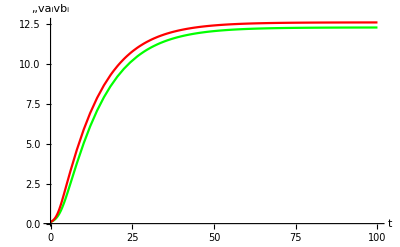

```mathematica
μ=0.1;
r=1;
K1a=K2b=1;
K1b=K2a=0.4;
c1=c2=1;
α=0.5;
d=10.^-3;
sol=EcoSim[{Subscript[ξ, 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},100];
PlotDynamics[sol,{va,vb}]
```

nonfixedvars={va_1,vb_1,va_2,vb_2,R1a,R1b,R2a,R2b}

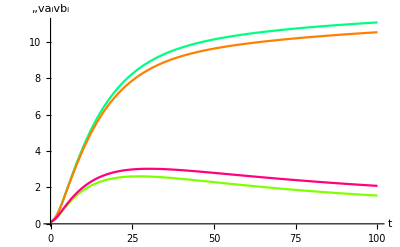

{va_1→1.55051,vb_1→10.5279,va_2→11.0658,vb_2→2.08554,R1a→0.0909462,R1b→0.0488253,R2a→0.0471283,R2b→0.0895858}

```mathematica
sol=EcoSim[{Subscript[ξ, 1]->-1,Subscript[ξ, 2]->0.8},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,Subscript[va, 2]->0.1,Subscript[vb, 2]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},100];
PlotDynamics[sol,{va,vb}]
FinalSlice[sol]
```

```mathematica
sol=EcoSim[{Subscript[ξ, 1]->-1,Subscript[ξ, 2]->0.8,Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,Subscript[va, 2]->0.1,Subscript[vb, 2]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},100]
PlotDynamics[sol,{va,vb}]
FinalSlice[sol]
```

{va_1→InterpolatingFunction[…],vb_1→InterpolatingFunction[…],va_2→InterpolatingFunction[…],vb_2→InterpolatingFunction[…],R1a→InterpolatingFunction[…],R1b→InterpolatingFunction[…],R2a→InterpolatingFunction[…],R2b→InterpolatingFunction[…]}

-Graphics-

{va_1→1.55051,vb_1→10.5279,va_2→11.0658,vb_2→2.08554,R1a→0.0909462,R1b→0.0488253,R2a→0.0471283,R2b→0.0895858}

```mathematica
EcoEqns[{Subscript[ξ, 1]->-1,Subscript[ξ, 0]->1}]
```

{va_1'==-0.101 va_1+0.001 vb_1+va_1 (0.518596 R1a+0.00915469 R1a (Var[ξ][va])_1)+va_1 (0.85502 R2a-0.0342964 R2a (Var[ξ][va])_1),vb_1'==0.001 va_1-0.101 vb_1+vb_1 (0.518596 R1b+0.00915469 R1b (Var[ξ][vb])_1)+vb_1 (0.85502 R2b-0.0342964 R2b (Var[ξ][vb])_1),R1a'==1-R1a-0.518596 R1a va_1-0.00915469 R1a va_1 (Var[ξ][va])_1,R1b'==0.4-R1b-0.518596 R1b vb_1-0.00915469 R1b vb_1 (Var[ξ][vb])_1,R2a'==0.4-R2a-0.85502 R2a va_1+0.0342964 R2a va_1 (Var[ξ][va])_1,R2b'==1-R2b-0.85502 R2b vb_1+0.0342964 R2b vb_1 (Var[ξ][vb])_1}

```mathematica
sol=EcoSim[{Subscript[ξ, 1]->-1,Subscript[ξ, 0]->1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,Subscript[va, 0]->1,Subscript[vb, 0]->1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},1000,Verbose->True];
```

nonfixedvars={va_1,vb_1,va_0,vb_0,R1a,R1b,R2a,R2b}

sol=NDSolve[{va_1'[t]==-0.101 va_1[t]+(0.+0.518596 R1a[t]) va_1[t]+(0.+0.85502 R2a[t]) va_1[t]+0.001 vb_1[t],vb_1'[t]==0.001 va_1[t]-0.101 vb_1[t]+(0.+0.518596 R1b[t]) vb_1[t]+(0.+0.85502 R2b[t]) vb_1[t],va_0'[t]==-0.101 va_0[t]+(0.+0.85502 R1a[t]) va_0[t]+(0.+0.518596 R2a[t]) va_0[t]+0.001 vb_0[t],vb_0'[t]==0.001 va_0[t]-0.101 vb_0[t]+(0.+0.85502 R1b[t]) vb_0[t]+(0.+0.518596 R2b[t]) vb_0[t],R1a'[t]==1.-R1a[t]-0.518596 R1a[t] va_1[t],R1b'[t]==0.4-R1b[t]-0.518596 R1b[t] vb_1[t],R2a'[t]==0.4-R2a[t]-0.85502 R2a[t] va_1[t],R2b'[t]==1.-R2b[t]-0.85502 R2b[t] vb_1[t],va_1[0]==0.1,vb_1[0]==0.1,va_0[0]==1,vb_0[0]==1,R1a[0]==1,R1b[0]==0.4,R2a[0]==0.4,R2b[0]==1},{va_1,vb_1,va_0,vb_0,R1a,R1b,R2a,R2b},{t,0,1000}]⟦1⟧

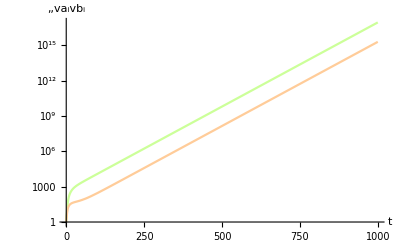

```mathematica
PlotDynamics[sol,{Subscript[va, 0],Subscript[vb, 0]},Logged->True]
```

### tp

```mathematica
SetModel[tp];
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
```

sol=NDSolve[{n1_1'[t]==0.99 n1_1[t]+(-0.49-0.1 n1_1[t]) n1_1[t]+0.01 n2_1[t],n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+(-1.69-0.1 n2_1[t]) n2_1[t],n1_1[0]==0.1,n2_1[0]==0.1},{n1_1,n2_1},{t,0,100}]⟦1⟧

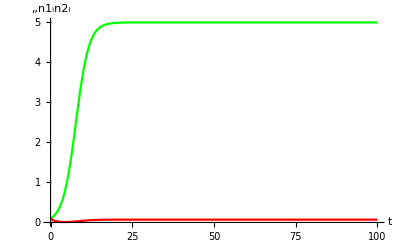

{n1_1→5.00141,n2_1→0.070734}

```mathematica
sol=EcoSim[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->-0.3},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},100,Verbose->True];
PlotDynamics[sol]
FinalSlice[sol]
```

```mathematica
(* no-comp trait *)
sol=EcoSim[{Subscript[x, 1]->-0.3},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},100];
FinalSlice[sol]
```

{n1_1→5.00141,n2_1→0.070734}

```mathematica
(* non-zero Var's *)
sol=EcoSim[{Subscript[x, 1]->-0.3},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},{Var[x]->0.1},100];
FinalSlice[sol]
```

{n1_1→4.00124,n2_1→0.0497067}

```mathematica
(* non-zero Var's *)
sol=EcoSim[{Subscript[x, 1]->-0.3,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1,Var[x]->0.1},100];
FinalSlice[sol]
```

{n1_1→4.00124,n2_1→0.0497067}

```mathematica
(* TODO: no popic comps *)
sol=EcoSim[{Subscript[x, 1]->-0.3},{Subscript[n, 1]->0.1},100];
FinalSlice[sol]
```

FinalSlice[EcoSim[{x_1→-0.3},{n_1→0.1},100]]

sol=NDSolve[{n1_1'[t]==0.99 n1_1[t]+n1_1[t] (-0.49-0.1 (n1_1[t]+n1_2[t]))+0.01 n2_1[t],n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-1.44-0.1 (n2_1[t]+n2_2[t])),n1_2'[t]==0.99 n1_2[t]+n1_2[t] (-1.69-0.1 (n1_1[t]+n1_2[t]))+0.01 n2_2[t],n2_2'[t]==0.01 n1_2[t]+0.99 n2_2[t]+n2_2[t] (-0.64-0.1 (n2_1[t]+n2_2[t])),n1_1[0]==0.1,n2_1[0]==0.1,n1_2[0]==0.1,n2_2[0]==0.1},{n1_1,n2_1,n1_2,n2_2},{t,0,100}]⟦1⟧

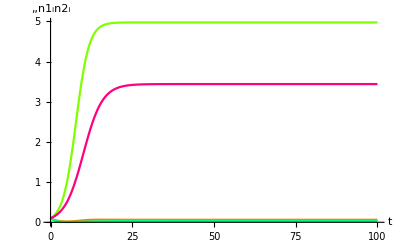

{n1_1→4.9726,n2_1→0.062151,n1_2→0.0286527,n2_2→3.43868}

```mathematica
(* multi-species *)
sol=EcoSim[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->-0.2,Subscript[x[n1], 2]->0.3,Subscript[x[n2], 2]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1,Subscript[n1, 2]->0.1,Subscript[n2, 2]->0.1},100,Verbose->True];
PlotDynamics[sol]
FinalSlice[sol]
```

## *EcoEq

### jonas1

```mathematica
Clear[a1,a2];
SetModel[jonas1]
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Assumptions={μ>0,r>0,K1a>0,K2b>0,K1b>0,K2a>0,c1>0,c2>0,d>0,va_0≥0,va_1≥0,va_2≥0,vb_0≥0,vb_1≥0,vb_2≥0,ξ_0∈ℝ,ξ_1∈ℝ,ξ_2∈ℝ}

```mathematica
a1[ξ_]:=(E^ξ/(1+E^ξ))^α;
a2[ξ_]:=(1-E^ξ/(1+E^ξ))^α;
```

```mathematica
μ=0.1;
r=1;
K1a=K2b=1;
K1b=K2a=0.4;
c1=c2=1;
α=0.5;
d=10.^-3;
sol=EcoSim[{Subscript[ξ, 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},50];
FinalSlice[sol]
```

{va_1→12.0726,vb_1→12.4277,R1a→0.137754,R1b→0.0537366,R2a→0.0353333,R2b→0.0860243}

```mathematica
eq=FindEcoEq[{Subscript[ξ, 1]->-1},FinalSlice[sol]]
```

{va_1→12.3007,vb_1→12.6183,R1a→0.135518,R1b→0.0530236,R2a→0.0347303,R2b→0.0848254}

```mathematica
EcoEigenvalues[{Subscript[ξ, 1]->-1},eq]
```

{-11.7224,-11.4904,-7.51928,-7.31718,-0.0924182,-0.0894611}

```mathematica
sol=EcoSim[{Subscript[ξ, 1]->-1,Subscript[ξ, 2]->1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,Subscript[va, 2]->0.1,Subscript[vb, 2]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},100];
FinalSlice[sol]
```

{va_1→1.65648,vb_1→10.9563,va_2→10.9563,vb_2→1.65648,R1a→0.089074,R1b→0.0493911,R2a→0.0493911,R2b→0.089074}

```mathematica
eq=FindEcoEq[{Subscript[ξ, 1]->-1,Subscript[ξ, 2]->1},FinalSlice[sol]]
```

{va_1→0.94901,vb_1→11.6705,va_2→11.6705,vb_2→0.94901,R1a→0.0871787,R1b→0.0508666,R2a→0.0508666,R2b→0.0871787}

```mathematica
EcoEigenvalues[{Subscript[ξ, 1]->-1,Subscript[ξ, 2]->1},eq]
```

{-11.4038,-11.4038,-7.8382,-7.83819,-0.0930083,-0.0909827,-0.0137825,-0.011774}

### tp

```mathematica
SetModel[tp]
```

$Assumptions={b≥0,d0≥0,d12≥0,d21≥0,σμ≥0,n1_0≥0,n1_1≥0,n1_2≥0,n2_0≥0,n2_1≥0,n2_2≥0,x_0∈ℝ,x_1∈ℝ,x_2∈ℝ}

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
```

```mathematica
SolveEcoEq[{Subscript[x, 1]->-0.3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0},{n1_1→0.1442,n2_1→-7.00206},{n1_1→4.85439,n2_1→-7.06867},{n1_1→5.00141,n2_1→0.070734}}

```mathematica
SolveEcoEq[{Subscript[x, 1]->-0.3},{Var[Subscript[x, 1]]->0}]
SolveEcoEq[{Subscript[x, 1]->-0.3},{Var[x]->0}]
SolveEcoEq[{Subscript[x, 1]->-0.3,Var[x]->0}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0},{n1_1→0.1442,n2_1→-7.00206},{n1_1→4.85439,n2_1→-7.06867},{n1_1→5.00141,n2_1→0.070734}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0},{n1_1→0.1442,n2_1→-7.00206},{n1_1→4.85439,n2_1→-7.06867},{n1_1→5.00141,n2_1→0.070734}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0},{n1_1→0.1442,n2_1→-7.00206},{n1_1→4.85439,n2_1→-7.06867},{n1_1→5.00141,n2_1→0.070734}}

```mathematica
(* 2sp, combined traits and Gs *)
SolveEcoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3,Var[x]->0.1}]
NSolveEcoEq[{Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3,Var[x]->0.1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→3.78754,n2_1→-8.04707,n1_2→0,n2_2→0},{n1_1→0.211219,n2_1→-8.00264,n1_2→0,n2_2→0},{n1_1→4.00124,n2_1→0.0497067,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-8.04707,n2_2→3.78754},{n1_1→0,n2_1→0,n1_2→-8.00264,n2_2→0.211219},{n1_1→0,n2_1→0,n1_2→0.0497067,n2_2→4.00124},{n1_1→0.0672292,n2_1→-8.06806,n1_2→-8.06806,n2_2→0.0672292},{n1_1→3.96777,n2_1→0.0330625,n1_2→0.0330625,n2_2→3.96777}}

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→0.211219,n2_1→-8.00264,n1_2→0,n2_2→0},{n1_1→3.78754,n2_1→-8.04707,n1_2→0,n2_2→0},{n1_1→4.00124,n2_1→0.0497067,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-8.04707,n2_2→3.78754},{n1_1→0,n2_1→0,n1_2→-8.00264,n2_2→0.211219},{n1_1→0,n2_1→0,n1_2→0.0497067,n2_2→4.00124},{n1_1→0.0672292,n2_1→-8.06806,n1_2→-8.06806,n2_2→0.0672292},{n1_1→3.96777,n2_1→0.0330625,n1_2→0.0330625,n2_2→3.96777}}

```mathematica
eq=SolveEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→4.99725,n2_1→-0.137386,n1_2→0,n2_2→0},{n1_1→-0.0690081,n2_1→3.49803,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-0.137386,n2_2→4.99725},{n1_1→0,n2_1→0,n1_2→3.49803,n2_2→-0.0690081},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502},{n1_1→-0.248349,n2_1→3.74171,n1_2→3.74171,n2_2→-0.248349}}

```mathematica
SelectValid[eq]
```

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}}

```mathematica
ExtantSpecies/@SelectValid[eq]
```

{{},{n_1},{n_2},{n_1,n_2}}

```mathematica
eq=SolveEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},{Var[x][n1]->0.1,Var[x][n2]->0.2}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→4.99725,n2_1→-0.137386,n1_2→0,n2_2→0},{n1_1→-0.0690081,n2_1→3.49803,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-0.137386,n2_2→4.99725},{n1_1→0,n2_1→0,n1_2→3.49803,n2_2→-0.0690081},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502},{n1_1→-0.248349,n2_1→3.74171,n1_2→3.74171,n2_2→-0.248349}}

```mathematica
NSolveEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3}]
```

{{n1_1→0,n2_1→0,n1_2→0,n2_2→0},{n1_1→5.07176,n2_1→3.63936,n1_2→0,n2_2→0},{n1_1→4.99725,n2_1→-0.137386,n1_2→0,n2_2→0},{n1_1→-0.0690081,n2_1→3.49803,n1_2→0,n2_2→0},{n1_1→0,n2_1→0,n1_2→-0.137386,n2_2→4.99725},{n1_1→0,n2_1→0,n1_2→3.49803,n2_2→-0.0690081},{n1_1→0,n2_1→0,n1_2→3.63936,n2_2→5.07176},{n1_1→-0.248349,n2_1→3.74171,n1_2→3.74171,n2_2→-0.248349},{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}}

```mathematica
eq=FindEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},{Subscript[n1, 1]->5,Subscript[n2, 1]->0.5,Subscript[n1, 2]->0.5,Subscript[n2, 2]->5}]
```

{n1_1→4.69502,n2_1→0.311622,n1_2→0.311622,n2_2→4.69502}

```mathematica
EcoEigenvalues[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq]
```

{-0.527297,-0.500664,-0.151327,-0.124694}

```mathematica
eq=FindEcoEq[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3,Subscript[n1, 1]->5,Subscript[n2, 1]->0.5,Subscript[n1, 2]->0.5,Subscript[n2, 2]->5,Var[x]->0.1}]
```

{n1_1→3.75726,n2_1→0.24938,n1_2→0.24938,n2_2→3.75726}

```mathematica
EcoEigenvalues[{Subscript[x[n1], 1]->-0.3,Subscript[x[n2], 1]->0.2,Subscript[x[n1], 2]->-0.2,Subscript[x[n2], 2]->0.3},eq,{Var[x]->0.1},Verbose->True]
```

EcoEigenvalues: Jacobian={{-0.376389,0.01,-0.375726,0},{0.01,-0.175602,0,-0.024938},{-0.024938,0,-0.175602,0.01},{0,-0.375726,0.01,-0.376389}}

{-0.429473,-0.400664,-0.151327,-0.122518}

## EcoEvoSim

### jonas1

```mathematica
Clear[a1,a2];
SetModel[jonas1]
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i]

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R2a a2[ξ[va]_i] va_i-1/2 R2a va_i (Var[ξ][va])_i a2''[ξ[va]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R1b a1[ξ[vb]_i] vb_i-1/2 R1b vb_i (Var[ξ][vb])_i a1''[ξ[vb]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R2b a2[ξ[vb]_i] vb_i-1/2 R2b vb_i (Var[ξ][vb])_i a2''[ξ[vb]_i]

```mathematica
a1[ξ_]:=(E^ξ/(1+E^ξ))^α;
a2[ξ_]:=(1-E^ξ/(1+E^ξ))^α;
μ=0.1;
r=1;
K1a=K2b=1;
K1b=K2a=0.4;
c1=c2=1;
α=0.5;
d=10.^-3;
```

nonfixedvars={va_1,vb_1,R1a,R1b,R2a,R2b,ξ[va]_1,ξ[vb]_1}

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

EcoEvoSim: eqns=

{va_1'[t]==-0.101 va_1[t]+((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t]) va_1[t]+((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t]+0.05 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t]) va_1[t]+0.001 vb_1[t],vb_1'[t]==0.001 va_1[t]-0.101 vb_1[t]+((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t]) vb_1[t]+((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t]+0.05 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t]) vb_1[t],R1a'[t]==1-R1a[t]-(ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t] va_1[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t] va_1[t],R1b'[t]==0.4-R1b[t]-(ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t] vb_1[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t] vb_1[t],R2a'[t]==0.4-R2a[t]-(1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t] va_1[t]-0.05 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t] va_1[t],R2b'[t]==1-R2b[t]-(1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t] vb_1[t]-0.05 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t] vb_1[t],ξ[va]_1'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R1a[t])/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)+(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)) R1a[t])+0.1 ((0.5 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R2a[t])/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)-(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t])+(0.001 vb_1[t] (-ξ[va]_1[t]+ξ[vb]_1[t]))/va_1[t],ξ[vb]_1'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R1b[t])/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)+(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)) R1b[t])+0.1 ((0.5 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R2b[t])/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)-(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t])+(0.001 va_1[t] (ξ[va]_1[t]-ξ[vb]_1[t]))/vb_1[t]}

EcoEvoSim: ics=

{va_1[0]==0.1,vb_1[0]==0.1,R1a[0]==1,R1b[0]==0.4,R2a[0]==0.4,R2b[0]==1,ξ[va]_1[0]==-1,ξ[vb]_1[0]==-1}

EcoEvoSim: unks=

{va_1,vb_1,R1a,R1b,R2a,R2b,ξ[va]_1,ξ[vb]_1}

EcoEvoSim: bdwhens=

{}

EcoEvoSim: discretevars=

{}

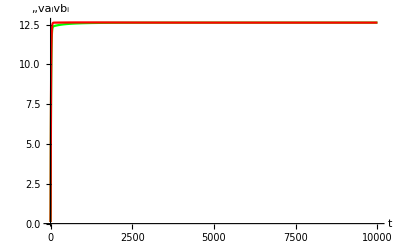

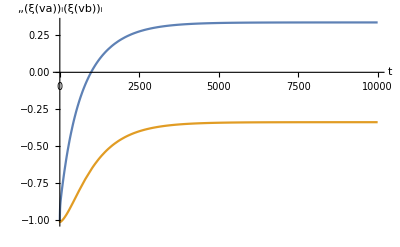

```mathematica
sol=EcoEvoSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10000,Verbose->True];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
```

nonfixedvars={va_1,vb_1,R1a,R1b,R2a,R2b,ξ[va]_1,ξ[vb]_1}

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

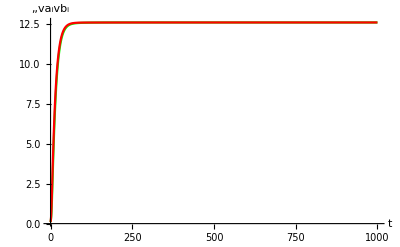

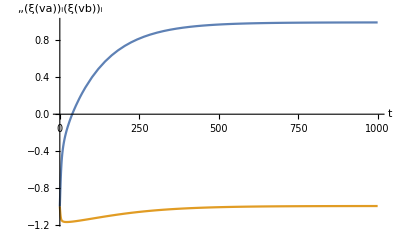

```mathematica
(* testing default Var *)
sol=EcoEvoSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},1000];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
```

```mathematica
(* trait ICs - no specific comps *)
sol=EcoEvoSim[{Subscript[ξ, 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},10000];
PlotDynamics[sol,{ξ[va],ξ[vb]}]
FinalSlice[sol]
```

nonfixedvars={va_1,vb_1,R1a,R1b,R2a,R2b,ξ_1,ξ[va]_1,ξ[vb]_1}

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ_1,ξ[va]_1,ξ[vb]_1}

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

PlotDynamics[SortRuleList[{va_1'[t]==-0.101 va_1[t]+((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t]+1/2 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t]) va_1[t]+((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t]+1/2 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t]) va_1[t]+0.001 vb_1[t],vb_1'[t]==0.001 va_1[t]-0.101 vb_1[t]+((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t]+1/2 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t]) vb_1[t]+((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t]+1/2 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t]) vb_1[t],R1a'[t]==1-R1a[t]-(ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t] va_1[t]-1/2 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t] va_1[t],R1b'[t]==0.4-R1b[t]-(ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t] vb_1[t]-1/2 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t] vb_1[t],R2a'[t]==0.4-R2a[t]-(1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t] va_1[t]-1/2 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t] va_1[t],R2b'[t]==1-R2b[t]-(1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t] vb_1[t]-1/2 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t] vb_1[t],ξ_1'[t]==EcoEvo`Private`dxdt[ξ],ξ[va]_1'[t]==(0.5 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R1a[t])/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+1/2 ((0.5 (-(6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)+(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)) R1a[t]+(0.5 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R2a[t])/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+1/2 ((0.375 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)-(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t]+(0.001 vb_1[t] (-ξ[va]_1[t]+ξ[vb]_1[t]))/va_1[t],ξ[vb]_1'[t]==(0.5 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R1b[t])/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+1/2 ((0.5 (-(6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)+(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)) R1b[t]+(0.5 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R2b[t])/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+1/2 ((0.375 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)-(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t]+(0.001 va_1[t] (ξ[va]_1[t]-ξ[vb]_1[t]))/vb_1[t],va_1[0]==0.1,vb_1[0]==0.1,R1a[0]==1,R1b[0]==0.4,R2a[0]==0.4,R2b[0]==1,ξ_1[0]==-1,ξ[va]_1[0]==-1,ξ[vb]_1[0]==-1},{va_1,vb_1,R1a,R1b,R2a,R2b,ξ_1,ξ[va]_1,ξ[vb]_1}],{ξ[va],ξ[vb]}]

FinalSlice[SortRuleList[{va_1'[t]==-0.101 va_1[t]+((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t]+1/2 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t]) va_1[t]+((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t]+1/2 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t]) va_1[t]+0.001 vb_1[t],vb_1'[t]==0.001 va_1[t]-0.101 vb_1[t]+((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t]+1/2 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t]) vb_1[t]+((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t]+1/2 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t]) vb_1[t],R1a'[t]==1-R1a[t]-(ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t] va_1[t]-1/2 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t] va_1[t],R1b'[t]==0.4-R1b[t]-(ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t] vb_1[t]-1/2 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t] vb_1[t],R2a'[t]==0.4-R2a[t]-(1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t] va_1[t]-1/2 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t] va_1[t],R2b'[t]==1-R2b[t]-(1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t] vb_1[t]-1/2 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t] vb_1[t],ξ_1'[t]==EcoEvo`Private`dxdt[ξ],ξ[va]_1'[t]==(0.5 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R1a[t])/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+1/2 ((0.5 (-(6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)+(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)) R1a[t]+(0.5 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R2a[t])/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+1/2 ((0.375 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)-(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t]+(0.001 vb_1[t] (-ξ[va]_1[t]+ξ[vb]_1[t]))/va_1[t],ξ[vb]_1'[t]==(0.5 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R1b[t])/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+1/2 ((0.5 (-(6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)+(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)) R1b[t]+(0.5 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R2b[t])/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+1/2 ((0.375 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)-(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t]+(0.001 va_1[t] (ξ[va]_1[t]-ξ[vb]_1[t]))/vb_1[t],va_1[0]==0.1,vb_1[0]==0.1,R1a[0]==1,R1b[0]==0.4,R2a[0]==0.4,R2b[0]==1,ξ_1[0]==-1,ξ[va]_1[0]==-1,ξ[vb]_1[0]==-1},{va_1,vb_1,R1a,R1b,R2a,R2b,ξ_1,ξ[va]_1,ξ[vb]_1}]]

nonfixedvars={va_1,vb_1,va_0,vb_0,R1a,R1b,R2a,R2b,ξ[va]_1,ξ[vb]_1,ξ[va]_0,ξ[vb]_0}

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1,ξ[va]_0,ξ[vb]_0}

{va_0→InterpolatingFunction[…],vb_0→InterpolatingFunction[…],ξ[va]_0→InterpolatingFunction[…],ξ[vb]_0→InterpolatingFunction[…],va_1→InterpolatingFunction[…],vb_1→InterpolatingFunction[…],R1a→InterpolatingFunction[…],R1b→InterpolatingFunction[…],R2a→InterpolatingFunction[…],R2b→InterpolatingFunction[…],ξ[va]_1→InterpolatingFunction[…],ξ[vb]_1→InterpolatingFunction[…]}

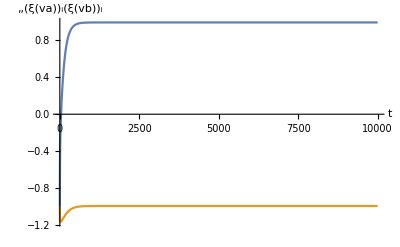

{va_0→25.7529,vb_0→3.10787,ξ[va]_0→1.48561,ξ[vb]_0→0.622993,va_1→12.595,vb_1→12.595,R1a→0.0882663,R1b→0.0522366,R2a→0.0522366,R2b→0.0882663,ξ[va]_1→0.994887,ξ[vb]_1→-0.994887}

```mathematica
(* adding ghost *)
debug=False;
sol=EcoEvoSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1,Subscript[ξ[va], 0]->1,Subscript[ξ[vb], 0]->1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,Subscript[va, 0]->1,Subscript[vb, 0]->1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},10000]
debug=False;
PlotDynamics[sol,{ξ[va],ξ[vb]}]
FinalSlice[sol]
```

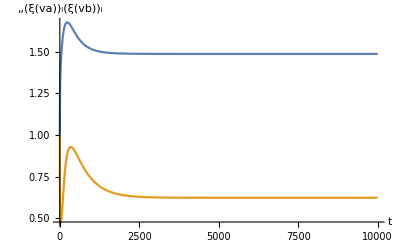

```mathematica
PlotDynamics[sol,{Subscript[ξ[va], 0],Subscript[ξ[vb], 0]}]
```

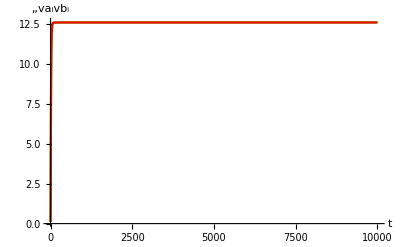

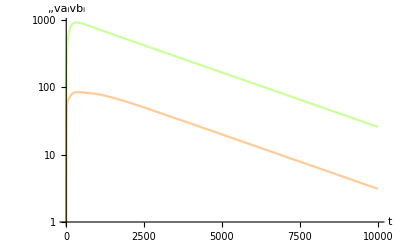

```mathematica
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{Subscript[va, 0],Subscript[vb, 0]},Logged->True]
```

### tp

```mathematica
SetModel[tp];
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
```

```mathematica
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2},{Subscript[Var[x][n1], 1]->0.01,Subscript[Var[x][n2], 1]->0.01},1000,Verbose->True];
FinalSlice[sol]
```

EcoEvoSim: eqns=

{n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-0.01-0.1 n1_1[t]-(1+x[n1]_1[t])^2),n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-0.01-0.1 n2_1[t]-(-1+x[n2]_1[t])^2),x[n1]_1'[t]==-0.02 (1+x[n1]_1[t])+(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t],x[n2]_1'[t]==0.01 (2-2 x[n2]_1[t])+(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]}

EcoEvoSim: ics=

{x[n1]_1[0]==-0.8,x[n2]_1[0]==0.8,n1_1[0]==0.1,n2_1[0]==0.2}

EcoEvoSim: unks=

{n1_1,n2_1,x[n1]_1,x[n2]_1}

EcoEvoSim: bdwhens=

{}

EcoEvoSim: discretevars=

{}

{n1_1→0.0329991,n2_1→9.80034,x[n1]_1→0.986599,x[n2]_1→0.999977}

```mathematica
(* combine traits, pops, vars *)
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Subscript[Var[x][n1], 1]->0.01,Subscript[Var[x][n2], 1]->0.01},1000];
FinalSlice[sol]
```

{n1_1→0.0329991,n2_1→9.80034,x[n1]_1→0.986599,x[n2]_1→0.999977}

```mathematica
(* no comp-dependent vars *)
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Subscript[Var[x], 1]->0.01},1000];
FinalSlice[sol]
```

{n1_1→0.0329991,n2_1→9.80034,x[n1]_1→0.986599,x[n2]_1→0.999977}

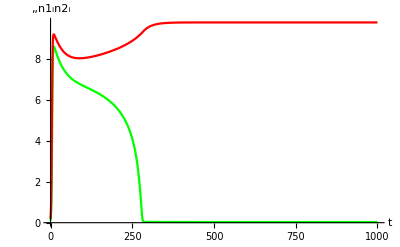

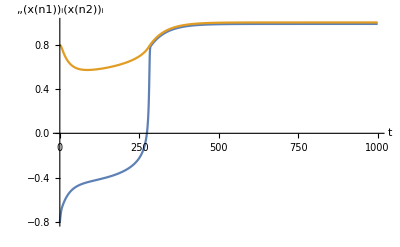

{n1_1→0.0329991,n2_1→9.80034,x[n1]_1→0.986599,x[n2]_1→0.999977}

```mathematica
(* no species-dependent vars *)
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Var[x]->0.01},1000];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

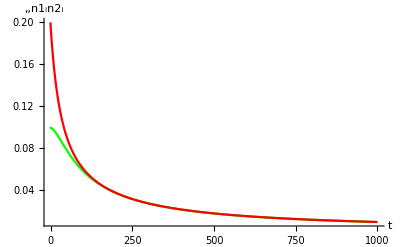

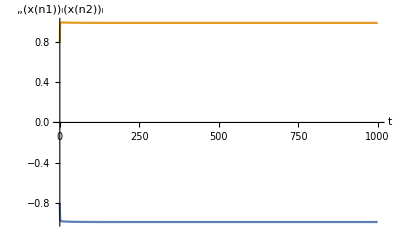

{n1_1→0.00887276,n2_1→0.00887276,x[n1]_1→-0.990099,x[n2]_1→0.990099}

```mathematica
(* no vars given *)
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2},1000];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

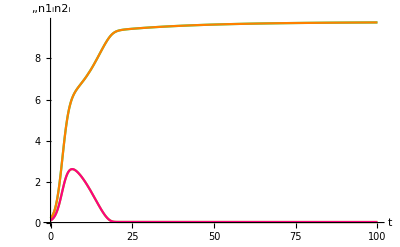

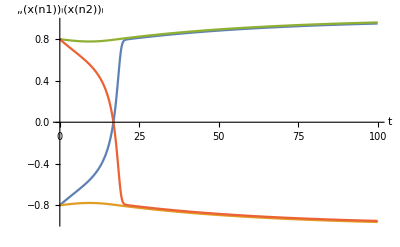

{n1_1→0.0256691,n2_1→9.7586,n1_2→9.7586,n2_2→0.0256691,x[n1]_1→0.950391,x[n2]_1→0.96086,x[n1]_2→-0.96086,x[n2]_2→-0.950391}

```mathematica
(* two species *)
sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Subscript[x[n1], 2]->-0.8,Subscript[x[n2], 2]->0.8,Subscript[n1, 2]->0.2,Subscript[n2, 2]->0.1,Var[x]->0.01},100];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

```mathematica
(* just for exploration *)
d12=d21=0.01;sol=EcoEvoSim[{Subscript[x[n1], 1]->-0.8,Subscript[x[n2], 1]->0.8,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.2,Var[x]->0.01},1000,Verbose->False];
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
FinalSlice[sol]
```

-Graphics-

-Graphics-

{n1_1→0.0329991,n2_1→9.80034,x[n1]_1→0.986599,x[n2]_1→0.999977}

## FindEcoEvoEq / *

### jonas1

```mathematica
Clear[a1,a2];
SetModel[jonas1]
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i]

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R2a a2[ξ[va]_i] va_i-1/2 R2a va_i (Var[ξ][va])_i a2''[ξ[va]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R1b a1[ξ[vb]_i] vb_i-1/2 R1b vb_i (Var[ξ][vb])_i a1''[ξ[vb]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R2b a2[ξ[vb]_i] vb_i-1/2 R2b vb_i (Var[ξ][vb])_i a2''[ξ[vb]_i]

```mathematica
a1[ξ_]:=(E^ξ/(1+E^ξ))^α;
a2[ξ_]:=(1-E^ξ/(1+E^ξ))^α;
μ=0.1;
r=1;
K1a=K2b=1;
K1b=K2a=0.4;
c1=c2=1;
α=0.5;
d=10.^-3;
```

```mathematica
sol=EcoEvoSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10000];
PlotDynamics[sol,{ξ[va],ξ[vb]}]
FinalSlice[sol]
```

nonfixedvars={va_1,vb_1,R1a,R1b,R2a,R2b,ξ[va]_1,ξ[vb]_1}

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

-Graphics-

{va_1→12.6185,vb_1→12.6185,R1a→0.0943354,R1b→0.0438134,R2a→0.0438131,R2b→0.0943348,ξ[va]_1→0.336762,ξ[vb]_1→-0.336791}

```mathematica
eq=FindEcoEvoEq[FinalSlice[sol],{Var[ξ]->0.1}]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{va_1→12.6185,vb_1→12.6185,R1a→0.0943351,R1b→0.0438132,R2a→0.0438132,R2b→0.0943351,ξ[va]_1→0.336777,ξ[vb]_1→-0.336777}

```mathematica
EcoEvoJacobian[eq,{Var[ξ]->0.1}]//MatrixForm
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

(-0.001 | 0.001 | 9.60051 | 0 | 8.12966 | 0 | 0.0849924 | 0
0.001 | -0.001 | 0 | 8.12966 | 0 | 9.60051 | 0 | -0.0849924
-0.0717727 | 0 | -10.6005 | 0 | 0 | 0 | -0.187267 | 0
0 | -0.0282273 | 0 | -9.12966 | 0 | 0 | 0 | -0.102274
-0.0282273 | 0 | 0 | 0 | -9.12966 | 0 | 0.102274 | 0
0 | -0.0717727 | 0 | 0 | 0 | -10.6005 | 0 | 0.187267
0.0000533782 | -0.0000533782 | 0.0157318 | 0 | -0.0184992 | 0 | -0.00163158 | 0.001
0.0000533782 | -0.0000533782 | 0 | 0.0184992 | 0 | -0.0157318 | 0.001 | -0.00163158)

```mathematica
EcoEvoEigenvalues[eq,{Var[ξ]->0.1}]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{-10.5358,-10.5358,-9.10291,-9.10291,-0.0929749,-0.0909496,-0.00312053,-0.00111271}

nonfixedvars={va_1,vb_1,R1a,R1b,R2a,R2b,ξ[va]_1,ξ[vb]_1}

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

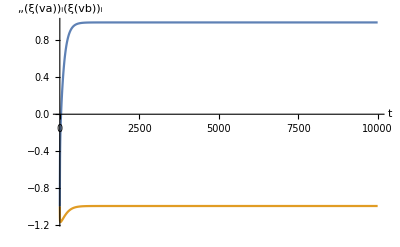

{va_1→12.595,vb_1→12.595,R1a→0.0882663,R1b→0.0522366,R2a→0.0522366,R2b→0.0882663,ξ[va]_1→0.994887,ξ[vb]_1→-0.994887}

```mathematica
sol=EcoEvoSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},10000];
PlotDynamics[sol,{ξ[va],ξ[vb]}]
FinalSlice[sol]
```

```mathematica
eq=FindEcoEvoEq[FinalSlice[sol]]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{va_1→12.595,vb_1→12.595,R1a→0.0882663,R1b→0.0522366,R2a→0.0522366,R2b→0.0882663,ξ[va]_1→0.994887,ξ[vb]_1→-0.994887}

```mathematica
sol=EcoEvoSim[{Subscript[ξ, 1]->-1,Subscript[ξ, 2]->1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,Subscript[va, 2]->0.1,Subscript[vb, 2]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},2000];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
FinalSlice[sol]
```

nonfixedvars={va_1,vb_1,va_2,vb_2,R1a,R1b,R2a,R2b,ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

alltraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

nonfixedtraits={ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

PlotDynamics[SortRuleList[{va_1'[t]==-0.101 va_1[t]+((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t]) va_1[t]+((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t]+0.05 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t]) va_1[t]+0.001 vb_1[t],vb_1'[t]==0.001 va_1[t]-0.101 vb_1[t]+((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t]) vb_1[t]+((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t]+0.05 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t]) vb_1[t],va_2'[t]==-0.101 va_2[t]+((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R1a[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)) R1a[t]) va_2[t]+((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R2a[t]+0.05 (-(0.25 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)) R2a[t]) va_2[t]+0.001 vb_2[t],vb_2'[t]==0.001 va_2[t]-0.101 vb_2[t]+((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R1b[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)) R1b[t]) vb_2[t]+((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R2b[t]+0.05 (-(0.25 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)) R2b[t]) vb_2[t],R1a'[t]==1-R1a[t]-(ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t] va_1[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t] va_1[t]-(ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R1a[t] va_2[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)) R1a[t] va_2[t],R1b'[t]==0.4-R1b[t]-(ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t] vb_1[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t] vb_1[t]-(ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R1b[t] vb_2[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)) R1b[t] vb_2[t],R2a'[t]==0.4-R2a[t]-(1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t] va_1[t]-0.05 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t] va_1[t]-(1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R2a[t] va_2[t]-0.05 (-(0.25 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)) R2a[t] va_2[t],R2b'[t]==1-R2b[t]-(1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t] vb_1[t]-0.05 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t] vb_1[t]-(1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R2b[t] vb_2[t]-0.05 (-(0.25 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)) R2b[t] vb_2[t],ξ_1'[t]==EcoEvo`Private`dxdt[ξ],ξ[va]_1'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R1a[t])/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)+(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)) R1a[t])+0.1 ((0.5 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R2a[t])/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)-(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t])+(0.001 vb_1[t] (-ξ[va]_1[t]+ξ[vb]_1[t]))/va_1[t],ξ[vb]_1'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R1b[t])/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)+(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)) R1b[t])+0.1 ((0.5 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R2b[t])/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)-(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t])+(0.001 va_1[t] (ξ[va]_1[t]-ξ[vb]_1[t]))/vb_1[t],ξ_2'[t]==EcoEvo`Private`dxdt[ξ],ξ[va]_2'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) R1a[t])/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^4)+(12 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(7 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^3)/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2.5)) R1a[t])+0.1 ((0.5 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) R2a[t])/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^3)/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2.5)-(0.75 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) (-(2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^4)-(12 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(7 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)) R2a[t])+(0.001 vb_2[t] (-ξ[va]_2[t]+ξ[vb]_2[t]))/va_2[t],ξ[vb]_2'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) R1b[t])/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^4)+(12 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(7 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^3)/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2.5)) R1b[t])+0.1 ((0.5 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) R2b[t])/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^3)/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2.5)-(0.75 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) (-(2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^4)-(12 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(7 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)) R2b[t])+(0.001 va_2[t] (ξ[va]_2[t]-ξ[vb]_2[t]))/vb_2[t],va_1[0]==0.1,vb_1[0]==0.1,va_2[0]==0.1,vb_2[0]==0.1,R1a[0]==1,R1b[0]==0.4,R2a[0]==0.4,R2b[0]==1,ξ_1[0]==-1,ξ[va]_1[0]==-1,ξ[vb]_1[0]==-1,ξ_2[0]==1,ξ[va]_2[0]==1,ξ[vb]_2[0]==1},{va_1,vb_1,va_2,vb_2,R1a,R1b,R2a,R2b,ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}],{va,vb}]

PlotDynamics[SortRuleList[{va_1'[t]==-0.101 va_1[t]+((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t]) va_1[t]+((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t]+0.05 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t]) va_1[t]+0.001 vb_1[t],vb_1'[t]==0.001 va_1[t]-0.101 vb_1[t]+((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t]) vb_1[t]+((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t]+0.05 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t]) vb_1[t],va_2'[t]==-0.101 va_2[t]+((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R1a[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)) R1a[t]) va_2[t]+((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R2a[t]+0.05 (-(0.25 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)) R2a[t]) va_2[t]+0.001 vb_2[t],vb_2'[t]==0.001 va_2[t]-0.101 vb_2[t]+((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R1b[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)) R1b[t]) vb_2[t]+((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R2b[t]+0.05 (-(0.25 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)) R2b[t]) vb_2[t],R1a'[t]==1-R1a[t]-(ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t] va_1[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t] va_1[t]-(ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R1a[t] va_2[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)) R1a[t] va_2[t],R1b'[t]==0.4-R1b[t]-(ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t] vb_1[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t] vb_1[t]-(ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R1b[t] vb_2[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)) R1b[t] vb_2[t],R2a'[t]==0.4-R2a[t]-(1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t] va_1[t]-0.05 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t] va_1[t]-(1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R2a[t] va_2[t]-0.05 (-(0.25 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)) R2a[t] va_2[t],R2b'[t]==1-R2b[t]-(1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t] vb_1[t]-0.05 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t] vb_1[t]-(1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R2b[t] vb_2[t]-0.05 (-(0.25 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)) R2b[t] vb_2[t],ξ_1'[t]==EcoEvo`Private`dxdt[ξ],ξ[va]_1'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R1a[t])/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)+(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)) R1a[t])+0.1 ((0.5 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R2a[t])/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)-(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t])+(0.001 vb_1[t] (-ξ[va]_1[t]+ξ[vb]_1[t]))/va_1[t],ξ[vb]_1'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R1b[t])/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)+(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)) R1b[t])+0.1 ((0.5 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R2b[t])/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)-(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t])+(0.001 va_1[t] (ξ[va]_1[t]-ξ[vb]_1[t]))/vb_1[t],ξ_2'[t]==EcoEvo`Private`dxdt[ξ],ξ[va]_2'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) R1a[t])/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^4)+(12 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(7 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^3)/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2.5)) R1a[t])+0.1 ((0.5 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) R2a[t])/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^3)/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2.5)-(0.75 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) (-(2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^4)-(12 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(7 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)) R2a[t])+(0.001 vb_2[t] (-ξ[va]_2[t]+ξ[vb]_2[t]))/va_2[t],ξ[vb]_2'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) R1b[t])/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^4)+(12 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(7 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^3)/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2.5)) R1b[t])+0.1 ((0.5 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) R2b[t])/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^3)/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2.5)-(0.75 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) (-(2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^4)-(12 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(7 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)) R2b[t])+(0.001 va_2[t] (ξ[va]_2[t]-ξ[vb]_2[t]))/vb_2[t],va_1[0]==0.1,vb_1[0]==0.1,va_2[0]==0.1,vb_2[0]==0.1,R1a[0]==1,R1b[0]==0.4,R2a[0]==0.4,R2b[0]==1,ξ_1[0]==-1,ξ[va]_1[0]==-1,ξ[vb]_1[0]==-1,ξ_2[0]==1,ξ[va]_2[0]==1,ξ[vb]_2[0]==1},{va_1,vb_1,va_2,vb_2,R1a,R1b,R2a,R2b,ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}],{ξ[va],ξ[vb]}]

FinalSlice[SortRuleList[{va_1'[t]==-0.101 va_1[t]+((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t]) va_1[t]+((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t]+0.05 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t]) va_1[t]+0.001 vb_1[t],vb_1'[t]==0.001 va_1[t]-0.101 vb_1[t]+((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t]) vb_1[t]+((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t]+0.05 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t]) vb_1[t],va_2'[t]==-0.101 va_2[t]+((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R1a[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)) R1a[t]) va_2[t]+((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R2a[t]+0.05 (-(0.25 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)) R2a[t]) va_2[t]+0.001 vb_2[t],vb_2'[t]==0.001 va_2[t]-0.101 vb_2[t]+((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R1b[t]+0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)) R1b[t]) vb_2[t]+((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R2b[t]+0.05 (-(0.25 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)) R2b[t]) vb_2[t],R1a'[t]==1-R1a[t]-(ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R1a[t] va_1[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)) R1a[t] va_1[t]-(ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R1a[t] va_2[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)) R1a[t] va_2[t],R1b'[t]==0.4-R1b[t]-(ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R1b[t] vb_1[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)) R1b[t] vb_1[t]-(ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R1b[t] vb_2[t]-0.05 ((0.5 ((2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)-(0.25 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)) R1b[t] vb_2[t],R2a'[t]==0.4-R2a[t]-(1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5 R2a[t] va_1[t]-0.05 (-(0.25 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t] va_1[t]-(1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5 R2a[t] va_2[t]-0.05 (-(0.25 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2)/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)) R2a[t] va_2[t],R2b'[t]==1-R2b[t]-(1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5 R2b[t] vb_1[t]-0.05 (-(0.25 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t] vb_1[t]-(1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5 R2b[t] vb_2[t]-0.05 (-(0.25 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2)/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.5 (-(2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)) R2b[t] vb_2[t],ξ_1'[t]==EcoEvo`Private`dxdt[ξ],ξ[va]_1'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R1a[t])/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)+(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)-(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)+ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)) R1a[t])+0.1 ((0.5 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) R2a[t])/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^3)/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[va]_1[t])/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))) (-(2 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(3 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^4)-(12 ⅇ^(3 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^3)+(7 ⅇ^(2 ξ[va]_1[t]))/((1+ⅇ^(ξ[va]_1[t]))^2)-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t]))))/((1-ⅇ^(ξ[va]_1[t])/(1+ⅇ^(ξ[va]_1[t])))^0.5)) R2a[t])+(0.001 vb_1[t] (-ξ[va]_1[t]+ξ[vb]_1[t]))/va_1[t],ξ[vb]_1'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R1b[t])/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)+(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)-(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)+ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)) R1b[t])+0.1 ((0.5 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) R2b[t])/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^3)/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^2.5)-(0.75 (ⅇ^(2 ξ[vb]_1[t])/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))) (-(2 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(3 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^4)-(12 ⅇ^(3 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^3)+(7 ⅇ^(2 ξ[vb]_1[t]))/((1+ⅇ^(ξ[vb]_1[t]))^2)-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t]))))/((1-ⅇ^(ξ[vb]_1[t])/(1+ⅇ^(ξ[vb]_1[t])))^0.5)) R2b[t])+(0.001 va_1[t] (ξ[va]_1[t]-ξ[vb]_1[t]))/vb_1[t],ξ_2'[t]==EcoEvo`Private`dxdt[ξ],ξ[va]_2'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) R1a[t])/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^4)+(12 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(7 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)-(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)+ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^3)/((ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2.5)) R1a[t])+0.1 ((0.5 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) R2a[t])/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^3)/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^2.5)-(0.75 (ⅇ^(2 ξ[va]_2[t])/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))) (-(2 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(3 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^4)-(12 ⅇ^(3 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^3)+(7 ⅇ^(2 ξ[va]_2[t]))/((1+ⅇ^(ξ[va]_2[t]))^2)-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t]))))/((1-ⅇ^(ξ[va]_2[t])/(1+ⅇ^(ξ[va]_2[t])))^0.5)) R2a[t])+(0.001 vb_2[t] (-ξ[va]_2[t]+ξ[vb]_2[t]))/va_2[t],ξ[vb]_2'[t]==0.1 ((0.5 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) R1b[t])/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)+0.05 ((0.5 (-(6 ⅇ^(4 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^4)+(12 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(7 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)-(0.75 ((2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)-(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.375 (-ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)+ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^3)/((ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2.5)) R1b[t])+0.1 ((0.5 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) R2b[t])/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)+0.05 ((0.375 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^3)/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^2.5)-(0.75 (ⅇ^(2 ξ[vb]_2[t])/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))) (-(2 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(3 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^1.5)+(0.5 ((6 ⅇ^(4 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^4)-(12 ⅇ^(3 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^3)+(7 ⅇ^(2 ξ[vb]_2[t]))/((1+ⅇ^(ξ[vb]_2[t]))^2)-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t]))))/((1-ⅇ^(ξ[vb]_2[t])/(1+ⅇ^(ξ[vb]_2[t])))^0.5)) R2b[t])+(0.001 va_2[t] (ξ[va]_2[t]-ξ[vb]_2[t]))/vb_2[t],va_1[0]==0.1,vb_1[0]==0.1,va_2[0]==0.1,vb_2[0]==0.1,R1a[0]==1,R1b[0]==0.4,R2a[0]==0.4,R2b[0]==1,ξ_1[0]==-1,ξ[va]_1[0]==-1,ξ[vb]_1[0]==-1,ξ_2[0]==1,ξ[va]_2[0]==1,ξ[vb]_2[0]==1},{va_1,vb_1,va_2,vb_2,R1a,R1b,R2a,R2b,ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}]]

```mathematica
eq=FindEcoEvoEq[Slice[sol,500],{Var[ξ]->0.1}]
```

{va_1→1.00823,vb_1→11.5763,va_2→11.5763,vb_2→1.00823,R1a→0.0869299,R1b→0.0517246,R2a→0.0517246,R2b→0.0869299,ξ[va]_1→-0.969846,ξ[vb]_1→-1.05882,ξ[va]_2→1.05882,ξ[vb]_2→0.969846}

```mathematica
EcoEvoEigenvalues[eq,{Var[ξ]->0.1}]
```

{-11.4365,-11.4365,-7.70744,-7.70743,-0.0929666,-0.0909431,-0.0160721,-0.0145481,-0.00885946,-0.00847933,-0.000825796,-0.000723627}

### tp

```mathematica
SetModel[tp];
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
```

```mathematica
eq=FindEcoEvoEq[{Subscript[n1, 1]->10,Subscript[n2, 1]->0.01,Subscript[n1, 2]->0.01,Subscript[n2, 2]->10,Subscript[x[n1], 1]->-1,Subscript[x[n2], 1]->-1,Subscript[x[n1], 2]->1,Subscript[x[n2], 2]->1},{Var[x]->0.2}]
```

{n1_1→7.87531,n2_1→0.0250076,n1_2→0.0250076,n2_2→7.87531,x[n1]_1→-0.999982,x[n2]_1→-0.774579,x[n1]_2→0.774579,x[n2]_2→0.999982}

```mathematica
EcoEvoEigenvalues[eq,{Var[x]->0.2},Verbose->False]
```

{-4.95157,-4.94896,-1.75456,-1.74945,-0.790032,-0.78231,-0.399974,-0.399974}

## EcoEvoVarSim

### jonas1

```mathematica
Clear[a1,a2];
SetModel[jonas1]
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i]

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R2a a2[ξ[va]_i] va_i-1/2 R2a va_i (Var[ξ][va])_i a2''[ξ[va]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R1b a1[ξ[vb]_i] vb_i-1/2 R1b vb_i (Var[ξ][vb])_i a1''[ξ[vb]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R2b a2[ξ[vb]_i] vb_i-1/2 R2b vb_i (Var[ξ][vb])_i a2''[ξ[vb]_i]

```mathematica
a1[ξ_]:=(E^ξ/(1+E^ξ))^α;
a2[ξ_]:=(1-E^ξ/(1+E^ξ))^α;
μ=0.1;
r=1;
K1a=K2b=1;
K1b=K2a=0.4;
c1=c2=1;
α=0.5;
d=10.^-3;
M=5*10^-6;
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

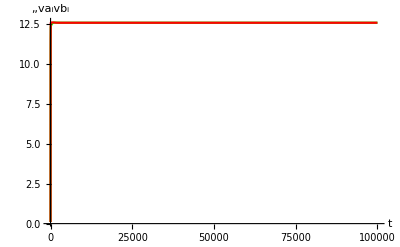

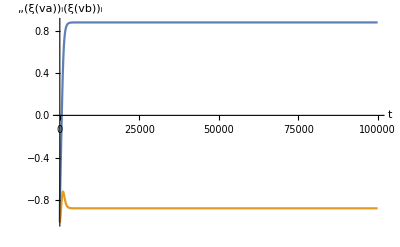

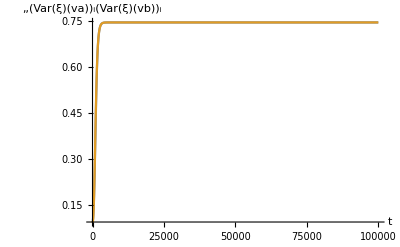

```mathematica
sol=EcoEvoVarSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^5,Verbose->False];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
```

```mathematica
FinalSlice[sol]
```

{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}

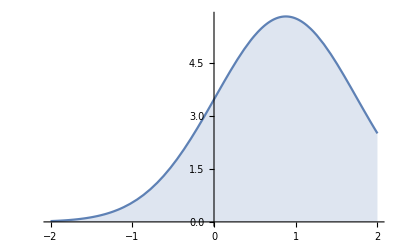

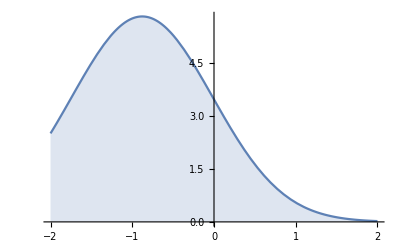

```mathematica
Plot[Evaluate[Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ]/.FinalSlice[sol]],{ξ,-2,2},PlotRange->All,Filling->Axis]
Plot[Evaluate[Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ]/.FinalSlice[sol]],{ξ,-2,2},PlotRange->All,Filling->Axis]
```

invaderGs={Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

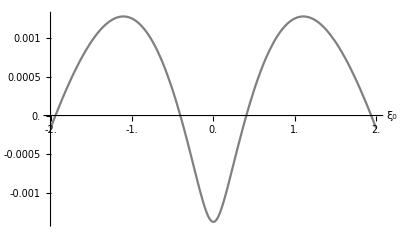

```mathematica
PlotInv[FinalSlice[sol],{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_0→0.74646,(Var[ξ][vb])_0→0.74646,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

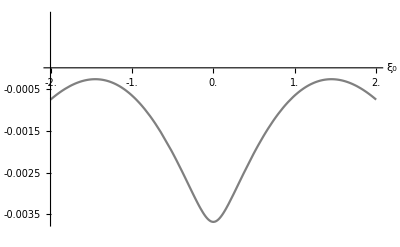

```mathematica
PlotInv[FinalSlice[sol],{Subscript[Var[ξ][va], 0]->0.7464599779746975,Subscript[Var[ξ][vb], 0]->0.7464599779738803},{Subscript[ξ, 0],-2,2}]
```

```mathematica
i=Inv[FinalSlice[sol],{Subscript[Var[ξ][va], 0]->0.7464599779746975,Subscript[Var[ξ][vb], 0]->0.7464599779738803},EqualInvTraits->False];
```

invaderGs={(Var[ξ][va])_0→0.74646,(Var[ξ][vb])_0→0.74646,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

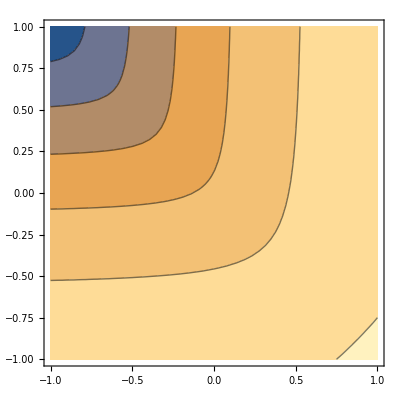

```mathematica
ContourPlot[Evaluate@i,{Subscript[ξ[va], 0],-1,1},{Subscript[ξ[vb], 0],-1,1}]
```

```mathematica
Inv[FinalSlice[sol],{Subscript[ξ[va], 0]->0.878775,Subscript[ξ[vb], 0]->-0.878775},{Subscript[Var[ξ][va], 0]->0.7464599779746975,Subscript[Var[ξ][vb], 0]->0.7464599779738803}]
```

invaderGs={(Var[ξ][va])_0→0.74646,(Var[ξ][vb])_0→0.74646,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-8.68721×10^-10

```mathematica
?SplitSpecies
```

```mathematica
SplitSpecies[FinalSlice[sol],Subscript[v, 1]]
```

Part::partw: Part {2,4} of LookUp[v_1] does not exist.

Set::shape: Lists {EcoEvo`Private`gu$25768,EcoEvo`Private`sp$25768} and LookUp[v_1]⟦{2,4}⟧ are not the same shape.

Table::iterb: Iterator {EcoEvo`Private`trait,EcoEvo`Private`gtraits[EcoEvo`Private`gu$25768]} does not have appropriate bounds.

Table::iterb: Iterator {EcoEvo`Private`var,EcoEvo`Private`gcomps[]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ReplaceAll::reps: {Table[((EcoEvo`Private`var)_(EcoEvo`Private`sp$25768)→EcoEvo`Private`val$_)→(EcoEvo`Private`var)_(EcoEvo`Private`sp$25768)→(EcoEvo`Private`val$)/2,{EcoEvo`Private`var,EcoEvo`Private`gcomps[]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and Table at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

RuleListSubtract[Join[{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}/.Table[((EcoEvo`Private`var)_(EcoEvo`Private`sp$25768)→EcoEvo`Private`val$_)→(EcoEvo`Private`var)_(EcoEvo`Private`sp$25768)→(EcoEvo`Private`val$)/2,{EcoEvo`Private`var,EcoEvo`Private`gcomps[]}],Table[(EcoEvo`Private`var)_(𝒩[EcoEvo`Private`gu$25768]+1)→((EcoEvo`Private`var)_(EcoEvo`Private`sp$25768)/.EcoEvo`Private`tmp$25768),{EcoEvo`Private`var,EcoEvo`Private`gcomps[EcoEvo`Private`gu$25768]}],Table[(EcoEvo`Private`trait)_(𝒩[EcoEvo`Private`gu$25768]+1)→((EcoEvo`Private`trait)_(EcoEvo`Private`sp$25768)/.EcoEvo`Private`tmp$25768)+(EcoEvo`Private`trait/.EcoEvo`Private`dtraits$25768),{EcoEvo`Private`trait,EcoEvo`Private`gtraits[EcoEvo`Private`gu$25768]}]],Table[(EcoEvo`Private`trait)_(EcoEvo`Private`sp$25768)→(EcoEvo`Private`trait/.EcoEvo`Private`dtraits$25768),{EcoEvo`Private`trait,EcoEvo`Private`gtraits[EcoEvo`Private`gu$25768]}]]

```mathematica
FinalSlice[sol]
```

{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}

```mathematica
sol′=EcoEvoVarSim[Join[FinalSlice[sol],{Subscript[Var[ξ][va], 2]->0.7464599749190217,Subscript[Var[ξ][vb], 2]->0.7464599749190216,Subscript[va, 2]->1,Subscript[vb, 2]->1,Subscript[ξ[va], 2]->0.88,Subscript[ξ[vb], 2]->-0.87}],10^5,Verbose->False];
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

alltraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

nonfixedtraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

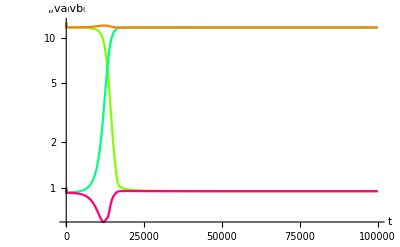

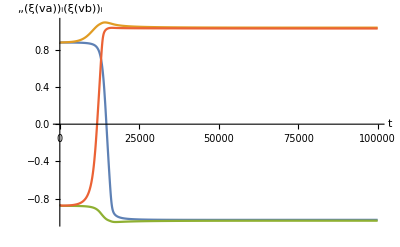

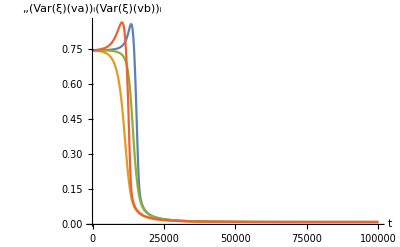

```mathematica
PlotDynamics[sol′,{va,vb},Logged->True]
PlotDynamics[sol′,{ξ[va],ξ[vb]}]
PlotDynamics[sol′,{Var[ξ][va],Var[ξ][vb]}]
```

nonfixedvars={R1a,R1b,R2a,R2b,va_1,va_2,vb_1,vb_2,ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

alltraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

nonfixedtraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

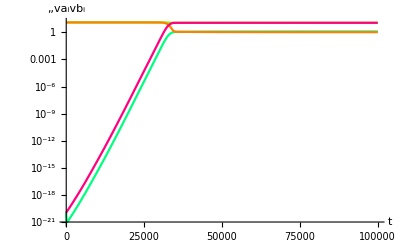

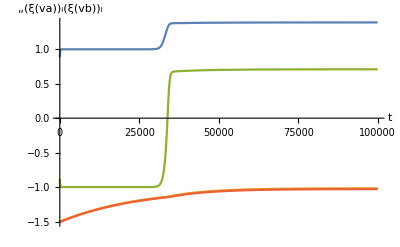

```mathematica
sol2=EcoEvoSim[Join[FinalSlice[sol],{Subscript[va, 2]->10^-20,Subscript[vb, 2]->10^-20,Subscript[ξ[va], 2]->-1.5,Subscript[ξ[vb], 2]->-1.5}],{Subscript[Var[ξ], 2]->0.01},10^5];
PlotDynamics[sol2,{va,vb},Logged->True]
PlotDynamics[sol2,{ξ[va],ξ[vb]}]
```

```mathematica
FinalSlice[sol2]
```

{va_1→11.3232,vb_1→1.05833,va_2→1.25704,vb_2→11.5585,R1a→0.0875804,R1b→0.0514729,R2a→0.054427,R2b→0.086803,ξ[va]_1→1.38272,ξ[vb]_1→0.705775,ξ[va]_2→-1.01348,ξ[vb]_2→-1.02473}

nonfixedvars={R1a,R1b,R2a,R2b,va_0,va_1,vb_0,vb_1,ξ[va]_1,ξ[vb]_1,ξ[va]_0,ξ[vb]_0}

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1,ξ[va]_0,ξ[vb]_0}

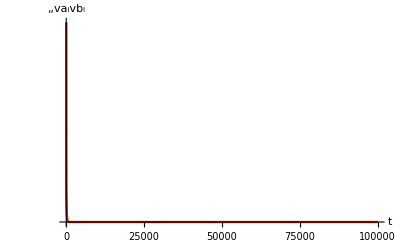

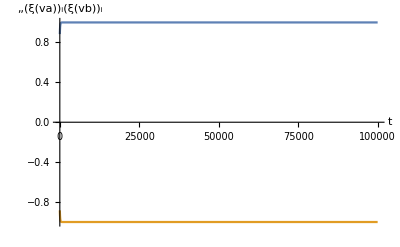

```mathematica
sol0=EcoEvoSim[Join[FinalSlice[sol],{Subscript[va, 0]->10^-20,Subscript[vb, 0]->10^-20,Subscript[ξ[va], 0]->-1.0,Subscript[ξ[vb], 0]->-1.0}],{Subscript[Var[ξ], 0]->0.01},10^5];
PlotDynamics[sol0,{va,vb},Logged->True]
PlotDynamics[sol0,{ξ[va],ξ[vb]}]
```

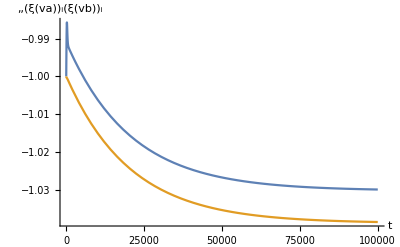

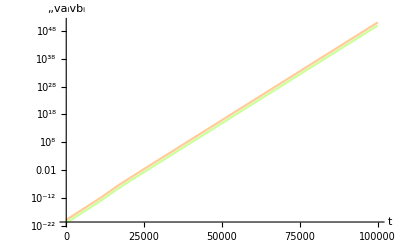

```mathematica
PlotDynamics[sol0,{Subscript[ξ[va], 0],Subscript[ξ[vb], 0]}]
PlotDynamics[sol0,{Subscript[va, 0],Subscript[vb, 0]},Logged->True]
```

```mathematica
FinalSlice[sol0]
```

{va_1→12.595,vb_1→12.595,R1a→0.0882663,R1b→0.0522366,R2a→0.0522366,R2b→0.0882663,ξ[va]_1→0.994887,ξ[vb]_1→-0.994887}

nonfixedvars={R1a,R1b,R2a,R2b,va_1,va_2,vb_1,vb_2,ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

alltraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

nonfixedtraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

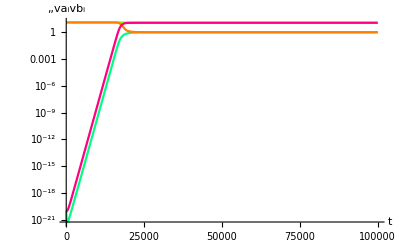

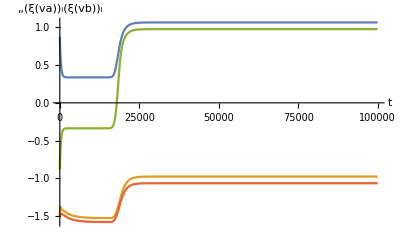

```mathematica
sol3=EcoEvoSim[Join[FinalSlice[sol],{Subscript[va, 2]->10^-20,Subscript[vb, 2]->10^-20,Subscript[ξ[va], 2]->-1.5,Subscript[ξ[vb], 2]->-1.5}],{Var[ξ]->0.1},10^5];
PlotDynamics[sol3,{va,vb},Logged->True]
PlotDynamics[sol3,{ξ[va],ξ[vb]}]
```

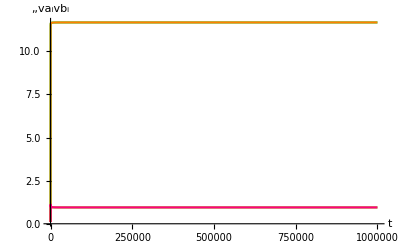

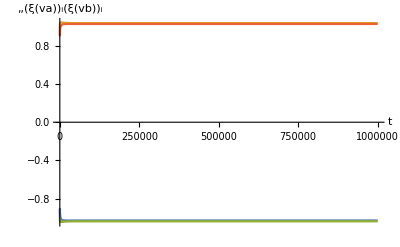

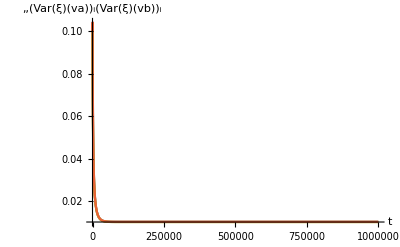

```mathematica
sol=EcoEvoVarSim[{Subscript[ξ, 1]->-1,Subscript[ξ, 2]->1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,Subscript[va, 2]->0.1,Subscript[vb, 2]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^6,Verbose->False];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
```

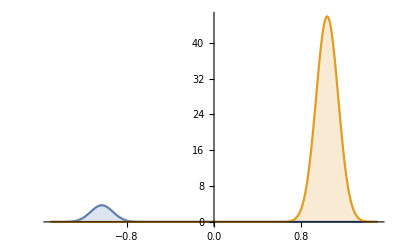

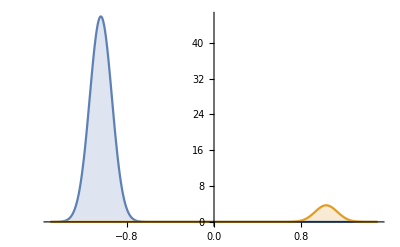

```mathematica
Plot[Evaluate[{Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ],Subscript[va, 2] PDF[NormalDistribution[Subscript[ξ[va], 2],Sqrt[Subscript[Var[ξ][va], 2]]]][ξ]}/.FinalSlice[sol]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
Plot[Evaluate[{Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ],Subscript[vb, 2] PDF[NormalDistribution[Subscript[ξ[vb], 2],Sqrt[Subscript[Var[ξ][vb], 2]]]][ξ]}/.FinalSlice[sol]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
```

```mathematica
FinalSlice[sol]
```

{(Var[ξ][va])_1→0.01041,(Var[ξ][va])_2→0.0103096,(Var[ξ][vb])_1→0.0103096,(Var[ξ][vb])_2→0.01041,va_1→0.947525,vb_1→11.6697,va_2→11.6697,vb_2→0.947525,R1a→0.0868736,R1b→0.0514075,R2a→0.0514075,R2b→0.0868736,ξ[va]_1→-1.0296,ξ[vb]_1→-1.03854,ξ[va]_2→1.03854,ξ[vb]_2→1.0296}

invaderGs={Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

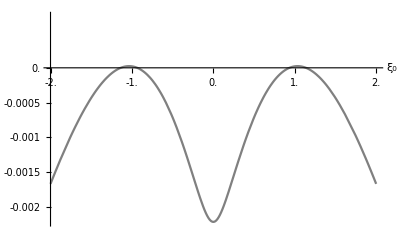

```mathematica
PlotInv[FinalSlice[sol],{Subscript[ξ, 0],-2,2}]
```

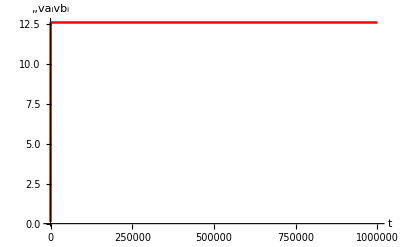

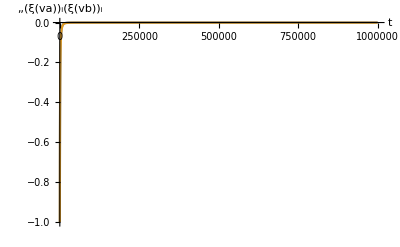

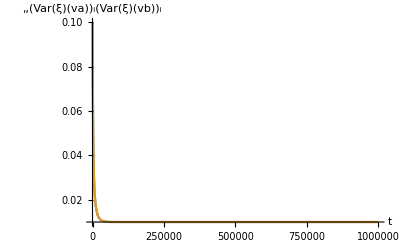

```mathematica
d=10^-1;
sol=EcoEvoVarSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^6];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
```

```mathematica
FinalSlice[sol]
```

{(Var[ξ][va])_1→0.00989219,(Var[ξ][vb])_1→0.00989219,va_1→12.5854,vb_1→12.5854,R1a→0.101034,R1b→0.0404232,R2a→0.0404232,R2b→0.101034,ξ[va]_1→0.000528971,ξ[vb]_1→-0.000528971}

```mathematica
?PlotGuild
```

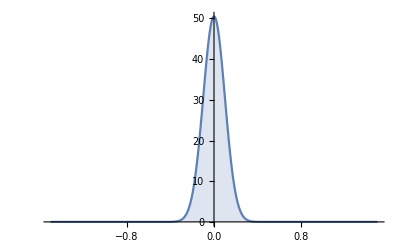

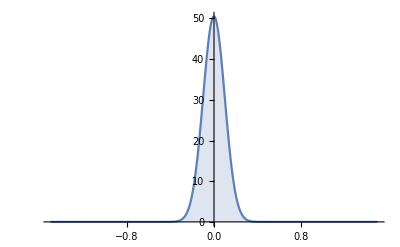

```mathematica
Plot[Evaluate[Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ]/.FinalSlice[sol]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
Plot[Evaluate[Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ]/.FinalSlice[sol]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
```

invaderGs={Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

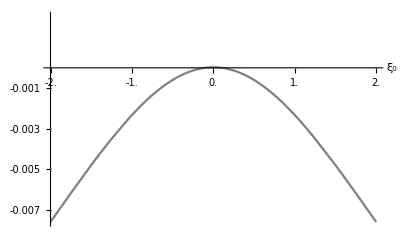

```mathematica
PlotInv[FinalSlice[sol],{Subscript[ξ, 0],-2,2}]
```

### tp

```mathematica
Clear[σμ]
```

```mathematica
SetModel[tp];
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
σμ=0;
```

```mathematica
sol=EcoEvoVarSim[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},{Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0},100,Verbose->True];
```

EcoEvoVarSim: eqns=

{n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-1-0.1 n1_1[t]-2 x[n1]_1[t]-(x[n1]_1[t])^2-(Var[x][n1])_1[t]),n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-1-0.1 n2_1[t]+2 x[n2]_1[t]-(x[n2]_1[t])^2-(Var[x][n2])_1[t]),x[n1]_1'[t]==(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t]+(-2-2 x[n1]_1[t]) (Var[x][n1])_1[t],x[n2]_1'[t]==(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]+(2-2 x[n2]_1[t]) (Var[x][n2])_1[t],(Var[x][n1])_1'[t]==-2 ((Var[x][n1])_1[t])^2+(0.01 n2_1[t] ((-x[n1]_1[t]+x[n2]_1[t])^2-(Var[x][n1])_1[t]+(Var[x][n2])_1[t]))/n1_1[t],(Var[x][n2])_1'[t]==(0.01 n1_1[t] ((x[n1]_1[t]-x[n2]_1[t])^2+(Var[x][n1])_1[t]-(Var[x][n2])_1[t]))/n2_1[t]-2 ((Var[x][n2])_1[t])^2}

EcoEvoVarSim: ics=

{x[n1]_1[0]==-0.1,x[n2]_1[0]==0.2,n1_1[0]==0.1,n2_1[0]==0.1,(Var[x][n1])_1[0]==0,(Var[x][n2])_1[0]==0}

EcoEvoVarSim: unks=

{n1_1,n2_1,x[n1]_1,x[n2]_1,(Var[x][n1])_1,(Var[x][n2])_1}

EcoEvoVarSim: bdwhens=

{}

EcoEvoVarSim: discretevars=

{}

```mathematica
FinalSlice[sol]
```

{(Var[x][n1])_1→0.131421,(Var[x][n2])_1→0.131421,n1_1→8.63579,n2_1→8.63579,x[n1]_1→-0.929289,x[n2]_1→0.929289}

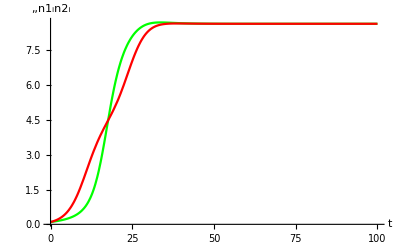

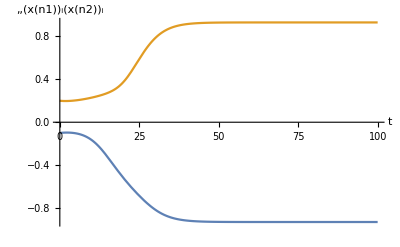

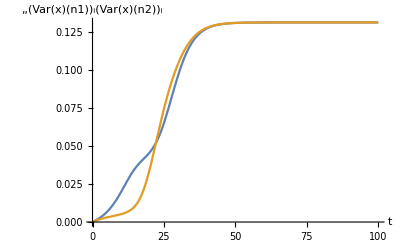

```mathematica
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
PlotDynamics[sol,{Var[x][n1],Var[x][n2]},PlotRange->{0,All}]
```

```mathematica
sol=EcoEvoVarSim[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2,Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1,Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0},100]
```

{(Var[x][n1])_1→InterpolatingFunction[…],(Var[x][n2])_1→InterpolatingFunction[…],n1_1→InterpolatingFunction[…],n2_1→InterpolatingFunction[…],x[n1]_1→InterpolatingFunction[…],x[n2]_1→InterpolatingFunction[…]}

```mathematica
d12=d21=10^-3;
sol=EcoEvoVarSim[
{Subscript[x[n1], 1]->-1,Subscript[x[n2], 1]->-1,Subscript[x[n1], 2]->1,Subscript[x[n2], 2]->1},
{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1,Subscript[n1, 2]->0.1,Subscript[n2, 2]->0.1},
{Subscript[Var[x][n1], 1]->0.1,Subscript[Var[x][n2], 1]->0.1,Subscript[Var[x][n1], 2]->0.1,Subscript[Var[x][n2], 2]->0.1},
10^4];
```

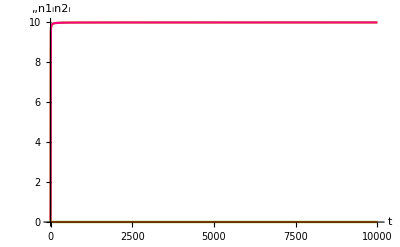

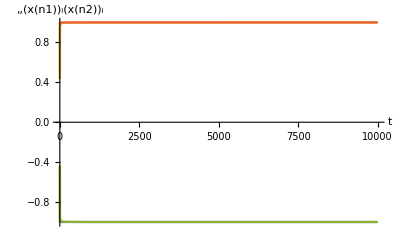

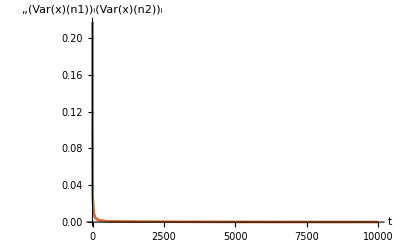

```mathematica
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
PlotDynamics[sol,{Var[x][n1],Var[x][n2]},PlotRange->{0,All}]
```

```mathematica
FinalSlice[sol]
```

{(Var[x][n1])_1→0.0000499835,(Var[x][n1])_2→0.000049986,(Var[x][n2])_1→0.000049986,(Var[x][n2])_2→0.0000499835,n1_1→9.98701,n2_1→0.00249688,n1_2→0.00249688,n2_2→9.98701,x[n1]_1→-1.,x[n2]_1→-0.99995,x[n1]_2→0.99995,x[n2]_2→1.}

```mathematica
d12=d21=0.01;
σμ=0.5;
sol=EcoEvoVarSim[{Subscript[x[n1], 1]->-0.1,Subscript[x[n2], 1]->0.2},{Subscript[n1, 1]->0.1,Subscript[n2, 1]->0.1},{Subscript[Var[x][n1], 1]->0,Subscript[Var[x][n2], 1]->0},100,Verbose->True];
FinalSlice[sol]
```

EcoEvoVarSim: eqns=

{n1_1'[t]==0.99 n1_1[t]+0.01 n2_1[t]+n1_1[t] (-1-0.1 n1_1[t]-2 x[n1]_1[t]-(x[n1]_1[t])^2-(Var[x][n1])_1[t]),n2_1'[t]==0.01 n1_1[t]+0.99 n2_1[t]+n2_1[t] (-1-0.1 n2_1[t]+2 x[n2]_1[t]-(x[n2]_1[t])^2-(Var[x][n2])_1[t]),x[n1]_1'[t]==(0.01 n2_1[t] (-x[n1]_1[t]+x[n2]_1[t]))/n1_1[t]+(-2-2 x[n1]_1[t]) (Var[x][n1])_1[t],x[n2]_1'[t]==(0.01 n1_1[t] (x[n1]_1[t]-x[n2]_1[t]))/n2_1[t]+(2-2 x[n2]_1[t]) (Var[x][n2])_1[t],(Var[x][n1])_1'[t]==0.25-2 ((Var[x][n1])_1[t])^2+(0.01 n2_1[t] ((-x[n1]_1[t]+x[n2]_1[t])^2-(Var[x][n1])_1[t]+(Var[x][n2])_1[t]))/n1_1[t],(Var[x][n2])_1'[t]==0.25+(0.01 n1_1[t] ((x[n1]_1[t]-x[n2]_1[t])^2+(Var[x][n1])_1[t]-(Var[x][n2])_1[t]))/n2_1[t]-2 ((Var[x][n2])_1[t])^2}

EcoEvoVarSim: ics=

{x[n1]_1[0]==-0.1,x[n2]_1[0]==0.2,n1_1[0]==0.1,n2_1[0]==0.1,(Var[x][n1])_1[0]==0,(Var[x][n2])_1[0]==0}

EcoEvoVarSim: unks=

{n1_1,n2_1,x[n1]_1,x[n2]_1,(Var[x][n1])_1,(Var[x][n2])_1}

EcoEvoVarSim: bdwhens=

{}

EcoEvoVarSim: discretevars=

{}

{(Var[x][n1])_1→0.379455,(Var[x][n2])_1→0.379455,n1_1→6.19886,n2_1→6.19886,x[n1]_1→-0.974323,x[n2]_1→0.974323}

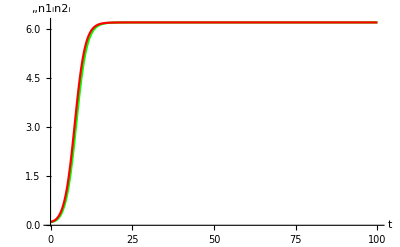

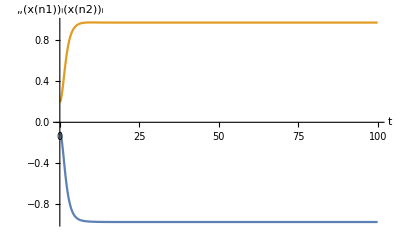

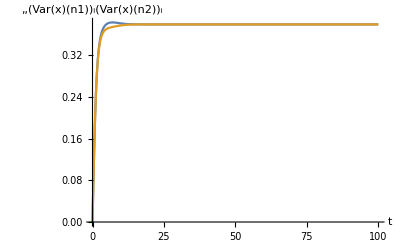

{(Var[x][n1])_1→0.379455,(Var[x][n2])_1→0.379455,n1_1→6.19886,n2_1→6.19886,x[n1]_1→-0.974323,x[n2]_1→0.974323}

```mathematica
PlotDynamics[sol,{n1,n2}]
PlotDynamics[sol,{x[n1],x[n2]}]
PlotDynamics[sol,{Var[x][n1],Var[x][n2]},PlotRange->{0,All}]
FinalSlice[sol]
```

## FindEcoEvoVarEq / *

### jonas1

```mathematica
Clear[a1,a2];
SetModel[jonas1]
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i]

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R2a a2[ξ[va]_i] va_i-1/2 R2a va_i (Var[ξ][va])_i a2''[ξ[va]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R1b a1[ξ[vb]_i] vb_i-1/2 R1b vb_i (Var[ξ][vb])_i a1''[ξ[vb]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R2b a2[ξ[vb]_i] vb_i-1/2 R2b vb_i (Var[ξ][vb])_i a2''[ξ[vb]_i]

```mathematica
a1[ξ_]:=(E^ξ/(1+E^ξ))^α;
a2[ξ_]:=(1-E^ξ/(1+E^ξ))^α;
μ=0.1;
r=1;
K1a=K2b=1;
K1b=K2a=0.4;
c1=c2=1;
α=0.5;
d=10.^-3;
M=5*10^-6;
```

```mathematica
eq=FindEcoEvoVarEq[{Subscript[ξ[va], 1]->1,Subscript[ξ[vb], 1]->-1,Subscript[va, 1]->12,Subscript[vb, 1]->12,R1a->0.01,R1b->0.01,R2a->0.01,R2b->0.01,Var[ξ]->0.7}]
```

{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}

```mathematica
PlotInv[FinalSlice[sol],{Subscript[ξ, 0],-2,2}]
```

-Graphics-

```mathematica
PlotInv[FinalSlice[sol],{Subscript[Var[ξ][va], 0]->0.7464599779746975,Subscript[Var[ξ][vb], 0]->0.7464599779738803},{Subscript[ξ, 0],-2,2}]
```

-Graphics-

```mathematica
Plot[Evaluate[Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
Plot[Evaluate[Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
EcoEvoVarJacobian[eq]
```

{{-0.001,0.001,10.2709,0,6.88208,0,0.0296793,0,-0.0349458,0},{0.001,-0.001,0,6.88208,0,10.2709,0,-0.0296793,0,-0.0349458},{-0.0722932,0,-11.2709,0,0,0,-0.138053,0,0.0386094,0},{0,-0.0277068,0,-7.88208,0,0,0,-0.108373,0,-0.00366355},{-0.0277068,0,0,0,-7.88208,0,0.108373,0,-0.00366355,0},{0,-0.0722932,0,0,0,-11.2709,0,0.138053,0,0.0386094},{0.00013943,-0.00013943,0.0921416,0,-0.126461,0,-0.00418795,0.001,0.00347876,0},{0.00013943,-0.00013943,0,0.126461,0,-0.0921416,0.001,-0.00418795,0,-0.00347876},{-0.000245055,0.000245055,-0.0384676,0,0.00638498,0,0.00519352,-0.0035151,-0.00927771,0.001},{0.000245055,-0.000245055,0,0.00638498,0,-0.0384676,0.0035151,-0.00519352,0.001,-0.00927771}}

```mathematica
EcoEvoVarEigenvalues[eq]
```

{-11.2036,-11.2036,-7.85541,-7.8554,-0.0929133,-0.0908831,-0.0142212,-0.0118852,-0.00457773,-0.00225553}

```mathematica
i=Inv[FinalSlice[sol],{Subscript[Var[ξ][va], 0]->0.7464599779746975,Subscript[Var[ξ][vb], 0]->0.7464599779738803},EqualInvTraits->False];
```

```mathematica
ContourPlot[Evaluate@i,{Subscript[ξ[va], 0],-1,1},{Subscript[ξ[vb], 0],-1,1}]
```

-Graphics-

```mathematica
Inv[FinalSlice[sol],{Subscript[ξ[va], 0]->0.878775,Subscript[ξ[vb], 0]->-0.878775},{Subscript[Var[ξ][va], 0]->0.7464599779746975,Subscript[Var[ξ][vb], 0]->0.7464599779738803}]
```

-8.68721×10^-10

```mathematica
?SplitSpecies
```

```mathematica
SplitSpecies[FinalSlice[sol],Subscript[v, 1]]
```

Part::partw: Part {2,4} of LookUp[v_1] does not exist.

Set::shape: Lists {EcoEvo`Private`gu$25768,EcoEvo`Private`sp$25768} and LookUp[v_1]⟦{2,4}⟧ are not the same shape.

Table::iterb: Iterator {EcoEvo`Private`trait,EcoEvo`Private`gtraits[EcoEvo`Private`gu$25768]} does not have appropriate bounds.

Table::iterb: Iterator {EcoEvo`Private`var,EcoEvo`Private`gcomps[]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ReplaceAll::reps: {Table[((EcoEvo`Private`var)_(EcoEvo`Private`sp$25768)→EcoEvo`Private`val$_)→(EcoEvo`Private`var)_(EcoEvo`Private`sp$25768)→(EcoEvo`Private`val$)/2,{EcoEvo`Private`var,EcoEvo`Private`gcomps[]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and Table at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

RuleListSubtract[Join[{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}/.Table[((EcoEvo`Private`var)_(EcoEvo`Private`sp$25768)→EcoEvo`Private`val$_)→(EcoEvo`Private`var)_(EcoEvo`Private`sp$25768)→(EcoEvo`Private`val$)/2,{EcoEvo`Private`var,EcoEvo`Private`gcomps[]}],Table[(EcoEvo`Private`var)_(𝒩[EcoEvo`Private`gu$25768]+1)→((EcoEvo`Private`var)_(EcoEvo`Private`sp$25768)/.EcoEvo`Private`tmp$25768),{EcoEvo`Private`var,EcoEvo`Private`gcomps[EcoEvo`Private`gu$25768]}],Table[(EcoEvo`Private`trait)_(𝒩[EcoEvo`Private`gu$25768]+1)→((EcoEvo`Private`trait)_(EcoEvo`Private`sp$25768)/.EcoEvo`Private`tmp$25768)+(EcoEvo`Private`trait/.EcoEvo`Private`dtraits$25768),{EcoEvo`Private`trait,EcoEvo`Private`gtraits[EcoEvo`Private`gu$25768]}]],Table[(EcoEvo`Private`trait)_(EcoEvo`Private`sp$25768)→(EcoEvo`Private`trait/.EcoEvo`Private`dtraits$25768),{EcoEvo`Private`trait,EcoEvo`Private`gtraits[EcoEvo`Private`gu$25768]}]]

```mathematica
sol′=EcoEvoVarSim[Join[FinalSlice[sol],{Subscript[Var[ξ][va], 2]->0.7464599749190217,Subscript[Var[ξ][vb], 2]->0.7464599749190216,Subscript[va, 2]->1,Subscript[vb, 2]->1,Subscript[ξ[va], 2]->0.88,Subscript[ξ[vb], 2]->-0.87}],10^5,Verbose->False];
```

```mathematica
PlotDynamics[sol′,{va,vb},Logged->True]
PlotDynamics[sol′,{ξ[va],ξ[vb]}]
PlotDynamics[sol′,{Var[ξ][va],Var[ξ][vb]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol2=EcoEvoSim[Join[FinalSlice[sol],{Subscript[va, 2]->10^-20,Subscript[vb, 2]->10^-20,Subscript[ξ[va], 2]->-1.5,Subscript[ξ[vb], 2]->-1.5}],{Subscript[Var[ξ], 2]->0.01},10^5];
PlotDynamics[sol2,{va,vb},Logged->True]
PlotDynamics[sol2,{ξ[va],ξ[vb]}]
```

-Graphics-

-Graphics-

```mathematica
FinalSlice[sol2]
```

{va_1→11.3232,vb_1→1.05833,va_2→1.25704,vb_2→11.5585,R1a→0.0875804,R1b→0.0514729,R2a→0.054427,R2b→0.086803,ξ[va]_1→1.38272,ξ[vb]_1→0.705775,ξ[va]_2→-1.01348,ξ[vb]_2→-1.02473}

```mathematica
sol0=EcoEvoSim[Join[FinalSlice[sol],{Subscript[va, 0]->10^-20,Subscript[vb, 0]->10^-20,Subscript[ξ[va], 0]->-1.0,Subscript[ξ[vb], 0]->-1.0}],{Subscript[Var[ξ], 0]->0.01},10^5];
PlotDynamics[sol0,{va,vb},Logged->True]
PlotDynamics[sol0,{ξ[va],ξ[vb]}]
```

-Graphics-

-Graphics-

```mathematica
PlotDynamics[sol0,{Subscript[ξ[va], 0],Subscript[ξ[vb], 0]}]
PlotDynamics[sol0,{Subscript[va, 0],Subscript[vb, 0]},Logged->True]
```

-Graphics-

-Graphics-

```mathematica
FinalSlice[sol0]
```

{va_0→9.95232×10^49,vb_0→1.24533×10^51,ξ[va]_0→-1.02993,ξ[vb]_0→-1.03852,va_1→12.595,vb_1→12.595,R1a→0.0882663,R1b→0.0522366,R2a→0.0522366,R2b→0.0882663,ξ[va]_1→0.994887,ξ[vb]_1→-0.994887}

```mathematica
sol3=EcoEvoSim[Join[FinalSlice[sol],{Subscript[va, 2]->10^-20,Subscript[vb, 2]->10^-20,Subscript[ξ[va], 2]->-1.5,Subscript[ξ[vb], 2]->-1.5}],{Var[ξ]->0.1},10^5];
PlotDynamics[sol3,{va,vb},Logged->True]
PlotDynamics[sol3,{ξ[va],ξ[vb]}]
```

-Graphics-

-Graphics-

```mathematica
sol=EcoEvoVarSim[{Subscript[ξ, 1]->-1,Subscript[ξ, 2]->1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,Subscript[va, 2]->0.1,Subscript[vb, 2]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^6,Verbose->False];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate[{Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ],Subscript[va, 2] PDF[NormalDistribution[Subscript[ξ[va], 2],Sqrt[Subscript[Var[ξ][va], 2]]]][ξ]}/.FinalSlice[sol]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
Plot[Evaluate[{Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ],Subscript[vb, 2] PDF[NormalDistribution[Subscript[ξ[vb], 2],Sqrt[Subscript[Var[ξ][vb], 2]]]][ξ]}/.FinalSlice[sol]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
FinalSlice[sol]
```

{(Var[ξ][va])_1→0.01041,(Var[ξ][va])_2→0.0103096,(Var[ξ][vb])_1→0.0103096,(Var[ξ][vb])_2→0.01041,va_1→0.947525,vb_1→11.6697,va_2→11.6697,vb_2→0.947525,R1a→0.0868736,R1b→0.0514075,R2a→0.0514075,R2b→0.0868736,ξ[va]_1→-1.0296,ξ[vb]_1→-1.03854,ξ[va]_2→1.03854,ξ[vb]_2→1.0296}

```mathematica
PlotInv[FinalSlice[sol],{Subscript[ξ, 0],-2,2}]
```

-Graphics-

```mathematica
d=10^-1;
sol=EcoEvoVarSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^6];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
FinalSlice[sol]
```

{(Var[ξ][va])_1→0.00989219,(Var[ξ][vb])_1→0.00989219,va_1→12.5854,vb_1→12.5854,R1a→0.101034,R1b→0.0404232,R2a→0.0404232,R2b→0.101034,ξ[va]_1→0.000528971,ξ[vb]_1→-0.000528971}

```mathematica
?PlotGuild
```

```mathematica
Plot[Evaluate[Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ]/.FinalSlice[sol]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
Plot[Evaluate[Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ]/.FinalSlice[sol]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol],{Subscript[ξ, 0],-2,2}]
```

-Graphics-

### tp

```mathematica
SetModel[tp];
```

```mathematica
b=1;
d0=0.1;
d1[x_]:=(x+1)^2
d2[x_]:=(x-1)^2
d12=d21=0.01;
σμ=0;
```

```mathematica
(*debug=True;*)
eq=FindEcoEvoVarEq[{Subscript[Var[x][n1], 1]->0.1,Subscript[Var[x][n2], 1]->0.1,Subscript[n1, 1]->10,Subscript[n2, 1]->10,Subscript[x[n1], 1]->-0.9,Subscript[x[n2], 1]->0.9},Verbose->True]
(*debug=False;*)
```

FindEcoEvoVarEq: eqns=

{0==0.99 n1_1+0.01 n2_1+n1_1 (-1-0.1 n1_1-2 x[n1]_1-x[n1]_1^2-(Var[x][n1])_1),0==0.01 n1_1+0.99 n2_1+n2_1 (-1-0.1 n2_1+2 x[n2]_1-x[n2]_1^2-(Var[x][n2])_1),0==(0.01 n2_1 (-x[n1]_1+x[n2]_1))/n1_1+(-2-2 x[n1]_1) (Var[x][n1])_1,0==(0.01 n1_1 (x[n1]_1-x[n2]_1))/n2_1+(2-2 x[n2]_1) (Var[x][n2])_1,0==-2 (Var[x][n1])_1^2+(0.01 n2_1 ((-x[n1]_1+x[n2]_1)^2-(Var[x][n1])_1+(Var[x][n2])_1))/n1_1,0==(0.01 n1_1 ((x[n1]_1-x[n2]_1)^2+(Var[x][n1])_1-(Var[x][n2])_1))/n2_1-2 (Var[x][n2])_1^2}

FindEcoEvoVarEq: unksics=

{{n1_1,10},{n2_1,10},{x[n1]_1,-0.9},{x[n2]_1,0.9},{(Var[x][n1])_1,0.1},{(Var[x][n2])_1,0.1}}

{(Var[x][n1])_1→0.131421,(Var[x][n2])_1→0.131421,n1_1→8.63579,n2_1→8.63579,x[n1]_1→-0.929289,x[n2]_1→0.929289}

```mathematica
EcoEvoVarJacobian[eq]//MatrixForm
```

(-0.873579 | 0.01 | -1.22128 | 0 | -8.63579 | 0
0.01 | -0.873579 | 0 | 1.22128 | 0 | -8.63579
-0.00215218 | 0.00215218 | -0.272843 | 0.01 | -0.141421 | 0
-0.00215218 | 0.00215218 | 0.01 | -0.272843 | 0 | 0.141421
-0.004 | 0.004 | -0.0371716 | 0.0371716 | -0.535685 | 0.01
0.004 | -0.004 | -0.0371716 | 0.0371716 | 0.01 | -0.535685)

```mathematica
EcoEvoVarEigenvalues[eq]
```

{-1.03518,-0.863579,-0.563188,-0.395115,-0.261814,-0.24534}

```mathematica
σμ=0.5;
eq=FindEcoEvoVarEq[{Subscript[Var[x][n1], 1]->0.1,Subscript[Var[x][n2], 1]->0.1,Subscript[n1, 1]->10,Subscript[n2, 1]->10,Subscript[x[n1], 1]->-0.9,Subscript[x[n2], 1]->0.9}]
EcoEvoVarEigenvalues[eq]
```

{(Var[x][n1])_1→0.379455,(Var[x][n2])_1→0.379455,n1_1→6.19886,n2_1→6.19886,x[n1]_1→-0.974323,x[n2]_1→0.974323}

{-1.61605,-1.5232,-0.773532,-0.766643,-0.619886,-0.553927}

## adlv

```mathematica
GaussianIntegral[func_,{x_,mean_,var_}]:=Expectation[func,x\[Distributed]NormalDistribution[mean,Sqrt[var]]]
```

```mathematica
GaussianIntegralApprox[func_,{x_,mean_,var_}]:=(func+var/2 D[func,{x,2}])/.x->mean
```

```mathematica
GaussianIntegral[a[Subscript[x, i],x] Subscript[n, j],{x,Subscript[x, j],Subscript[Var[x], j]}]
```

Expectation[a[x_i,x] n_j,x\[Distributed]NormalDistribution[x_j,√(Var[x]_j)]]

```mathematica
GaussianIntegral[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],Subscript[x, j]]
```

GaussianIntegral[a[x_i,x_j] n_j,x_j]

```mathematica
GaussianIntegralApprox[a[Subscript[x, i],x′] Subscript[n, j],{x′,Subscript[x, j],Subscript[Var[x], j]}]
```

a[x_i,x_j] n_j+1/2 n_j Var[x]_j a^(0,2)[x_i,x_j]

```mathematica
a[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σ^2);
```

```mathematica
GaussianIntegral[a[Subscript[x, i],x′] Subscript[n, j],{x′,Subscript[x, j],Subscript[Var[x], j]}]
```

(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(1+(Var[x]_j)/σ^2))

```mathematica
Simplify@GaussianIntegral[a[Subscript[x, i],x′] Subscript[n, j],{x′,Subscript[x, j],Subscript[Var[x], j]}]
```

(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(1+(Var[x]_j)/σ^2))

```mathematica
FullSimplify@GaussianIntegralApprox[a[Subscript[x, i],x′] Subscript[n, j],{x′,Subscript[x, j],Subscript[Var[x], j]}]
```

(ⅇ^(-(x_i-x_j)^2/(2 σ^2)) n_j (2 σ^4-(σ+x_i-x_j) (σ-x_i+x_j) Var[x]_j))/(2 σ^4)

```mathematica
GaussianIntegral[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],{Subscript[x, j],Subscript[x̄, j],Subscript[Var[x], j]}]
```

(ⅇ^(-(x_i-(x̄)_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(1+(Var[x]_j)/σ^2))

```mathematica
Inactivate[{
{{Subscript[n, i]⇒∅},Sum[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],{j,Subscript[𝒩, n]}] Subscript[n, i]},
{{0 Subscript[n, i]⇒Subscript[n, i]},r[Subscript[x, i]] Subscript[n, i],NormalDistribution[0,σμ]}
},Sum]/.Inactive[Sum][stuff___,{ind_,𝒩[gu_]}]:>Sum[GaussianIntegral[(stuff/.Subscript[x, ind]->Subscript[unk[x], ind]),{Subscript[unk[x], ind],Subscript[x, ind],Subscript[Var[x], ind]}],{ind,𝒩[gu]},Method->"Procedural"]
```

{{{n_i⇒∅},n_i Sum[(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(1+(Var[x]_j)/σ^2)),{j,𝒩[n]},Method→Procedural]},{{0 n_i⇒n_i},r[x_i] n_i,NormalDistribution[0,σμ]}}

```mathematica
Inactivate[{
{{Subscript[n, i]⇒∅},Sum[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],{j,Subscript[𝒩, n]}] Subscript[n, i]},
{{0 Subscript[n, i]⇒Subscript[n, i]},r[Subscript[x, i]] Subscript[n, i],NormalDistribution[0,σμ]}
},Sum]/.Inactive[Sum][stuff___,{ind_,𝒩[gu_]}]:>Sum[GaussianIntegral[(stuff/.Subscript[x, ind]->Subscript[unk[x], ind]),{Subscript[unk[x], ind],Subscript[x, ind],Subscript[Var[x], ind]}]/.Subscript[unk[x], ind]->Subscript[x, ind],{ind,𝒩[gu]},Method->"Procedural"]
```

{{{n_i⇒∅},n_i Sum[(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(1+(Var[x]_j)/σ^2)),{j,𝒩[n]},Method→Procedural]},{{0 n_i⇒n_i},r[x_i] n_i,NormalDistribution[0,σμ]}}

```mathematica
Clear[a,r];
```

```mathematica
(* raw model *)
(*SetModel[{
Guild[n]->{Traits->{x}},
Transitions:>{
{{Subscript[n, i]⇒∅},Sum[a[Subscript[x, i],Subscript[x, j]] Subscript[n, j],{j,Subscript[𝒩, n]}] Subscript[n, i]},
{{0 Subscript[n, i]⇒Subscript[n, i]},r[Subscript[x, i]] Subscript[n, i],NormalDistribution[0,σμ]}
},
Parameters:>{σμ>=0,σ>=0}
}]*)
```

```mathematica
(* based on full gaussian integral *)
debug=True;
SetModel[{
Guild[n]->{Traits->{x}},
Transitions:>{
{{0 Subscript[n, i]⇒Subscript[n, i]},r[Subscript[x, i]] Subscript[n, i],NormalDistribution[0,σμ]},
{{Subscript[n, i]⇒∅},Subscript[n, i] Sum[(ⅇ^(-(Subscript[x, i]-Subscript[x, j])^2/(2 (σ^2+Subscript[Var[x], j]))) Subscript[n, j])/(√(σ^2/(σ^2+Subscript[Var[x], j]))),{j,Subscript[𝒩, n]}]}
},
Parameters:>{σμ>=0,σ>=0}
}]
debug=False;
```

{sourcec,source,destc,dest}={0,n,1,n}

sourcetraits={x̲}

sourceG={{Var[x]_i}}

fsource=0

dfsource={0}

d2fsource={{0}}

fsource′=0

dfsource′={0}

desttraits={x̲}

destG={{Var[x]_i}}

fdest=r[x̲]

fdest′=r[x̲]+1/2 Var[x]_i r''[x̲]

dfdest′={r'[x̲]+1/2 Var[x]_i r^(3)[x̲]}

{sourcec,source,destc,dest}={1,n,1,∅}

sourcetraits={x̲}

sourceG={{Var[x]_i}}

fsource=-Sum[(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j))),{j,𝒩[n]},Method→Procedural]

dfsource={-Sum[-(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲))/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)),{j,𝒩[n]},Method→Procedural]}

d2fsource={{-Sum[-(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j))+(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲)^2)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2),{j,𝒩[n]},Method→Procedural]}}

fsource′=-Sum[(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j))),{j,𝒩[n]},Method→Procedural]-1/2 Var[x]_i Sum[-(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j))+(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲)^2)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2),{j,𝒩[n]},Method→Procedural]

dfsource′={-Sum[-(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲))/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)),{j,𝒩[n]},Method→Procedural]-1/2 Var[x]_i Sum[(3 ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲))/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2)-(ⅇ^(-(-x_j+x̲)^2/(2 (σ^2+Var[x]_j))) n_j (-x_j+x̲)^3)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^3),{j,𝒩[n]},Method→Procedural]}

constructing dndt[n]...

constructing dxdt[n]...

constructing dGdt[n]...

```mathematica
(* see <https://mathematica.stackexchange.com/a/213105> by Bob Hanlon *)
sumRule=c1_. Sum[expr1_,iter_List,opts___]+c2_. Sum[expr2_,iter_List,opts___]:>Sum[c1 expr1+c2 expr2,iter,opts];
```

```mathematica
EcoEvo`Private`dndt[n]
```

n_i (-Sum[(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j))),{j,𝒩[n]},Method→Procedural]-1/2 Var[x]_i Sum[(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j)^2)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2)-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)),{j,𝒩[n]},Method→Procedural])+n_i (r[x_i]+1/2 Var[x]_i r''[x_i])

```mathematica
Simplify[EcoEvo`Private`dndt[n]]
```

$Aborted

```mathematica
EcoEvo`Private`dndt[n]/.sumRule
```

n_i Sum[-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)))-1/2 Var[x]_i ((ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j)^2)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2)-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j))),{j,𝒩[n]},Method→Procedural]+n_i (r[x_i]+1/2 Var[x]_i r''[x_i])

```mathematica
Simplify[EcoEvo`Private`dndt[n]/.sumRule]
```

n_i (r[x_i]+Sum[-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(σ √(1/(σ^2+Var[x]_j)))-1/2 Var[x]_i (-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j √(1/(σ^2+Var[x]_j)))/σ+(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j)^2 (1/(σ^2+Var[x]_j))^(3/2))/σ),{j,𝒩[n]},Method→Procedural]+1/2 Var[x]_i r''[x_i])

```mathematica
EcoEvo`Private`dxdt[n]
```

{Var[x]_i (-Sum[-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j))/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)),{j,𝒩[n]},Method→Procedural]-1/2 Var[x]_i Sum[-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j)^3)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^3)+(3 ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j))/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2),{j,𝒩[n]},Method→Procedural])+Var[x]_i (r'[x_i]+1/2 Var[x]_i r^(3)[x_i])}

```mathematica
EcoEvo`Private`dGdt[n]
```

{{-Var[x]_i^2 Sum[(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j (x_i-x_j)^2)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)^2)-(ⅇ^(-(x_i-x_j)^2/(2 (σ^2+Var[x]_j))) n_j)/(√(σ^2/(σ^2+Var[x]_j)) (σ^2+Var[x]_j)),{j,𝒩[n]},Method→Procedural]+Var[x]_i^2 r''[x_i]+σμ^2 (r[x_i]+1/2 Var[x]_i r''[x_i])}}

```mathematica
EcoEqns[{Subscript[𝒩, n]->1}]
TraitEqns[{Subscript[𝒩, n]->1}]
VarEqns[{Subscript[𝒩, n]->1}]
```

{n_1'[t]==n_1[t] (-n_1[t]/(√(σ^2/(σ^2+Var[x]_1[t])))+(n_1[t] Var[x]_1[t])/(2 √(σ^2/(σ^2+Var[x]_1[t])) (σ^2+Var[x]_1[t])))+n_1[t] (r[x_1[t]]+1/2 Var[x]_1[t] r''[x_1[t]])}

{x_1'[t]==Var[x]_1[t] (r'[x_1[t]]+1/2 Var[x]_1[t] r^(3)[x_1[t]])}

{Var[x]_1'[t]==(n_1[t] (Var[x]_1[t])^2)/(√(σ^2/(σ^2+Var[x]_1[t])) (σ^2+Var[x]_1[t]))+(Var[x]_1[t])^2 r''[x_1[t]]+σμ^2 (r[x_1[t]]+1/2 Var[x]_1[t] r''[x_1[t]])}

```mathematica
a[xi_,xj_]:=E^(-1/2*(xi-xj)^2/σ^2);
r[x_]:=1-x^2;
```

```mathematica
p[xav_,σ_][x_]:=Evaluate@PDF[NormalDistribution[xav,σ]][x]
```

```mathematica
Assuming[σ>=0&&σi>=0&&σj>=0,Integrate[p[xi,σi][xi′]a[xi′,xj′]p[xj,σj][xj′],{xi′,-∞,∞},{xj′,-∞,∞}]]
```

(ⅇ^(-(xi-xj)^2/(2 (σ^2+σi^2+σj^2))) σ)/(√(σ^2+σi^2+σj^2))

```mathematica
ClearParameters
```

```mathematica
σ=10.0;
σμ=10^-2;
```

```mathematica
EcoEqns[{Subscript[x, 1]->0}]
```

{n_1'[t]==-1/2 n_1[t] (2 (-1+(0.1 n_1[t])/(√(1/(100.+Var[x]_1[t]))))+Var[x]_1[t] (2-0.1 n_1[t] √(1/(100.+Var[x]_1[t]))))}

```mathematica
EcoEqns[{Subscript[x, 1]->0}]
```

{n_1'[t]==n_1[t] (1-Var[x]_1[t])+n_1[t] (-(0.1 n_1[t])/(√(1/(100.+Var[x]_1[t])))-1/2 Var[x]_1[t] (-0.1 n_1[t] √(1/(100.+Var[x]_1[t]))+0. (1/(100.+Var[x]_1[t]))^(3/2)))}

```mathematica
sol=EcoSim[{Subscript[x, 1]->0},{Subscript[n, 1]->0.1},10,Verbose->True]
```

sol=NDSolve[{n_1'[t]==n_1[t]-1. n_1[t]^2,n_1[0]==0.1},{n_1},{t,0,10}]⟦1⟧

{n_1→InterpolatingFunction[…]}

```mathematica
TraitEqns[{Subscript[n, 1]->Subscript[n, 1]},{Subscript[Var[x], 1]->0.01}]
```

{x_1'[t]==0.-0.02 x_1[t]}

```mathematica
sol=EcoEvoSim[{Subscript[x, 1]->-0.9},{Subscript[n, 1]->0.1},{Subscript[Var[x], 1]->0.1},100,Verbose->True]
FinalSlice[sol]
```

EcoEvoSim: eqns=

{n_1'[t]==(-0.05 (0.-0.009995 n_1[t])-1.0005 n_1[t]) n_1[t]+n_1[t] (0.9-x_1[t]^2),x_1'[t]==0.-0.2 x_1[t]}

EcoEvoSim: ics=

{x_1[0]==-0.9,n_1[0]==0.1}

EcoEvoSim: unks=

{n_1,x_1}

EcoEvoSim: bdwhens=

{}

EcoEvoSim: discretevars=

{}

{n_1→InterpolatingFunction[…],x_1→InterpolatingFunction[…]}

{n_1→0.9,x_1→-9.42553×10^-10}

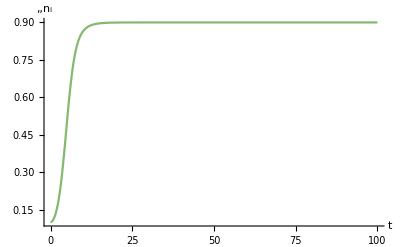

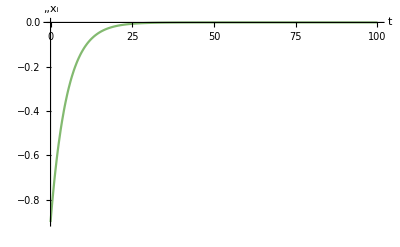

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
```

```mathematica
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.9},{Subscript[n, 1]->0.1},{Subscript[Var[x], 1]->0},500,Verbose->True]
FinalSlice[sol]
```

EcoEvoVarSim: eqns=

{n_1'[t]==n_1[t] (1-x_1[t]^2-Var[x]_1[t])+n_1[t] (-(0.1 n_1[t])/(√(1/(100.+Var[x]_1[t])))-1/2 Var[x]_1[t] (-0.1 n_1[t] √(1/(100.+Var[x]_1[t]))+0. (1/(100.+Var[x]_1[t]))^(3/2))),x_1'[t]==-2 x_1[t] Var[x]_1[t]+Var[x]_1[t] (0. √(1/(100.+Var[x]_1[t]))-1/2 Var[x]_1[t] (0. (1/(100.+Var[x]_1[t]))^(3/2)+0. (1/(100.+Var[x]_1[t]))^(5/2))),Var[x]_1'[t]==(1-x_1[t]^2-Var[x]_1[t])/10000-2 (Var[x]_1[t])^2+0.1 n_1[t] (Var[x]_1[t])^2 √(1/(100.+Var[x]_1[t]))}

EcoEvoVarSim: ics=

{x_1[0]==-0.9,n_1[0]==0.1,Var[x]_1[0]==0}

EcoEvoVarSim: unks=

{n_1,x_1,Var[x]_1}

EcoEvoVarSim: bdwhens=

{}

EcoEvoVarSim: discretevars=

{}

{Var[x]_1→InterpolatingFunction[…],n_1→InterpolatingFunction[…],x_1→InterpolatingFunction[…]}

{Var[x]_1→0.00706259,n_1→0.992912,x_1→-0.00492873}

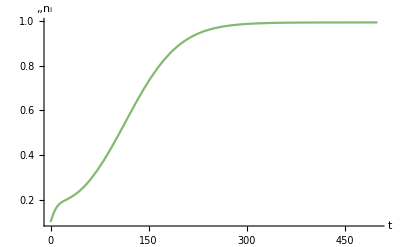

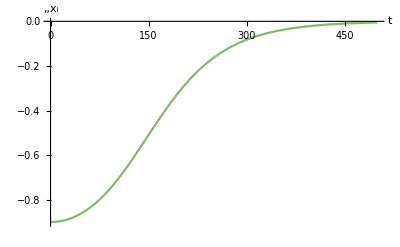

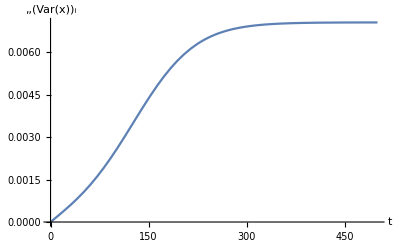

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

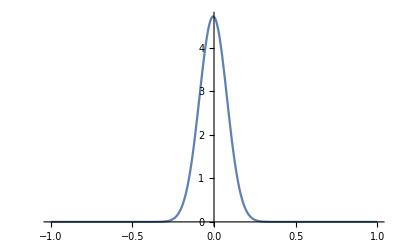

```mathematica
Plot[Evaluate[Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x]/.FinalSlice[sol]],{x,-1,1},PlotRange->All]
```

```mathematica
frames=Table[
Plot[Evaluate[Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x]/.Slice[sol,t]],{x,-1,1},PlotRange->{0,5},PlotLabel->t]
,{t,0,500,10}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

```mathematica
ListAnimate[frames]
```

```mathematica
σ=0.72;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.9,Subscript[x, 2]->0.9},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0,Subscript[Var[x], 2]->0},2000]
FinalSlice[sol]
```

{Var[x]_1→InterpolatingFunction[…],Var[x]_2→InterpolatingFunction[…],n_1→InterpolatingFunction[…],n_2→InterpolatingFunction[…],x_1→InterpolatingFunction[…],x_2→InterpolatingFunction[…]}

{Var[x]_1→0.0245486,Var[x]_2→0.0245486,n_1→0.487595,n_2→0.487595,x_1→-4.16735×10^-6,x_2→4.16735×10^-6}

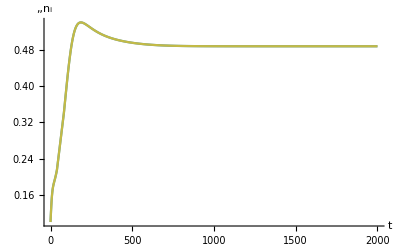

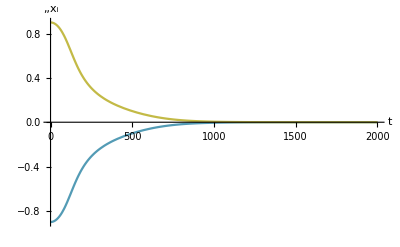

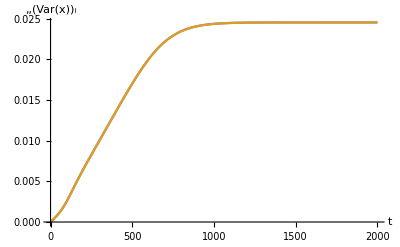

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

```mathematica
σ=0.65;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.9,Subscript[x, 2]->0.9},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0,Subscript[Var[x], 2]->0},2000];
FinalSlice[sol]
```

{Var[x]_1→0.0807618,Var[x]_2→0.0807618,n_1→0.457867,n_2→0.457867,x_1→7.19818×10^-11,x_2→-7.19818×10^-11}

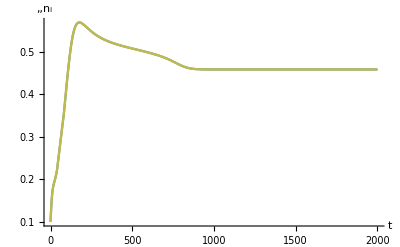

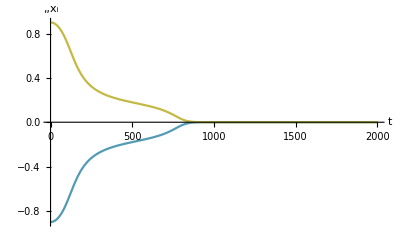

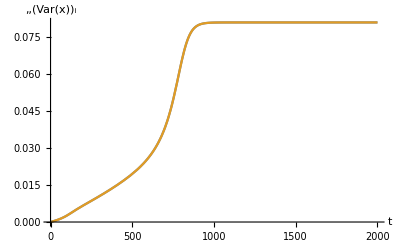

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

```mathematica
σ=0.4;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.9,Subscript[x, 2]->0.89},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0.01,Subscript[Var[x], 2]->0.01},2000];
FinalSlice[sol]
```

{Var[x]_1→0.139689,Var[x]_2→0.347769,n_1→0.0161505,n_2→0.548879,x_1→9.20181×10^-12,x_2→5.84887×10^-13}

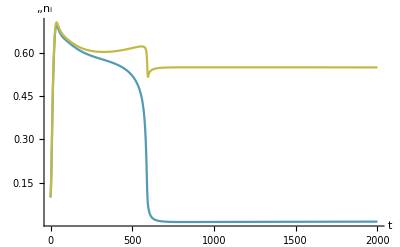

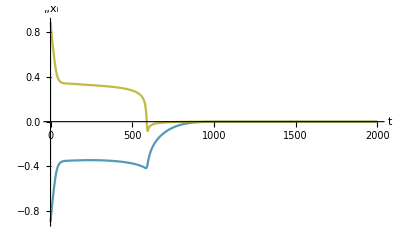

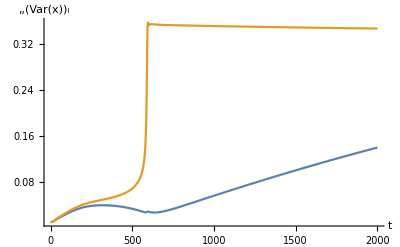

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

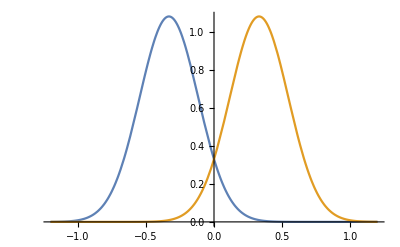

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.FinalSlice[sol]],{x,-1.2,1.2},PlotRange->All]
```

```mathematica
eq=FindEcoEvoVarEq[FinalSlice[sol]]
```

{Var[x]_1→0.0461595,Var[x]_2→0.0461595,n_1→0.582354,n_2→0.582354,x_1→-0.330853,x_2→0.330853}

```mathematica
EcoEvoVarEigenvalues[eq]
```

{-0.854316,-0.383811,-0.132437,-0.0827446,-0.00824879,0.00710878}

```mathematica
eq=FindEcoEvoVarEq[{Subscript[n, 1]->0.5,Subscript[n, 2]->0.5,Subscript[x, 1]->-0.3,Subscript[x, 2]->0.3,Subscript[Var[x], 1]->0.05,Subscript[Var[x], 2]->0.05}]
```

{Var[x]_1→0.0581323,Var[x]_2→0.0581323,n_1→0.54924,n_2→0.54924,x_1→-0.314363,x_2→0.314363}

```mathematica
EcoEvoVarEigenvalues[eq]
```

{-0.84646,-0.338634,-0.151261,-0.114782,0.0154427,0.0122013}

```mathematica
sol=EcoEvoVarSim[RuleListTweak[eq,Subscript[x, 1],0.01],20000];
FinalSlice[sol]
```

{Var[x]_1→0.340101,Var[x]_2→0.340072,n_1→0.427456,n_2→0.138121,x_1→3.34724×10^-28,x_2→1.74973×10^-27}

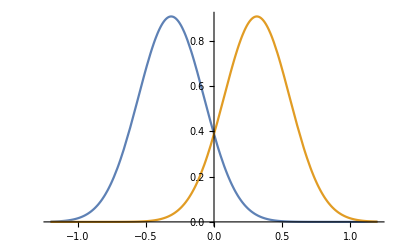

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.eq],{x,-1.2,1.2},PlotRange->All]
```

```mathematica
sol=EcoEvoVarSim[eq,1000];
FinalSlice[sol]
```

{Var[x]_1→0.0581323,Var[x]_2→0.0581323,n_1→0.54924,n_2→0.54924,x_1→-0.314363,x_2→0.314363}

```mathematica
σ=0.01;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.9,Subscript[x, 2]->0.89},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0.01,Subscript[Var[x], 2]->0.01},200];
FinalSlice[sol]
```

{Var[x]_1→0.504129,Var[x]_2→0.495672,n_1→0.00714138,n_2→0.00699957,x_1→-3.6079×10^-22,x_2→-3.57031×10^-22}

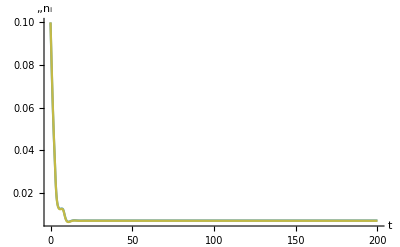

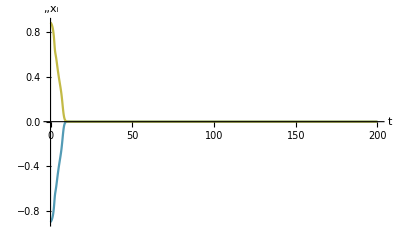

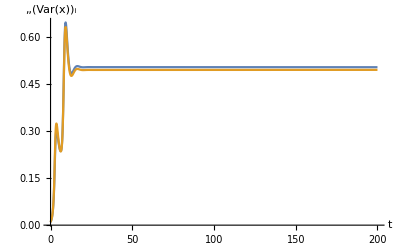

```mathematica
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

```mathematica
σμ=10^-4;
```

{Var[x]_1→0.000220335,Var[x]_2→0.000220335,n_1→0.529372,n_2→0.529372,x_1→-0.217868,x_2→0.217868}

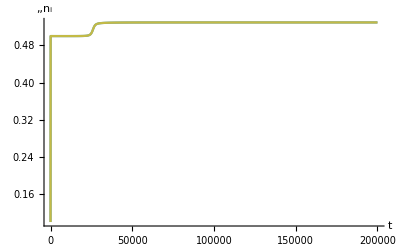

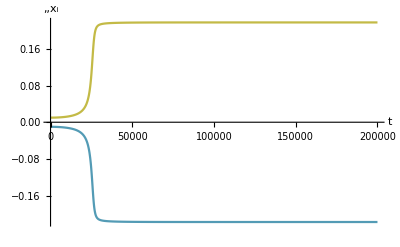

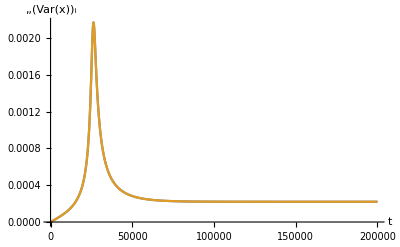

```mathematica
σ=0.65;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.01,Subscript[x, 2]->0.01},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0,Subscript[Var[x], 2]->0},200000];
FinalSlice[sol]
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

General::munfl: Exp[-2188.68] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4561.72] is too small to represent as a normalized machine number; precision may be lost.

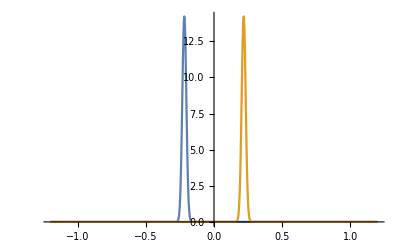

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.FinalSlice[sol]],{x,-1.2,1.2},PlotRange->All]
```

{Var[x]_1→0.250002,n_1→0.707104,x_1→-6.04351×10^-36}

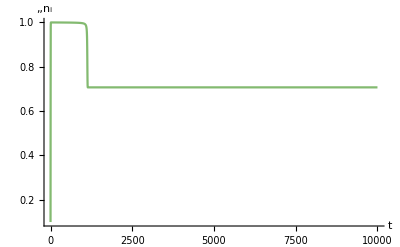

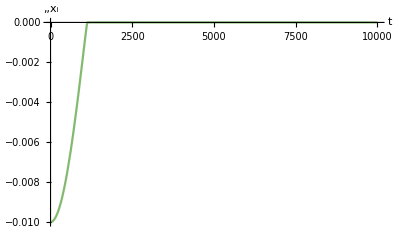

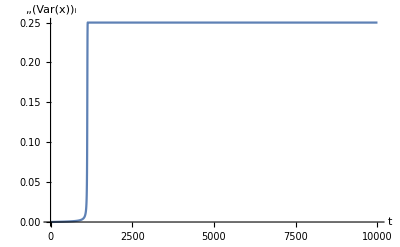

```mathematica
σμ=10^-3;
σ=0.5;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.01,Subscript[n, 1]->0.1,Subscript[Var[x], 1]->0},10000];
FinalSlice[sol]
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

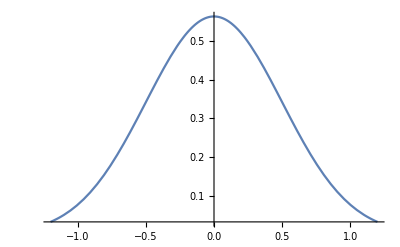

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x]}/.FinalSlice[sol]],{x,-1.2,1.2},PlotRange->All]
```

{Var[x]_1→0.00164603,Var[x]_2→0.00164603,n_1→0.629711,n_2→0.629711,x_1→-0.339619,x_2→0.339619}

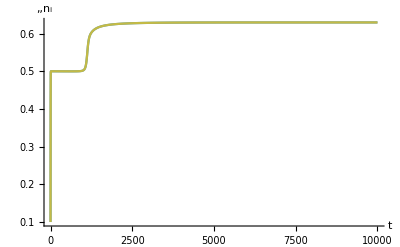

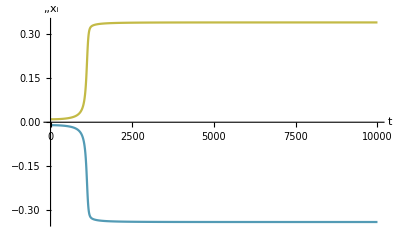

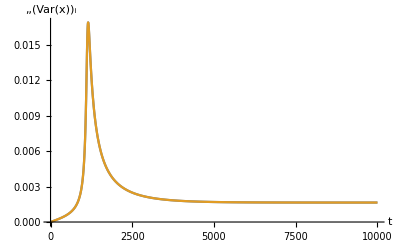

```mathematica
σμ=10^-3;
σ=0.5;
sol=EcoEvoVarSim[{Subscript[x, 1]->-0.01,Subscript[x, 2]->0.01},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0,Subscript[Var[x], 2]->0},10000];
FinalSlice[sol]
PlotDynamics[sol,n]
PlotDynamics[sol,x]
PlotDynamics[sol,{Var[x]},PlotRange->{0,All}]
```

General::munfl: Exp[-720.] is too small to represent as a normalized machine number; precision may be lost.

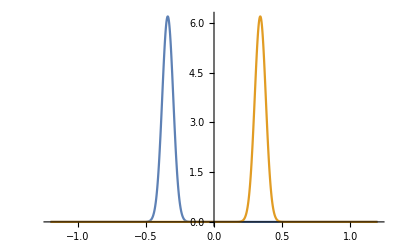

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.FinalSlice[sol]],{x,-1.2,1.2},PlotRange->All]
```

```mathematica
eq=FindEcoEvoVarEq[FinalSlice[sol]]
EcoEvoVarEigenvalues[eq]
```

{Var[x]_1→0.00164581,Var[x]_2→0.00164581,n_1→0.629711,n_2→0.629711,x_1→-0.33962,x_2→0.33962}

{-0.883863,-0.378441,-0.00514567,-0.00147206,-0.00107074,-0.000899443}

{Var[x]_1→0.00329039,Var[x]_2→0.00329039,n_1→0.625715,n_2→0.625715,x_1→-0.338193,x_2→0.338193}

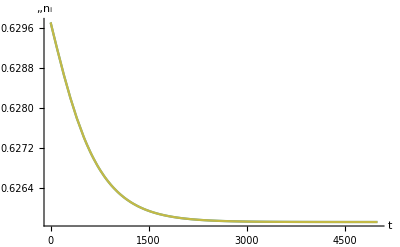

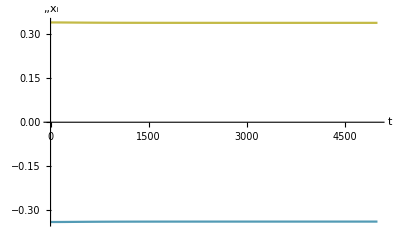

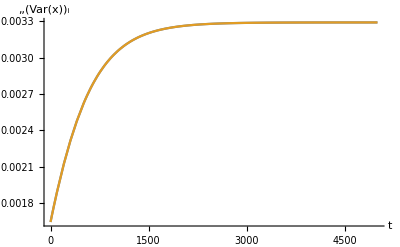

```mathematica
σμ=2 10^-3;
σ=0.5;
sol2=EcoEvoVarSim[eq,5000];
FinalSlice[sol2]
PlotDynamics[sol2,n]
PlotDynamics[sol2,x]
PlotDynamics[sol2,{Var[x]},PlotRange->{0,All}]
```

```mathematica
eq2=FindEcoEvoVarEq[FinalSlice[sol2]]
EcoEvoVarEigenvalues[eq2]
```

{Var[x]_1→0.00329045,Var[x]_2→0.00329045,n_1→0.625715,n_2→0.625715,x_1→-0.338193,x_2→0.338193}

{-0.884002,-0.373225,-0.0100714,-0.00314844,-0.00213072,-0.00159531}

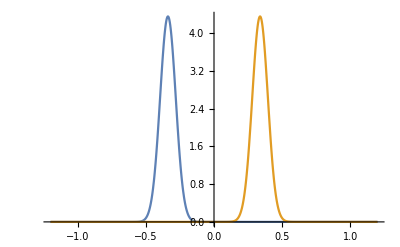

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.eq2],{x,-1.2,1.2},PlotRange->All]
```

```mathematica
sol2′=EcoEvoVarSim[{Subscript[x, 1]->-0.01,Subscript[x, 2]->0.01},{Subscript[n, 1]->0.1,Subscript[n, 2]->0.1},{Subscript[Var[x], 1]->0,Subscript[Var[x], 2]->0},5000];
FinalSlice[sol2′]
PlotDynamics[sol2′,n]
PlotDynamics[sol2′,x]
PlotDynamics[sol2′,{Var[x]},PlotRange->{0,All}]
```

{Var[x]_1→0.250009,Var[x]_2→0.250009,n_1→0.353548,n_2→0.353548,x_1→4.66616×10^-31,x_2→-4.44723×10^-31}

-Graphics-

-Graphics-

-Graphics-

```mathematica
eq2′=FindEcoEvoVarEq[FinalSlice[sol2′]]
EcoEvoVarEigenvalues[eq2′]
```

{Var[x]_1→0.250009,Var[x]_2→0.250009,n_1→0.0606926,n_2→0.646404,x_1→0,x_2→0}

{-0.437511+0.242103 ⅈ,-0.437511-0.242103 ⅈ,-0.500018,-0.375023,-0.0000279988,0}

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.eq2′],{x,-1.2,1.2},PlotRange->All]
```

-Graphics-

```mathematica
eq2′′=FindEcoEvoVarEq[{Subscript[Var[x], 1]->0.05,Subscript[Var[x], 2]->0.05,Subscript[n, 1]->0.5,Subscript[n, 2]->0.5,Subscript[x, 1]->-0.2,Subscript[x, 2]->0.2}]
```

{Var[x]_1→0.0485673,Var[x]_2→0.0485673,n_1→0.522991,n_2→0.522991,x_1→-0.263463,x_2→0.263463}

```mathematica
EcoEvoVarEigenvalues[eq2′′]
```

{-0.886219,-0.249807,-0.0922321,-0.0499537,0.0248703,0.0180186}

```mathematica
σμ=10^-2;
σ=0.5;
sol3=EcoEvoVarSim[eq2,5000];
FinalSlice[sol3]
PlotDynamics[sol3,n]
PlotDynamics[sol3,x]
PlotDynamics[sol3,{Var[x]},PlotRange->{0,All}]
```

{Var[x]_1→0.0171147,Var[x]_2→0.0171147,n_1→0.592876,n_2→0.592876,x_1→-0.323467,x_2→0.323467}

-Graphics-

-Graphics-

-Graphics-

```mathematica
eq3=FindEcoEvoVarEq[FinalSlice[sol3]]
EcoEvoVarEigenvalues[eq3]
```

{Var[x]_1→0.0171147,Var[x]_2→0.0171147,n_1→0.592876,n_2→0.592876,x_1→-0.323467,x_2→0.323467}

{-0.885254,-0.331873,-0.0444413,-0.0205705,-0.0085935,-0.00317141}

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.eq3],{x,-1.2,1.2},PlotRange->All]
```

-Graphics-

```mathematica
σμ=1.5 10^-2;
σ=0.5;
sol4=EcoEvoVarSim[eq3,5000];
FinalSlice[sol4]
PlotDynamics[sol4,n]
PlotDynamics[sol4,x]
PlotDynamics[sol4,{Var[x]},PlotRange->{0,All}]
```

{Var[x]_1→0.0291096,Var[x]_2→0.0291096,n_1→0.565465,n_2→0.565465,x_1→-0.305928,x_2→0.305928}

-Graphics-

-Graphics-

-Graphics-

```mathematica
eq4=FindEcoEvoVarEq[FinalSlice[sol4]]
EcoEvoVarEigenvalues[eq4]
```

{Var[x]_1→0.0291096,Var[x]_2→0.0291096,n_1→0.565465,n_2→0.565465,x_1→-0.305928,x_2→0.305928}

{-0.886078,-0.298989,-0.0672194,-0.0363211,-0.00594693,0.000442701}

```mathematica
Plot[Evaluate[{Subscript[n, 1] PDF[NormalDistribution[Subscript[x, 1],Sqrt[Subscript[Var[x], 1]]]][x],Subscript[n, 2] PDF[NormalDistribution[Subscript[x, 2],Sqrt[Subscript[Var[x], 2]]]][x]}/.eq4],{x,-1.2,1.2},PlotRange->All]
```

-Graphics-

```mathematica
σμ=1.55 10^-2;
σ=0.5;
eq5=FindEcoEvoVarEq[eq4]
EcoEvoVarEigenvalues[eq5]
```

{Var[x]_1→0.031257,Var[x]_2→0.031257,n_1→0.560661,n_2→0.560661,x_1→-0.302212,x_2→0.302212}

{-0.886167,-0.293337,-0.0707912,-0.0388376,-0.00427534,0.00159107}

```mathematica
sol5=EcoEvoVarSim[RuleListTweak[eq4,Subscript[x, 1],0.001],5000];
FinalSlice[sol5]
PlotDynamics[sol5,n]
PlotDynamics[sol5,x]
PlotDynamics[sol5,{Var[x]},PlotRange->{0,All}]
```

{Var[x]_1→0.251792,Var[x]_2→0.237011,n_1→0.647327,n_2→0.0591398,x_1→8.09881×10^-19,x_2→-1.39531×10^-15}

-Graphics-

-Graphics-

-Graphics-

## jonas1

```mathematica
Clear[a1,a2];
SetModel[jonas1]
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i]

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R2a a2[ξ[va]_i] va_i-1/2 R2a va_i (Var[ξ][va])_i a2''[ξ[va]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R1b a1[ξ[vb]_i] vb_i-1/2 R1b vb_i (Var[ξ][vb])_i a1''[ξ[vb]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R2b a2[ξ[vb]_i] vb_i-1/2 R2b vb_i (Var[ξ][vb])_i a2''[ξ[vb]_i]

```mathematica
a1[ξ_]:=(E^ξ/(1+E^ξ))^α;
a2[ξ_]:=(1-E^ξ/(1+E^ξ))^α;
μ=0.1;
r=1;
K1a=K2b=1;
K1b=K2a=0.4;
c1=c2=1;
α=0.5;
d=10.^-3;
M=5*10^-6;
```

```mathematica
sol=EcoEvoVarSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^5];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
FinalSlice[sol]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

-Graphics-

-Graphics-

-Graphics-

{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}

```mathematica
eq=FindEcoEvoVarEq[{Subscript[ξ[va], 1]->1,Subscript[ξ[vb], 1]->-1,Subscript[va, 1]->12,Subscript[vb, 1]->12,R1a->0.01,R1b->0.01,R2a->0.01,R2b->0.01,Var[ξ]->0.7}]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}

```mathematica
Plot[Evaluate[Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
Plot[Evaluate[Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol],{Subscript[Var[ξ][va], 0]->0.7464599779746975,Subscript[Var[ξ][vb], 0]->0.7464599779738803},{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_0→0.74646,(Var[ξ][vb])_0→0.74646,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-

```mathematica
EcoEvoVarEigenvalues[eq]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{-11.2036,-11.2036,-7.85541,-7.8554,-0.0929133,-0.0908831,-0.0142212,-0.0118852,-0.00457773,-0.00225553}

```mathematica
sol′=EcoEvoVarSim[Join[FinalSlice[sol],{Subscript[Var[ξ][va], 2]->0.7464599749190217,Subscript[Var[ξ][vb], 2]->0.7464599749190216,Subscript[va, 2]->1,Subscript[vb, 2]->1,Subscript[ξ[va], 2]->0.88,Subscript[ξ[vb], 2]->-0.87}],10^5,Verbose->False];
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

alltraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

nonfixedtraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

```mathematica
PlotDynamics[sol′,{va,vb},Logged->True]
PlotDynamics[sol′,{ξ[va],ξ[vb]}]
PlotDynamics[sol′,{Var[ξ][va],Var[ξ][vb]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol′],ExtractVarCovs[FinalSlice[sol′]],{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_1→0.0104154,(Var[ξ][va])_2→0.0103138,(Var[ξ][vb])_1→0.0103149,(Var[ξ][vb])_2→0.0104142,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-

```mathematica
Plot[Evaluate[{Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ],Subscript[va, 2] PDF[NormalDistribution[Subscript[ξ[va], 2],Sqrt[Subscript[Var[ξ][va], 2]]]][ξ]}/.FinalSlice[sol′]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
Plot[Evaluate[{Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ],Subscript[vb, 2] PDF[NormalDistribution[Subscript[ξ[vb], 2],Sqrt[Subscript[Var[ξ][vb], 2]]]][ξ]}/.FinalSlice[sol′]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
FinalSlice[sol′]
```

{(Var[ξ][va])_1→0.0104154,(Var[ξ][va])_2→0.0103138,(Var[ξ][vb])_1→0.0103149,(Var[ξ][vb])_2→0.0104142,va_1→0.947527,vb_1→11.6697,va_2→11.6697,vb_2→0.947523,R1a→0.0868734,R1b→0.0514077,R2a→0.0514077,R2b→0.0868735,ξ[va]_1→-1.02961,ξ[vb]_1→-1.03856,ξ[va]_2→1.03856,ξ[vb]_2→1.02961}

```mathematica
d=10.^-2;
M=5*10^-6;
```

```mathematica
sol=EcoEvoVarSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^5];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
FinalSlice[sol]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

-Graphics-

-Graphics-

-Graphics-

{(Var[ξ][va])_1→0.471782,(Var[ξ][vb])_1→0.471782,va_1→12.5886,vb_1→12.5886,R1a→0.098425,R1b→0.0427123,R2a→0.0427123,R2b→0.098425,ξ[va]_1→0.193106,ξ[vb]_1→-0.193106}

```mathematica
eq=FindEcoEvoVarEq[FinalSlice[sol]]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{(Var[ξ][va])_1→0.471782,(Var[ξ][vb])_1→0.471782,va_1→12.5886,vb_1→12.5886,R1a→0.098425,R1b→0.0427123,R2a→0.0427123,R2b→0.098425,ξ[va]_1→0.193106,ξ[vb]_1→-0.193106}

```mathematica
Plot[Evaluate[Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
Plot[Evaluate[Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol],ExtractVarCovs[FinalSlice[sol]],{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_1→0.471782,(Var[ξ][vb])_1→0.471782,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-

```mathematica
EcoEvoVarEigenvalues[eq]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{-10.0955,-10.0954,-9.33651,-9.33644,-0.11097,-0.0907031,-0.0297874,-0.0262774,-0.00461237,-0.00119383}

```mathematica
FinalSlice[sol]
```

{(Var[ξ][va])_1→0.471782,(Var[ξ][vb])_1→0.471782,va_1→12.5886,vb_1→12.5886,R1a→0.098425,R1b→0.0427123,R2a→0.0427123,R2b→0.098425,ξ[va]_1→0.193106,ξ[vb]_1→-0.193106}

```mathematica
sol′=EcoEvoVarSim[Join[FinalSlice[sol],{Subscript[Var[ξ][va], 2]->0.471782,Subscript[Var[ξ][vb], 2]->0.471782,Subscript[va, 2]->1,Subscript[vb, 2]->1,Subscript[ξ[va], 2]->0.2,Subscript[ξ[vb], 2]->-0.185}],10^5,Verbose->False];
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

alltraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

nonfixedtraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

```mathematica
PlotDynamics[sol′,{va,vb},Logged->True]
PlotDynamics[sol′,{ξ[va],ξ[vb]}]
PlotDynamics[sol′,{Var[ξ][va],Var[ξ][vb]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate[{Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ],Subscript[va, 2] PDF[NormalDistribution[Subscript[ξ[va], 2],Sqrt[Subscript[Var[ξ][va], 2]]]][ξ]}/.FinalSlice[sol′]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
Plot[Evaluate[{Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ],Subscript[vb, 2] PDF[NormalDistribution[Subscript[ξ[vb], 2],Sqrt[Subscript[Var[ξ][vb], 2]]]][ξ]}/.FinalSlice[sol′]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol′],ExtractVarCovs[FinalSlice[sol′]],{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_1→0.0156286,(Var[ξ][va])_2→0.0153579,(Var[ξ][vb])_1→0.0155333,(Var[ξ][vb])_2→0.0154508,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-

## jonas1

```mathematica
Clear[a1,a2];
SetModel[jonas1]
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i]

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R2a a2[ξ[va]_i] va_i-1/2 R2a va_i (Var[ξ][va])_i a2''[ξ[va]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R1b a1[ξ[vb]_i] vb_i-1/2 R1b vb_i (Var[ξ][vb])_i a1''[ξ[vb]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R2b a2[ξ[vb]_i] vb_i-1/2 R2b vb_i (Var[ξ][vb])_i a2''[ξ[vb]_i]

```mathematica
a1[ξ_]:=(E^ξ/(1+E^ξ))^α;
a2[ξ_]:=(1-E^ξ/(1+E^ξ))^α;
μ=0.1;
r=1;
K1a=K2b=1;
K1b=K2a=0.4;
c1=c2=1;
α=0.5;
d=10.^-3;
M=5*10^-6;
```

```mathematica
sol=EcoEvoVarSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^5];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
FinalSlice[sol]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

-Graphics-

-Graphics-

-Graphics-

{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}

```mathematica
eq=FindEcoEvoVarEq[{Subscript[ξ[va], 1]->1,Subscript[ξ[vb], 1]->-1,Subscript[va, 1]->12,Subscript[vb, 1]->12,R1a->0.01,R1b->0.01,R2a->0.01,R2b->0.01,Var[ξ]->0.7}]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}

```mathematica
Plot[Evaluate[Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
Plot[Evaluate[Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol],{Subscript[Var[ξ][va], 0]->0.7464599779746975,Subscript[Var[ξ][vb], 0]->0.7464599779738803},{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_0→0.74646,(Var[ξ][vb])_0→0.74646,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-

```mathematica
EcoEvoVarEigenvalues[eq]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{-11.2036,-11.2036,-7.85541,-7.8554,-0.0929133,-0.0908831,-0.0142212,-0.0118852,-0.00457773,-0.00225553}

```mathematica
sol′=EcoEvoVarSim[Join[FinalSlice[sol],{Subscript[Var[ξ][va], 2]->0.7464599749190217,Subscript[Var[ξ][vb], 2]->0.7464599749190216,Subscript[va, 2]->1,Subscript[vb, 2]->1,Subscript[ξ[va], 2]->0.88,Subscript[ξ[vb], 2]->-0.87}],10^5,Verbose->False];
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

alltraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

nonfixedtraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

```mathematica
PlotDynamics[sol′,{va,vb},Logged->True]
PlotDynamics[sol′,{ξ[va],ξ[vb]}]
PlotDynamics[sol′,{Var[ξ][va],Var[ξ][vb]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol′],ExtractVarCovs[FinalSlice[sol′]],{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_1→0.0104154,(Var[ξ][va])_2→0.0103138,(Var[ξ][vb])_1→0.0103149,(Var[ξ][vb])_2→0.0104142,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-

```mathematica
Plot[Evaluate[{Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ],Subscript[va, 2] PDF[NormalDistribution[Subscript[ξ[va], 2],Sqrt[Subscript[Var[ξ][va], 2]]]][ξ]}/.FinalSlice[sol′]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
Plot[Evaluate[{Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ],Subscript[vb, 2] PDF[NormalDistribution[Subscript[ξ[vb], 2],Sqrt[Subscript[Var[ξ][vb], 2]]]][ξ]}/.FinalSlice[sol′]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
FinalSlice[sol′]
```

{(Var[ξ][va])_1→0.0104154,(Var[ξ][va])_2→0.0103138,(Var[ξ][vb])_1→0.0103149,(Var[ξ][vb])_2→0.0104142,va_1→0.947527,vb_1→11.6697,va_2→11.6697,vb_2→0.947523,R1a→0.0868734,R1b→0.0514077,R2a→0.0514077,R2b→0.0868735,ξ[va]_1→-1.02961,ξ[vb]_1→-1.03856,ξ[va]_2→1.03856,ξ[vb]_2→1.02961}

```mathematica
d=10.^-1;
M=5*10^-6;
```

```mathematica
sol=EcoEvoVarSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^5];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
FinalSlice[sol]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

-Graphics-

-Graphics-

-Graphics-

{(Var[ξ][va])_1→0.00989288,(Var[ξ][vb])_1→0.00989288,va_1→12.5854,vb_1→12.5854,R1a→0.101034,R1b→0.0404232,R2a→0.0404232,R2b→0.101034,ξ[va]_1→0.000528877,ξ[vb]_1→-0.000529138}

```mathematica
eq=FindEcoEvoVarEq[FinalSlice[sol]]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{(Var[ξ][va])_1→0.00989219,(Var[ξ][vb])_1→0.00989219,va_1→12.5854,vb_1→12.5854,R1a→0.101034,R1b→0.0404232,R2a→0.0404232,R2b→0.101034,ξ[va]_1→0.000528971,ξ[vb]_1→-0.000528971}

```mathematica
Plot[Evaluate[Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
Plot[Evaluate[Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol],ExtractVarCovs[FinalSlice[sol]],{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_1→0.00989288,(Var[ξ][vb])_1→0.00989288,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-

```mathematica
EcoEvoVarEigenvalues[eq]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{-9.89595,-9.89595,-9.80624,-9.80434,-0.292635,-0.20014,-0.200124,-0.0907285,-0.000116544,-0.000101153}

## jonas1

```mathematica
Clear[a1,a2];
SetModel[jonas1]
```

ReplaceAll::reps: {Aux[R1a,Range→Interval[{-∞,∞}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,Color→RGBColor[0.368417, 0.506779, 0.709798]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Aux[R1a,LineStyle→{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R1a a1[ξ[va]_i] va_i-1/2 R1a va_i (Var[ξ][va])_i a1''[ξ[va]_i]

** agentG={{(Var[ξ][va])_i}}

** f-hat=-R2a a2[ξ[va]_i] va_i-1/2 R2a va_i (Var[ξ][va])_i a2''[ξ[va]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R1b a1[ξ[vb]_i] vb_i-1/2 R1b vb_i (Var[ξ][vb])_i a1''[ξ[vb]_i]

** agentG={{(Var[ξ][vb])_i}}

** f-hat=-R2b a2[ξ[vb]_i] vb_i-1/2 R2b vb_i (Var[ξ][vb])_i a2''[ξ[vb]_i]

```mathematica
a1[ξ_]:=(E^ξ/(1+E^ξ))^α;
a2[ξ_]:=(1-E^ξ/(1+E^ξ))^α;
μ=0.1;
r=1;
K1a=K2b=1;
K1b=K2a=0.4;
c1=c2=1;
α=0.5;
d=10.^-3;
M=5*10^-6;
```

```mathematica
sol=EcoEvoVarSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^5];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
FinalSlice[sol]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

-Graphics-

-Graphics-

-Graphics-

{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}

```mathematica
eq=FindEcoEvoVarEq[{Subscript[ξ[va], 1]->1,Subscript[ξ[vb], 1]->-1,Subscript[va, 1]->12,Subscript[vb, 1]->12,R1a->0.01,R1b->0.01,R2a->0.01,R2b->0.01,Var[ξ]->0.7}]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{(Var[ξ][va])_1→0.74646,(Var[ξ][vb])_1→0.74646,va_1→12.6053,vb_1→12.6053,R1a→0.0887243,R1b→0.050748,R2a→0.050748,R2b→0.0887243,ξ[va]_1→0.878775,ξ[vb]_1→-0.878775}

```mathematica
Plot[Evaluate[Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
Plot[Evaluate[Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol],{Subscript[Var[ξ][va], 0]->0.7464599779746975,Subscript[Var[ξ][vb], 0]->0.7464599779738803},{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_0→0.74646,(Var[ξ][vb])_0→0.74646,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-

```mathematica
EcoEvoVarEigenvalues[eq]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{-11.2036,-11.2036,-7.85541,-7.8554,-0.0929133,-0.0908831,-0.0142212,-0.0118852,-0.00457773,-0.00225553}

```mathematica
sol′=EcoEvoVarSim[Join[FinalSlice[sol],{Subscript[Var[ξ][va], 2]->0.7464599749190217,Subscript[Var[ξ][vb], 2]->0.7464599749190216,Subscript[va, 2]->1,Subscript[vb, 2]->1,Subscript[ξ[va], 2]->0.88,Subscript[ξ[vb], 2]->-0.87}],10^5,Verbose->False];
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

alltraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

nonfixedtraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

```mathematica
PlotDynamics[sol′,{va,vb},Logged->True]
PlotDynamics[sol′,{ξ[va],ξ[vb]}]
PlotDynamics[sol′,{Var[ξ][va],Var[ξ][vb]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol′],ExtractVarCovs[FinalSlice[sol′]],{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_1→0.0104154,(Var[ξ][va])_2→0.0103138,(Var[ξ][vb])_1→0.0103149,(Var[ξ][vb])_2→0.0104142,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-

```mathematica
Plot[Evaluate[{Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ],Subscript[va, 2] PDF[NormalDistribution[Subscript[ξ[va], 2],Sqrt[Subscript[Var[ξ][va], 2]]]][ξ]}/.FinalSlice[sol′]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
Plot[Evaluate[{Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ],Subscript[vb, 2] PDF[NormalDistribution[Subscript[ξ[vb], 2],Sqrt[Subscript[Var[ξ][vb], 2]]]][ξ]}/.FinalSlice[sol′]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
FinalSlice[sol′]
```

{(Var[ξ][va])_1→0.0104154,(Var[ξ][va])_2→0.0103138,(Var[ξ][vb])_1→0.0103149,(Var[ξ][vb])_2→0.0104142,va_1→0.947527,vb_1→11.6697,va_2→11.6697,vb_2→0.947523,R1a→0.0868734,R1b→0.0514077,R2a→0.0514077,R2b→0.0868735,ξ[va]_1→-1.02961,ξ[vb]_1→-1.03856,ξ[va]_2→1.03856,ξ[vb]_2→1.02961}

```mathematica
d=10.^-1.8;
M=5*10^-6;
```

```mathematica
sol=EcoEvoVarSim[{Subscript[ξ[va], 1]->-1,Subscript[ξ[vb], 1]->-1},{Subscript[va, 1]->0.1,Subscript[vb, 1]->0.1,R1a->K1a,R1b->K1b,R2a->K2a,R2b->K2b},{Var[ξ]->0.1},10^5];
PlotDynamics[sol,{va,vb}]
PlotDynamics[sol,{ξ[va],ξ[vb]}]
PlotDynamics[sol,{Var[ξ][va],Var[ξ][vb]}]
FinalSlice[sol]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

-Graphics-

-Graphics-

-Graphics-

{(Var[ξ][va])_1→0.136732,(Var[ξ][vb])_1→0.136732,va_1→12.586,vb_1→12.586,R1a→0.100448,R1b→0.0409549,R2a→0.0409549,R2b→0.100448,ξ[va]_1→0.0433028,ξ[vb]_1→-0.0433028}

```mathematica
eq=FindEcoEvoVarEq[FinalSlice[sol]]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{(Var[ξ][va])_1→0.136732,(Var[ξ][vb])_1→0.136732,va_1→12.586,vb_1→12.586,R1a→0.100448,R1b→0.0409549,R2a→0.0409549,R2b→0.100448,ξ[va]_1→0.0433028,ξ[vb]_1→-0.0433028}

```mathematica
Plot[Evaluate[Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
Plot[Evaluate[Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ]/.eq],{ξ,-2,2},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol],ExtractVarCovs[FinalSlice[sol]],{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_1→0.136732,(Var[ξ][vb])_1→0.136732,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-

```mathematica
EcoEvoVarEigenvalues[eq]
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1}

alltraits={ξ[va]_1,ξ[vb]_1}

nonfixedtraits={ξ[va]_1,ξ[vb]_1}

{-9.90033,-9.9002,-9.73043,-9.73027,-0.122738,-0.0907102,-0.0348854,-0.0334329,-0.00153991,-0.000124985}

```mathematica
FinalSlice[sol]
```

{(Var[ξ][va])_1→0.136732,(Var[ξ][vb])_1→0.136732,va_1→12.586,vb_1→12.586,R1a→0.100448,R1b→0.0409549,R2a→0.0409549,R2b→0.100448,ξ[va]_1→0.0433028,ξ[vb]_1→-0.0433028}

```mathematica
sol′=EcoEvoVarSim[Join[FinalSlice[sol],{Subscript[Var[ξ][va], 2]->0.136732,Subscript[Var[ξ][vb], 2]->0.136732,Subscript[va, 2]->1,Subscript[vb, 2]->1,Subscript[ξ[va], 2]->0.053,Subscript[ξ[vb], 2]->-0.033}],10^6,Verbose->False];
```

AllTraits={ξ_1,ξ[va]_1,ξ[vb]_1,ξ_2,ξ[va]_2,ξ[vb]_2}

alltraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

nonfixedtraits={ξ[va]_1,ξ[vb]_1,ξ[va]_2,ξ[vb]_2}

```mathematica
PlotDynamics[sol′,{va,vb},Logged->True]
PlotDynamics[sol′,{ξ[va],ξ[vb]}]
PlotDynamics[sol′,{Var[ξ][va],Var[ξ][vb]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Plot[Evaluate[{Subscript[va, 1] PDF[NormalDistribution[Subscript[ξ[va], 1],Sqrt[Subscript[Var[ξ][va], 1]]]][ξ],Subscript[va, 2] PDF[NormalDistribution[Subscript[ξ[va], 2],Sqrt[Subscript[Var[ξ][va], 2]]]][ξ]}/.FinalSlice[sol′]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
Plot[Evaluate[{Subscript[vb, 1] PDF[NormalDistribution[Subscript[ξ[vb], 1],Sqrt[Subscript[Var[ξ][vb], 1]]]][ξ],Subscript[vb, 2] PDF[NormalDistribution[Subscript[ξ[vb], 2],Sqrt[Subscript[Var[ξ][vb], 2]]]][ξ]}/.FinalSlice[sol′]],{ξ,-1.5,1.5},PlotRange->All,Filling->Axis]
```

-Graphics-

-Graphics-

```mathematica
PlotInv[FinalSlice[sol′],ExtractVarCovs[FinalSlice[sol′]],{Subscript[ξ, 0],-2,2}]
```

invaderGs={(Var[ξ][va])_1→0.0283957,(Var[ξ][va])_2→0.02824,(Var[ξ][vb])_1→0.0282412,(Var[ξ][vb])_2→0.0283946,Var[ξ]_0→0,(Var[ξ][va])_0→0,(Var[ξ][vb])_0→0}

-Graphics-